```mathematica
(*Considers also 5-1 move*)
```

```mathematica
Gr[θ12_,θ13_,θ14_,θ15_,θ23_,θ24_,θ25_,θ34_,θ35_,θ45_ ]:=({{1, -Cos[θ12], -Cos[θ13], -Cos[θ14], -Cos[θ15]}, {-Cos[θ12], 1, -Cos[θ23], -Cos[θ24], -Cos[θ25]}, {-Cos[θ13], -Cos[θ23], 1, -Cos[θ34], -Cos[θ35]}, {-Cos[θ14], -Cos[θ24], -Cos[θ34], 1, -Cos[θ45]}, {-Cos[θ15], -Cos[θ25], -Cos[θ35], -Cos[θ45], 1}})
```

```mathematica
(*compute first derivatives*)
```

```mathematica
(*D[Det[Gr[θ12,θ13,θ14,θ15,θ23,θ24,θ25,θ34,θ35,θ45 ]], {{θ12,θ13,θ14,θ15,θ23,θ24,θ25,θ34,θ35,θ45} ,1}]//Simplify*)
```

```mathematica
FD[θ12_,θ13_,θ14_,θ15_,θ23_,θ24_,θ25_,θ34_,θ35_,θ45_]:={2 Sin[θ12] (Cos[θ14] Cos[θ23] Cos[θ34]+Cos[θ13] Cos[θ24] Cos[θ34]+Cos[θ13] Cos[θ25] Cos[θ35]+Cos[θ14] Cos[θ25] Cos[θ34] Cos[θ35]+Cos[θ14] Cos[θ25] Cos[θ45]+Cos[θ13] Cos[θ25] Cos[θ34] Cos[θ45]+Cos[θ14] Cos[θ23] Cos[θ35] Cos[θ45]+Cos[θ13] Cos[θ24] Cos[θ35] Cos[θ45]-Cos[θ12] (-1+Cos[θ34]^2+Cos[θ35]^2+2 Cos[θ34] Cos[θ35] Cos[θ45]+Cos[θ45]^2)+Cos[θ15] (Cos[θ24] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ23] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ25] Sin[θ34]^2)+Cos[θ14] Cos[θ24] Sin[θ35]^2+Cos[θ13] Cos[θ23] Sin[θ45]^2),2 Sin[θ13] (Cos[θ15] Cos[θ23] Cos[θ25]+Cos[θ12] Cos[θ24] Cos[θ34]+Cos[θ15] Cos[θ24] Cos[θ25] Cos[θ34]+Cos[θ15] Cos[θ35]-Cos[θ15] Cos[θ24]^2 Cos[θ35]+Cos[θ12] Cos[θ25] Cos[θ35]+Cos[θ15] Cos[θ23] Cos[θ24] Cos[θ45]+Cos[θ15] Cos[θ34] Cos[θ45]+Cos[θ12] Cos[θ25] Cos[θ34] Cos[θ45]+Cos[θ12] Cos[θ24] Cos[θ35] Cos[θ45]-Cos[θ13] (-1+Cos[θ24]^2+Cos[θ25]^2+2 Cos[θ24] Cos[θ25] Cos[θ45]+Cos[θ45]^2)+Cos[θ14] (Cos[θ35] (Cos[θ24] Cos[θ25]+Cos[θ45])+Cos[θ23] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ34] Sin[θ25]^2)+Cos[θ12] Cos[θ23] Sin[θ45]^2),2 Sin[θ14] (Cos[θ15] Cos[θ24] Cos[θ25]+Cos[θ12] Cos[θ23] Cos[θ34]+Cos[θ15] Cos[θ23] Cos[θ25] Cos[θ34]+Cos[θ15] Cos[θ23] Cos[θ24] Cos[θ35]+Cos[θ15] Cos[θ34] Cos[θ35]+Cos[θ12] Cos[θ25] Cos[θ34] Cos[θ35]-Cos[θ14] (-1+Cos[θ23]^2+Cos[θ25]^2+2 Cos[θ23] Cos[θ25] Cos[θ35]+Cos[θ35]^2)+Cos[θ15] Cos[θ45]-Cos[θ15] Cos[θ23]^2 Cos[θ45]+Cos[θ12] Cos[θ25] Cos[θ45]+Cos[θ12] Cos[θ23] Cos[θ35] Cos[θ45]+Cos[θ13] (Cos[θ35] (Cos[θ24] Cos[θ25]+Cos[θ45])+Cos[θ23] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ34] Sin[θ25]^2)+Cos[θ12] Cos[θ24] Sin[θ35]^2),2 Sin[θ15] (Cos[θ14] Cos[θ24] Cos[θ25]+Cos[θ14] Cos[θ23] Cos[θ25] Cos[θ34]-Cos[θ15] (-1+Cos[θ23]^2+Cos[θ24]^2+2 Cos[θ23] Cos[θ24] Cos[θ34]+Cos[θ34]^2)+Cos[θ12] Cos[θ23] Cos[θ35]+Cos[θ14] Cos[θ23] Cos[θ24] Cos[θ35]+Cos[θ14] Cos[θ34] Cos[θ35]+Cos[θ12] Cos[θ24] Cos[θ34] Cos[θ35]+Cos[θ14] Cos[θ45]-Cos[θ14] Cos[θ23]^2 Cos[θ45]+Cos[θ12] Cos[θ24] Cos[θ45]+Cos[θ12] Cos[θ23] Cos[θ34] Cos[θ45]+Cos[θ13] (Cos[θ24] Cos[θ25] Cos[θ34]+Cos[θ35]-Cos[θ24]^2 Cos[θ35]+Cos[θ34] Cos[θ45]+Cos[θ23] (Cos[θ25]+Cos[θ24] Cos[θ45]))+Cos[θ12] Cos[θ25] Sin[θ34]^2),2 Sin[θ23] (Cos[θ13] Cos[θ14] Cos[θ24]+Cos[θ13] Cos[θ15] Cos[θ25]+Cos[θ24] Cos[θ34]-Cos[θ15]^2 Cos[θ24] Cos[θ34]+Cos[θ14] Cos[θ15] Cos[θ25] Cos[θ34]+Cos[θ14] Cos[θ15] Cos[θ24] Cos[θ35]+Cos[θ25] Cos[θ35]-Cos[θ14]^2 Cos[θ25] Cos[θ35]+Cos[θ13] Cos[θ15] Cos[θ24] Cos[θ45]+Cos[θ13] Cos[θ14] Cos[θ25] Cos[θ45]+Cos[θ25] Cos[θ34] Cos[θ45]+Cos[θ24] Cos[θ35] Cos[θ45]-Cos[θ23] (-1+Cos[θ14]^2+Cos[θ15]^2+2 Cos[θ14] Cos[θ15] Cos[θ45]+Cos[θ45]^2)+Cos[θ12] (Cos[θ15] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ14] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ13] Sin[θ45]^2)),2 Sin[θ24] (Cos[θ24]-Cos[θ15]^2 Cos[θ24]+Cos[θ14] Cos[θ15] Cos[θ25]+Cos[θ23] Cos[θ34]-Cos[θ15]^2 Cos[θ23] Cos[θ34]+Cos[θ14] Cos[θ15] Cos[θ23] Cos[θ35]+Cos[θ25] Cos[θ34] Cos[θ35]-Cos[θ24] Cos[θ35]^2+Cos[θ25] Cos[θ45]+Cos[θ23] Cos[θ35] Cos[θ45]-Cos[θ13]^2 (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ13] (Cos[θ14] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ15] (Cos[θ25] Cos[θ34]-2 Cos[θ24] Cos[θ35]+Cos[θ23] Cos[θ45]))+Cos[θ12] (Cos[θ15] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ13] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ14] Sin[θ35]^2)),2 Sin[θ25] (Cos[θ25]-Cos[θ25] Cos[θ34]^2+Cos[θ23] Cos[θ35]+Cos[θ24] Cos[θ34] Cos[θ35]-Cos[θ14]^2 (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ24] Cos[θ45]+Cos[θ23] Cos[θ34] Cos[θ45]-Cos[θ13]^2 (Cos[θ25]+Cos[θ24] Cos[θ45])+Cos[θ14] (Cos[θ15] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ12] (Cos[θ34] Cos[θ35]+Cos[θ45]))+Cos[θ13] (Cos[θ15] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ14] (-2 Cos[θ25] Cos[θ34]+Cos[θ24] Cos[θ35]+Cos[θ23] Cos[θ45])+Cos[θ12] (Cos[θ35]+Cos[θ34] Cos[θ45]))+Cos[θ12] Cos[θ15] Sin[θ34]^2),2 (Cos[θ13] Cos[θ15] Cos[θ24] Cos[θ25]+Cos[θ34]-Cos[θ15]^2 Cos[θ34]-Cos[θ25]^2 Cos[θ34]+Cos[θ14] Cos[θ15] Cos[θ35]+Cos[θ24] Cos[θ25] Cos[θ35]+Cos[θ13] Cos[θ15] Cos[θ45]+Cos[θ35] Cos[θ45]-Cos[θ12]^2 (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ12] (Cos[θ14] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ15] (-2 Cos[θ25] Cos[θ34]+Cos[θ24] Cos[θ35]+Cos[θ23] Cos[θ45])+Cos[θ13] (Cos[θ24]+Cos[θ25] Cos[θ45]))+Cos[θ23] (Cos[θ25] (Cos[θ14] Cos[θ15]+Cos[θ45])+Cos[θ24] Sin[θ15]^2)+Cos[θ13] Cos[θ14] Sin[θ25]^2) Sin[θ34],2 (Cos[θ23] Cos[θ25]+Cos[θ24] Cos[θ25] Cos[θ34]+Cos[θ35]-Cos[θ24]^2 Cos[θ35]-Cos[θ14]^2 (Cos[θ23] Cos[θ25]+Cos[θ35])+Cos[θ23] Cos[θ24] Cos[θ45]+Cos[θ34] Cos[θ45]-Cos[θ12]^2 (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ14] (Cos[θ15] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ13] (Cos[θ24] Cos[θ25]+Cos[θ45]))+Cos[θ12] (Cos[θ15] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ14] (Cos[θ25] Cos[θ34]-2 Cos[θ24] Cos[θ35]+Cos[θ23] Cos[θ45])+Cos[θ13] (Cos[θ25]+Cos[θ24] Cos[θ45]))+Cos[θ13] Cos[θ15] Sin[θ24]^2) Sin[θ35],2 (Cos[θ24] Cos[θ25]+Cos[θ23] Cos[θ25] Cos[θ34]+Cos[θ23] Cos[θ24] Cos[θ35]+Cos[θ34] Cos[θ35]+Cos[θ13] (Cos[θ15] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ14] (Cos[θ23] Cos[θ25]+Cos[θ35]))+Cos[θ45]-Cos[θ23]^2 Cos[θ45]-Cos[θ13]^2 (Cos[θ24] Cos[θ25]+Cos[θ45])-Cos[θ12]^2 (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ12] (Cos[θ15] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ14] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ13] (Cos[θ25] Cos[θ34]+Cos[θ24] Cos[θ35]-2 Cos[θ23] Cos[θ45]))+Cos[θ14] Cos[θ15] Sin[θ23]^2) Sin[θ45]}
```

```mathematica
(*compute Hessian*)
```

```mathematica
(*D[Det[Gr[θ12,θ13,θ14,θ15,θ23,θ24,θ25,θ34,θ35,θ45 ]], {{θ12,θ13,θ14,θ15,θ23,θ24,θ25,θ34,θ35,θ45 } ,2}]//Simplify*)
```

```mathematica
Hess[θ12_,θ13_,θ14_,θ15_,θ23_,θ24_,θ25_,θ34_,θ35_,θ45_]:={{2 (-Cos[θ12]^2 (-1+Cos[θ34]^2+Cos[θ35]^2+2 Cos[θ34] Cos[θ35] Cos[θ45]+Cos[θ45]^2)+(-1+Cos[θ34]^2+Cos[θ35]^2+2 Cos[θ34] Cos[θ35] Cos[θ45]+Cos[θ45]^2) Sin[θ12]^2+Cos[θ12] (Cos[θ15] (Cos[θ24] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ23] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ25] Sin[θ34]^2)+Cos[θ14] (Cos[θ25] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ23] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ24] Sin[θ35]^2)+Cos[θ13] (Cos[θ25] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ24] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ23] Sin[θ45]^2))),-2 Sin[θ12] Sin[θ13] (Cos[θ25] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ24] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ23] Sin[θ45]^2),-2 Sin[θ12] Sin[θ14] (Cos[θ25] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ23] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ24] Sin[θ35]^2),-2 Sin[θ12] Sin[θ15] (Cos[θ24] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ23] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ25] Sin[θ34]^2),-2 Sin[θ12] Sin[θ23] (Cos[θ15] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ14] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ13] Sin[θ45]^2),-2 Sin[θ12] Sin[θ24] (Cos[θ15] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ13] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ14] Sin[θ35]^2),-2 Sin[θ12] Sin[θ25] (Cos[θ14] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ13] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ15] Sin[θ34]^2),-2 (-2 Cos[θ12] Cos[θ34]-2 Cos[θ15] Cos[θ25] Cos[θ34]+Cos[θ15] Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ15] Cos[θ23] Cos[θ45]-2 Cos[θ12] Cos[θ35] Cos[θ45]+Cos[θ13] (Cos[θ24]+Cos[θ25] Cos[θ45])) Sin[θ12] Sin[θ34],-2 (Cos[θ14] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ23]+Cos[θ24] Cos[θ34])-2 Cos[θ12] Cos[θ35]-2 Cos[θ14] Cos[θ24] Cos[θ35]+Cos[θ14] Cos[θ23] Cos[θ45]-2 Cos[θ12] Cos[θ34] Cos[θ45]+Cos[θ13] (Cos[θ25]+Cos[θ24] Cos[θ45])) Sin[θ12] Sin[θ35],-2 (Cos[θ13] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ13] Cos[θ24] Cos[θ35]-2 Cos[θ12] Cos[θ34] Cos[θ35]+Cos[θ14] (Cos[θ25]+Cos[θ23] Cos[θ35])-2 Cos[θ12] Cos[θ45]-2 Cos[θ13] Cos[θ23] Cos[θ45]) Sin[θ12] Sin[θ45]},{-2 Sin[θ12] Sin[θ13] (Cos[θ25] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ24] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ23] Sin[θ45]^2),2 (-Cos[θ13]^2 (-1+Cos[θ24]^2+Cos[θ25]^2+2 Cos[θ24] Cos[θ25] Cos[θ45]+Cos[θ45]^2)+(-1+Cos[θ24]^2+Cos[θ25]^2+2 Cos[θ24] Cos[θ25] Cos[θ45]+Cos[θ45]^2) Sin[θ13]^2+Cos[θ13] (Cos[θ15] (Cos[θ24] Cos[θ25] Cos[θ34]+Cos[θ35]-Cos[θ24]^2 Cos[θ35]+Cos[θ34] Cos[θ45]+Cos[θ23] (Cos[θ25]+Cos[θ24] Cos[θ45]))+Cos[θ14] (Cos[θ24] Cos[θ25] Cos[θ35]+Cos[θ35] Cos[θ45]+Cos[θ23] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ34] Sin[θ25]^2)+Cos[θ12] (Cos[θ25] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ24] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ23] Sin[θ45]^2))),-2 Sin[θ13] Sin[θ14] (Cos[θ35] (Cos[θ24] Cos[θ25]+Cos[θ45])+Cos[θ23] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ34] Sin[θ25]^2),-2 (Cos[θ24] Cos[θ25] Cos[θ34]+Cos[θ35]-Cos[θ24]^2 Cos[θ35]+Cos[θ34] Cos[θ45]+Cos[θ23] (Cos[θ25]+Cos[θ24] Cos[θ45])) Sin[θ13] Sin[θ15],-2 Sin[θ13] Sin[θ23] (Cos[θ15] (Cos[θ25]+Cos[θ24] Cos[θ45])+Cos[θ14] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ12] Sin[θ45]^2),-2 (Cos[θ12] Cos[θ34]+Cos[θ15] Cos[θ25] Cos[θ34]-2 Cos[θ15] Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ15] Cos[θ23] Cos[θ45]+Cos[θ12] Cos[θ35] Cos[θ45]-2 Cos[θ13] (Cos[θ24]+Cos[θ25] Cos[θ45])) Sin[θ13] Sin[θ24],-2 (-2 Cos[θ14] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ12] Cos[θ35]+Cos[θ14] Cos[θ24] Cos[θ35]+Cos[θ14] Cos[θ23] Cos[θ45]+Cos[θ12] Cos[θ34] Cos[θ45]-2 Cos[θ13] (Cos[θ25]+Cos[θ24] Cos[θ45])) Sin[θ13] Sin[θ25],-2 Sin[θ13] (Cos[θ15] (Cos[θ24] Cos[θ25]+Cos[θ45])+Cos[θ12] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ14] Sin[θ25]^2) Sin[θ34],-2 Sin[θ13] (Cos[θ14] (Cos[θ24] Cos[θ25]+Cos[θ45])+Cos[θ12] (Cos[θ25]+Cos[θ24] Cos[θ45])+Cos[θ15] Sin[θ24]^2) Sin[θ35],-2 (-2 Cos[θ13] Cos[θ24] Cos[θ25]+Cos[θ12] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ12] Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ23] Cos[θ25]+Cos[θ35])-2 Cos[θ13] Cos[θ45]-2 Cos[θ12] Cos[θ23] Cos[θ45]) Sin[θ13] Sin[θ45]},{-2 Sin[θ12] Sin[θ14] (Cos[θ25] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ23] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ24] Sin[θ35]^2),-2 Sin[θ13] Sin[θ14] (Cos[θ35] (Cos[θ24] Cos[θ25]+Cos[θ45])+Cos[θ23] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ34] Sin[θ25]^2),2 (-Cos[θ14]^2 (-1+Cos[θ23]^2+Cos[θ25]^2+2 Cos[θ23] Cos[θ25] Cos[θ35]+Cos[θ35]^2)+(-1+Cos[θ23]^2+Cos[θ25]^2+2 Cos[θ23] Cos[θ25] Cos[θ35]+Cos[θ35]^2) Sin[θ14]^2+Cos[θ14] (Cos[θ15] (Cos[θ23] Cos[θ25] Cos[θ34]+Cos[θ34] Cos[θ35]+Cos[θ24] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ45]-Cos[θ23]^2 Cos[θ45])+Cos[θ13] (Cos[θ24] Cos[θ25] Cos[θ35]+Cos[θ35] Cos[θ45]+Cos[θ23] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ34] Sin[θ25]^2)+Cos[θ12] (Cos[θ25] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ23] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ24] Sin[θ35]^2))),-2 (Cos[θ23] Cos[θ25] Cos[θ34]+Cos[θ34] Cos[θ35]+Cos[θ24] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ45]-Cos[θ23]^2 Cos[θ45]) Sin[θ14] Sin[θ15],-2 (Cos[θ12] Cos[θ34]+Cos[θ15] Cos[θ25] Cos[θ34]+Cos[θ15] Cos[θ24] Cos[θ35]-2 Cos[θ14] (Cos[θ23]+Cos[θ25] Cos[θ35])-2 Cos[θ15] Cos[θ23] Cos[θ45]+Cos[θ12] Cos[θ35] Cos[θ45]+Cos[θ13] (Cos[θ24]+Cos[θ25] Cos[θ45])) Sin[θ14] Sin[θ23],-2 Sin[θ14] Sin[θ24] (Cos[θ15] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ13] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ12] Sin[θ35]^2),-2 (-2 Cos[θ13] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ13] Cos[θ24] Cos[θ35]+Cos[θ12] Cos[θ34] Cos[θ35]-2 Cos[θ14] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ12] Cos[θ45]+Cos[θ13] Cos[θ23] Cos[θ45]) Sin[θ14] Sin[θ25],-2 Sin[θ14] (Cos[θ15] (Cos[θ23] Cos[θ25]+Cos[θ35])+Cos[θ12] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ13] Sin[θ25]^2) Sin[θ34],-2 (Cos[θ13] Cos[θ24] Cos[θ25]+Cos[θ12] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ23] Cos[θ24]+Cos[θ34])-2 Cos[θ12] Cos[θ24] Cos[θ35]-2 Cos[θ14] (Cos[θ23] Cos[θ25]+Cos[θ35])+Cos[θ13] Cos[θ45]+Cos[θ12] Cos[θ23] Cos[θ45]) Sin[θ14] Sin[θ35],-2 Sin[θ14] (Cos[θ13] (Cos[θ23] Cos[θ25]+Cos[θ35])+Cos[θ12] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ15] Sin[θ23]^2) Sin[θ45]},{-2 Sin[θ12] Sin[θ15] (Cos[θ24] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ23] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ25] Sin[θ34]^2),-2 (Cos[θ24] Cos[θ25] Cos[θ34]+Cos[θ35]-Cos[θ24]^2 Cos[θ35]+Cos[θ34] Cos[θ45]+Cos[θ23] (Cos[θ25]+Cos[θ24] Cos[θ45])) Sin[θ13] Sin[θ15],-2 (Cos[θ23] Cos[θ25] Cos[θ34]+Cos[θ34] Cos[θ35]+Cos[θ24] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ45]-Cos[θ23]^2 Cos[θ45]) Sin[θ14] Sin[θ15],2 (-Cos[θ15]^2 (-1+Cos[θ23]^2+Cos[θ24]^2+2 Cos[θ23] Cos[θ24] Cos[θ34]+Cos[θ34]^2)+(-1+Cos[θ23]^2+Cos[θ24]^2+2 Cos[θ23] Cos[θ24] Cos[θ34]+Cos[θ34]^2) Sin[θ15]^2+Cos[θ15] (Cos[θ14] (Cos[θ23] Cos[θ25] Cos[θ34]+Cos[θ34] Cos[θ35]+Cos[θ24] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ45]-Cos[θ23]^2 Cos[θ45])+Cos[θ13] (Cos[θ24] Cos[θ25] Cos[θ34]+Cos[θ35]-Cos[θ24]^2 Cos[θ35]+Cos[θ34] Cos[θ45]+Cos[θ23] (Cos[θ25]+Cos[θ24] Cos[θ45]))+Cos[θ12] (Cos[θ24] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ23] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ25] Sin[θ34]^2))),-2 (Cos[θ14] Cos[θ25] Cos[θ34]-2 Cos[θ15] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ12] Cos[θ35]+Cos[θ14] Cos[θ24] Cos[θ35]-2 Cos[θ14] Cos[θ23] Cos[θ45]+Cos[θ12] Cos[θ34] Cos[θ45]+Cos[θ13] (Cos[θ25]+Cos[θ24] Cos[θ45])) Sin[θ15] Sin[θ23],-2 (Cos[θ13] Cos[θ25] Cos[θ34]-2 Cos[θ15] (Cos[θ24]+Cos[θ23] Cos[θ34])-2 Cos[θ13] Cos[θ24] Cos[θ35]+Cos[θ12] Cos[θ34] Cos[θ35]+Cos[θ14] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ12] Cos[θ45]+Cos[θ13] Cos[θ23] Cos[θ45]) Sin[θ15] Sin[θ24],-2 Sin[θ15] Sin[θ25] (Cos[θ14] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ13] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ12] Sin[θ34]^2),-2 (Cos[θ13] Cos[θ24] Cos[θ25]-2 Cos[θ12] Cos[θ25] Cos[θ34]-2 Cos[θ15] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ12] Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ23] Cos[θ25]+Cos[θ35])+Cos[θ13] Cos[θ45]+Cos[θ12] Cos[θ23] Cos[θ45]) Sin[θ15] Sin[θ34],-2 Sin[θ15] (Cos[θ14] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ12] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ13] Sin[θ24]^2) Sin[θ35],-2 Sin[θ15] (Cos[θ13] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ12] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ14] Sin[θ23]^2) Sin[θ45]},{-2 Sin[θ12] Sin[θ23] (Cos[θ15] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ14] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ13] Sin[θ45]^2),-2 Sin[θ13] Sin[θ23] (Cos[θ15] (Cos[θ25]+Cos[θ24] Cos[θ45])+Cos[θ14] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ12] Sin[θ45]^2),-2 (Cos[θ12] Cos[θ34]+Cos[θ15] Cos[θ25] Cos[θ34]+Cos[θ15] Cos[θ24] Cos[θ35]-2 Cos[θ14] (Cos[θ23]+Cos[θ25] Cos[θ35])-2 Cos[θ15] Cos[θ23] Cos[θ45]+Cos[θ12] Cos[θ35] Cos[θ45]+Cos[θ13] (Cos[θ24]+Cos[θ25] Cos[θ45])) Sin[θ14] Sin[θ23],-2 (Cos[θ14] Cos[θ25] Cos[θ34]-2 Cos[θ15] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ12] Cos[θ35]+Cos[θ14] Cos[θ24] Cos[θ35]-2 Cos[θ14] Cos[θ23] Cos[θ45]+Cos[θ12] Cos[θ34] Cos[θ45]+Cos[θ13] (Cos[θ25]+Cos[θ24] Cos[θ45])) Sin[θ15] Sin[θ23],2 (-Cos[θ23]^2 (-1+Cos[θ14]^2+Cos[θ15]^2+2 Cos[θ14] Cos[θ15] Cos[θ45]+Cos[θ45]^2)+Cos[θ23] (Cos[θ25] (Cos[θ14] Cos[θ15] Cos[θ34]+Cos[θ35]-Cos[θ14]^2 Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ13] (Cos[θ15] (Cos[θ25]+Cos[θ24] Cos[θ45])+Cos[θ14] (Cos[θ24]+Cos[θ25] Cos[θ45]))+Cos[θ24] (Cos[θ35] (Cos[θ14] Cos[θ15]+Cos[θ45])+Cos[θ34] Sin[θ15]^2))+(-1+Cos[θ14]^2+Cos[θ15]^2+2 Cos[θ14] Cos[θ15] Cos[θ45]+Cos[θ45]^2) Sin[θ23]^2+Cos[θ12] Cos[θ23] (Cos[θ15] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ14] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ13] Sin[θ45]^2)),-2 (Cos[θ35] (Cos[θ14] Cos[θ15]+Cos[θ45])+Cos[θ13] (Cos[θ14]+Cos[θ15] Cos[θ45])+Cos[θ34] Sin[θ15]^2) Sin[θ23] Sin[θ24],-2 (Cos[θ14] Cos[θ15] Cos[θ34]+Cos[θ35]-Cos[θ14]^2 Cos[θ35]+Cos[θ34] Cos[θ45]+Cos[θ13] (Cos[θ15]+Cos[θ14] Cos[θ45])) Sin[θ23] Sin[θ25],-2 (Cos[θ25] (Cos[θ14] Cos[θ15]+Cos[θ45])+Cos[θ12] (Cos[θ14]+Cos[θ15] Cos[θ45])+Cos[θ24] Sin[θ15]^2) Sin[θ23] Sin[θ34],-2 (Cos[θ14] Cos[θ15] Cos[θ24]+Cos[θ25]-Cos[θ14]^2 Cos[θ25]+Cos[θ24] Cos[θ45]+Cos[θ12] (Cos[θ15]+Cos[θ14] Cos[θ45])) Sin[θ23] Sin[θ35],-2 (Cos[θ12] Cos[θ15] Cos[θ34]+Cos[θ25] Cos[θ34]+Cos[θ24] Cos[θ35]+Cos[θ14] (-2 Cos[θ15] Cos[θ23]+Cos[θ13] Cos[θ25]+Cos[θ12] Cos[θ35])-2 Cos[θ23] Cos[θ45]+Cos[θ13] (Cos[θ15] Cos[θ24]-2 Cos[θ12] Cos[θ45])) Sin[θ23] Sin[θ45]},{-2 Sin[θ12] Sin[θ24] (Cos[θ15] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ13] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ14] Sin[θ35]^2),-2 (Cos[θ12] Cos[θ34]+Cos[θ15] Cos[θ25] Cos[θ34]-2 Cos[θ15] Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ15] Cos[θ23] Cos[θ45]+Cos[θ12] Cos[θ35] Cos[θ45]-2 Cos[θ13] (Cos[θ24]+Cos[θ25] Cos[θ45])) Sin[θ13] Sin[θ24],-2 Sin[θ14] Sin[θ24] (Cos[θ15] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ13] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ12] Sin[θ35]^2),-2 (Cos[θ13] Cos[θ25] Cos[θ34]-2 Cos[θ15] (Cos[θ24]+Cos[θ23] Cos[θ34])-2 Cos[θ13] Cos[θ24] Cos[θ35]+Cos[θ12] Cos[θ34] Cos[θ35]+Cos[θ14] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ12] Cos[θ45]+Cos[θ13] Cos[θ23] Cos[θ45]) Sin[θ15] Sin[θ24],-2 (Cos[θ35] (Cos[θ14] Cos[θ15]+Cos[θ45])+Cos[θ13] (Cos[θ14]+Cos[θ15] Cos[θ45])+Cos[θ34] Sin[θ15]^2) Sin[θ23] Sin[θ24],-Cos[θ24]^2 (Cos[2 θ15]+Cos[2 θ35])+(Cos[2 θ15]+Cos[2 θ35]) Sin[θ24]^2-2 Cos[θ13]^2 (Cos[θ24]^2+Cos[θ24] Cos[θ25] Cos[θ45]-Sin[θ24]^2)+2 Cos[θ13] (Cos[θ14] Cos[θ24] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ12] Cos[θ24] (Cos[θ34]+Cos[θ35] Cos[θ45])+Cos[θ15] (Cos[θ24] Cos[θ25] Cos[θ34]-2 Cos[θ24]^2 Cos[θ35]+Cos[θ23] Cos[θ24] Cos[θ45]+2 Cos[θ35] Sin[θ24]^2))+2 Cos[θ24] ((Cos[θ12] Cos[θ15]+Cos[θ25]) (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ23] (Cos[θ35] Cos[θ45]+Cos[θ34] Sin[θ15]^2)+Cos[θ14] (Cos[θ15] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ12] Sin[θ35]^2)),-2 (Cos[θ13] Cos[θ15] Cos[θ34]+Cos[θ34] Cos[θ35]+Cos[θ14] (Cos[θ15]+Cos[θ13] Cos[θ35])+Cos[θ45]-Cos[θ13]^2 Cos[θ45]) Sin[θ24] Sin[θ25],-2 (Cos[θ25] (Cos[θ13] Cos[θ15]+Cos[θ35])+Cos[θ12] (Cos[θ13]+Cos[θ15] Cos[θ35])+Cos[θ23] Sin[θ15]^2) Sin[θ24] Sin[θ34],-2 (Cos[θ12] Cos[θ15] Cos[θ34]+Cos[θ25] Cos[θ34]-2 Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ15] Cos[θ23]+Cos[θ13] Cos[θ25]-2 Cos[θ12] Cos[θ35])+Cos[θ23] Cos[θ45]+Cos[θ13] (-2 Cos[θ15] Cos[θ24]+Cos[θ12] Cos[θ45])) Sin[θ24] Sin[θ35],-2 (Cos[θ13] Cos[θ15] Cos[θ23]+Cos[θ25]-Cos[θ13]^2 Cos[θ25]+Cos[θ23] Cos[θ35]+Cos[θ12] (Cos[θ15]+Cos[θ13] Cos[θ35])) Sin[θ24] Sin[θ45]},{-2 Sin[θ12] Sin[θ25] (Cos[θ14] (Cos[θ34] Cos[θ35]+Cos[θ45])+Cos[θ13] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ15] Sin[θ34]^2),-2 (-2 Cos[θ14] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ12] Cos[θ35]+Cos[θ14] Cos[θ24] Cos[θ35]+Cos[θ14] Cos[θ23] Cos[θ45]+Cos[θ12] Cos[θ34] Cos[θ45]-2 Cos[θ13] (Cos[θ25]+Cos[θ24] Cos[θ45])) Sin[θ13] Sin[θ25],-2 (-2 Cos[θ13] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ13] Cos[θ24] Cos[θ35]+Cos[θ12] Cos[θ34] Cos[θ35]-2 Cos[θ14] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ12] Cos[θ45]+Cos[θ13] Cos[θ23] Cos[θ45]) Sin[θ14] Sin[θ25],-2 Sin[θ15] Sin[θ25] (Cos[θ14] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ13] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ12] Sin[θ34]^2),-2 (Cos[θ14] Cos[θ15] Cos[θ34]+Cos[θ35]-Cos[θ14]^2 Cos[θ35]+Cos[θ34] Cos[θ45]+Cos[θ13] (Cos[θ15]+Cos[θ14] Cos[θ45])) Sin[θ23] Sin[θ25],-2 (Cos[θ13] Cos[θ15] Cos[θ34]+Cos[θ34] Cos[θ35]+Cos[θ14] (Cos[θ15]+Cos[θ13] Cos[θ35])+Cos[θ45]-Cos[θ13]^2 Cos[θ45]) Sin[θ24] Sin[θ25],2 (Cos[θ25]^2-Cos[θ25]^2 Cos[θ34]^2+Cos[θ23] Cos[θ25] Cos[θ35]+Cos[θ24] Cos[θ25] Cos[θ34] Cos[θ35]+Cos[θ24] Cos[θ25] Cos[θ45]+Cos[θ23] Cos[θ25] Cos[θ34] Cos[θ45]+Cos[θ14] Cos[θ25] (Cos[θ15] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ12] (Cos[θ34] Cos[θ35]+Cos[θ45]))-Sin[θ25]^2+Cos[θ34]^2 Sin[θ25]^2-Cos[θ14]^2 (Cos[θ25]^2+Cos[θ23] Cos[θ25] Cos[θ35]-Sin[θ25]^2)-Cos[θ13]^2 (Cos[θ25]^2+Cos[θ24] Cos[θ25] Cos[θ45]-Sin[θ25]^2)+Cos[θ13] (Cos[θ15] Cos[θ25] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ12] Cos[θ25] (Cos[θ35]+Cos[θ34] Cos[θ45])+Cos[θ14] (-2 Cos[θ25]^2 Cos[θ34]+Cos[θ24] Cos[θ25] Cos[θ35]+Cos[θ23] Cos[θ25] Cos[θ45]+2 Cos[θ34] Sin[θ25]^2))+Cos[θ12] Cos[θ15] Cos[θ25] Sin[θ34]^2),-2 (-2 Cos[θ12] Cos[θ15] Cos[θ34]-2 Cos[θ25] Cos[θ34]+Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ15] Cos[θ23]-2 Cos[θ13] Cos[θ25]+Cos[θ12] Cos[θ35])+Cos[θ23] Cos[θ45]+Cos[θ13] (Cos[θ15] Cos[θ24]+Cos[θ12] Cos[θ45])) Sin[θ25] Sin[θ34],-2 (Cos[θ24] (Cos[θ13] Cos[θ14]+Cos[θ34])+Cos[θ12] (Cos[θ13]+Cos[θ14] Cos[θ34])+Cos[θ23] Sin[θ14]^2) Sin[θ25] Sin[θ35],-2 (Cos[θ13] Cos[θ14] Cos[θ23]+Cos[θ24]-Cos[θ13]^2 Cos[θ24]+Cos[θ23] Cos[θ34]+Cos[θ12] (Cos[θ14]+Cos[θ13] Cos[θ34])) Sin[θ25] Sin[θ45]},{-2 (-2 Cos[θ12] Cos[θ34]-2 Cos[θ15] Cos[θ25] Cos[θ34]+Cos[θ15] Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ15] Cos[θ23] Cos[θ45]-2 Cos[θ12] Cos[θ35] Cos[θ45]+Cos[θ13] (Cos[θ24]+Cos[θ25] Cos[θ45])) Sin[θ12] Sin[θ34],-2 Sin[θ13] (Cos[θ15] (Cos[θ24] Cos[θ25]+Cos[θ45])+Cos[θ12] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ14] Sin[θ25]^2) Sin[θ34],-2 Sin[θ14] (Cos[θ15] (Cos[θ23] Cos[θ25]+Cos[θ35])+Cos[θ12] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ13] Sin[θ25]^2) Sin[θ34],-2 (Cos[θ13] Cos[θ24] Cos[θ25]-2 Cos[θ12] Cos[θ25] Cos[θ34]-2 Cos[θ15] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ12] Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ23] Cos[θ25]+Cos[θ35])+Cos[θ13] Cos[θ45]+Cos[θ12] Cos[θ23] Cos[θ45]) Sin[θ15] Sin[θ34],-2 (Cos[θ25] (Cos[θ14] Cos[θ15]+Cos[θ45])+Cos[θ12] (Cos[θ14]+Cos[θ15] Cos[θ45])+Cos[θ24] Sin[θ15]^2) Sin[θ23] Sin[θ34],-2 (Cos[θ25] (Cos[θ13] Cos[θ15]+Cos[θ35])+Cos[θ12] (Cos[θ13]+Cos[θ15] Cos[θ35])+Cos[θ23] Sin[θ15]^2) Sin[θ24] Sin[θ34],-2 (-2 Cos[θ12] Cos[θ15] Cos[θ34]-2 Cos[θ25] Cos[θ34]+Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ15] Cos[θ23]-2 Cos[θ13] Cos[θ25]+Cos[θ12] Cos[θ35])+Cos[θ23] Cos[θ45]+Cos[θ13] (Cos[θ15] Cos[θ24]+Cos[θ12] Cos[θ45])) Sin[θ25] Sin[θ34],2 (Cos[θ13] Cos[θ15] Cos[θ24] Cos[θ25] Cos[θ34]+Cos[θ34]^2-Cos[θ15]^2 Cos[θ34]^2-Cos[θ25]^2 Cos[θ34]^2+Cos[θ14] Cos[θ15] Cos[θ34] Cos[θ35]+Cos[θ24] Cos[θ25] Cos[θ34] Cos[θ35]+Cos[θ13] Cos[θ15] Cos[θ34] Cos[θ45]+Cos[θ34] Cos[θ35] Cos[θ45]+Cos[θ12] (Cos[θ14] Cos[θ34] (Cos[θ23]+Cos[θ25] Cos[θ35])+Cos[θ13] Cos[θ34] (Cos[θ24]+Cos[θ25] Cos[θ45])+Cos[θ15] (-2 Cos[θ25] Cos[2 θ34]+Cos[θ24] Cos[θ34] Cos[θ35]+Cos[θ23] Cos[θ34] Cos[θ45]))+Cos[θ23] Cos[θ34] (Cos[θ25] (Cos[θ14] Cos[θ15]+Cos[θ45])+Cos[θ24] Sin[θ15]^2)+Cos[θ13] Cos[θ14] Cos[θ34] Sin[θ25]^2-Sin[θ34]^2+Cos[θ15]^2 Sin[θ34]^2+Cos[θ25]^2 Sin[θ34]^2-Cos[θ12]^2 (Cos[θ34]^2+Cos[θ34] Cos[θ35] Cos[θ45]-Sin[θ34]^2)),-2 (Cos[θ12] Cos[θ15] Cos[θ24]+Cos[θ24] Cos[θ25]+Cos[θ14] (Cos[θ15]+Cos[θ12] Cos[θ25])+Cos[θ45]-Cos[θ12]^2 Cos[θ45]) Sin[θ34] Sin[θ35],-2 (Cos[θ12] Cos[θ15] Cos[θ23]+Cos[θ23] Cos[θ25]+Cos[θ13] (Cos[θ15]+Cos[θ12] Cos[θ25])+Cos[θ35]-Cos[θ12]^2 Cos[θ35]) Sin[θ34] Sin[θ45]},{-2 (Cos[θ14] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ23]+Cos[θ24] Cos[θ34])-2 Cos[θ12] Cos[θ35]-2 Cos[θ14] Cos[θ24] Cos[θ35]+Cos[θ14] Cos[θ23] Cos[θ45]-2 Cos[θ12] Cos[θ34] Cos[θ45]+Cos[θ13] (Cos[θ25]+Cos[θ24] Cos[θ45])) Sin[θ12] Sin[θ35],-2 Sin[θ13] (Cos[θ14] (Cos[θ24] Cos[θ25]+Cos[θ45])+Cos[θ12] (Cos[θ25]+Cos[θ24] Cos[θ45])+Cos[θ15] Sin[θ24]^2) Sin[θ35],-2 (Cos[θ13] Cos[θ24] Cos[θ25]+Cos[θ12] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ23] Cos[θ24]+Cos[θ34])-2 Cos[θ12] Cos[θ24] Cos[θ35]-2 Cos[θ14] (Cos[θ23] Cos[θ25]+Cos[θ35])+Cos[θ13] Cos[θ45]+Cos[θ12] Cos[θ23] Cos[θ45]) Sin[θ14] Sin[θ35],-2 Sin[θ15] (Cos[θ14] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ12] (Cos[θ23]+Cos[θ24] Cos[θ34])+Cos[θ13] Sin[θ24]^2) Sin[θ35],-2 (Cos[θ14] Cos[θ15] Cos[θ24]+Cos[θ25]-Cos[θ14]^2 Cos[θ25]+Cos[θ24] Cos[θ45]+Cos[θ12] (Cos[θ15]+Cos[θ14] Cos[θ45])) Sin[θ23] Sin[θ35],-2 (Cos[θ12] Cos[θ15] Cos[θ34]+Cos[θ25] Cos[θ34]-2 Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ15] Cos[θ23]+Cos[θ13] Cos[θ25]-2 Cos[θ12] Cos[θ35])+Cos[θ23] Cos[θ45]+Cos[θ13] (-2 Cos[θ15] Cos[θ24]+Cos[θ12] Cos[θ45])) Sin[θ24] Sin[θ35],-2 (Cos[θ24] (Cos[θ13] Cos[θ14]+Cos[θ34])+Cos[θ12] (Cos[θ13]+Cos[θ14] Cos[θ34])+Cos[θ23] Sin[θ14]^2) Sin[θ25] Sin[θ35],-2 (Cos[θ12] Cos[θ15] Cos[θ24]+Cos[θ24] Cos[θ25]+Cos[θ14] (Cos[θ15]+Cos[θ12] Cos[θ25])+Cos[θ45]-Cos[θ12]^2 Cos[θ45]) Sin[θ34] Sin[θ35],2 (Cos[θ23] Cos[θ25] Cos[θ35]+Cos[θ24] Cos[θ25] Cos[θ34] Cos[θ35]+Cos[θ35]^2-Cos[θ24]^2 Cos[θ35]^2-Cos[θ14]^2 (Cos[θ23] Cos[θ25] Cos[θ35]+Cos[2 θ35])+Cos[θ23] Cos[θ24] Cos[θ35] Cos[θ45]+Cos[θ34] Cos[θ35] Cos[θ45]+Cos[θ14] Cos[θ35] (Cos[θ15] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ13] (Cos[θ24] Cos[θ25]+Cos[θ45]))+Cos[θ12] (Cos[θ15] (Cos[θ23]+Cos[θ24] Cos[θ34]) Cos[θ35]+Cos[θ13] Cos[θ35] (Cos[θ25]+Cos[θ24] Cos[θ45])+Cos[θ14] (Cos[θ25] Cos[θ34] Cos[θ35]-2 Cos[θ24] Cos[2 θ35]+Cos[θ23] Cos[θ35] Cos[θ45]))+Cos[θ13] Cos[θ15] Cos[θ35] Sin[θ24]^2-Sin[θ35]^2+Cos[θ24]^2 Sin[θ35]^2-Cos[θ12]^2 (Cos[θ35]^2+Cos[θ34] Cos[θ35] Cos[θ45]-Sin[θ35]^2)),-2 (Cos[θ12] Cos[θ14] Cos[θ23]+Cos[θ23] Cos[θ24]+Cos[θ13] (Cos[θ14]+Cos[θ12] Cos[θ24])+Cos[θ34]-Cos[θ12]^2 Cos[θ34]) Sin[θ35] Sin[θ45]},{-2 (Cos[θ13] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ13] Cos[θ24] Cos[θ35]-2 Cos[θ12] Cos[θ34] Cos[θ35]+Cos[θ14] (Cos[θ25]+Cos[θ23] Cos[θ35])-2 Cos[θ12] Cos[θ45]-2 Cos[θ13] Cos[θ23] Cos[θ45]) Sin[θ12] Sin[θ45],-2 (-2 Cos[θ13] Cos[θ24] Cos[θ25]+Cos[θ12] Cos[θ25] Cos[θ34]+Cos[θ15] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ12] Cos[θ24] Cos[θ35]+Cos[θ14] (Cos[θ23] Cos[θ25]+Cos[θ35])-2 Cos[θ13] Cos[θ45]-2 Cos[θ12] Cos[θ23] Cos[θ45]) Sin[θ13] Sin[θ45],-2 Sin[θ14] (Cos[θ13] (Cos[θ23] Cos[θ25]+Cos[θ35])+Cos[θ12] (Cos[θ25]+Cos[θ23] Cos[θ35])+Cos[θ15] Sin[θ23]^2) Sin[θ45],-2 Sin[θ15] (Cos[θ13] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ12] (Cos[θ24]+Cos[θ23] Cos[θ34])+Cos[θ14] Sin[θ23]^2) Sin[θ45],-2 (Cos[θ12] Cos[θ15] Cos[θ34]+Cos[θ25] Cos[θ34]+Cos[θ24] Cos[θ35]+Cos[θ14] (-2 Cos[θ15] Cos[θ23]+Cos[θ13] Cos[θ25]+Cos[θ12] Cos[θ35])-2 Cos[θ23] Cos[θ45]+Cos[θ13] (Cos[θ15] Cos[θ24]-2 Cos[θ12] Cos[θ45])) Sin[θ23] Sin[θ45],-2 (Cos[θ13] Cos[θ15] Cos[θ23]+Cos[θ25]-Cos[θ13]^2 Cos[θ25]+Cos[θ23] Cos[θ35]+Cos[θ12] (Cos[θ15]+Cos[θ13] Cos[θ35])) Sin[θ24] Sin[θ45],-2 (Cos[θ13] Cos[θ14] Cos[θ23]+Cos[θ24]-Cos[θ13]^2 Cos[θ24]+Cos[θ23] Cos[θ34]+Cos[θ12] (Cos[θ14]+Cos[θ13] Cos[θ34])) Sin[θ25] Sin[θ45],-2 (Cos[θ12] Cos[θ15] Cos[θ23]+Cos[θ23] Cos[θ25]+Cos[θ13] (Cos[θ15]+Cos[θ12] Cos[θ25])+Cos[θ35]-Cos[θ12]^2 Cos[θ35]) Sin[θ34] Sin[θ45],-2 (Cos[θ12] Cos[θ14] Cos[θ23]+Cos[θ23] Cos[θ24]+Cos[θ13] (Cos[θ14]+Cos[θ12] Cos[θ24])+Cos[θ34]-Cos[θ12]^2 Cos[θ34]) Sin[θ35] Sin[θ45],2 (Cos[θ24] Cos[θ25] Cos[θ45]+Cos[θ23] Cos[θ25] Cos[θ34] Cos[θ45]+Cos[θ23] Cos[θ24] Cos[θ35] Cos[θ45]+Cos[θ34] Cos[θ35] Cos[θ45]+Cos[θ13] (Cos[θ15] (Cos[θ23] Cos[θ24]+Cos[θ34])+Cos[θ14] (Cos[θ23] Cos[θ25]+Cos[θ35])) Cos[θ45]+Cos[θ45]^2-Cos[θ23]^2 Cos[θ45]^2-Cos[θ13]^2 (Cos[θ24] Cos[θ25] Cos[θ45]+Cos[2 θ45])-Cos[θ12]^2 (Cos[θ34] Cos[θ35] Cos[θ45]+Cos[2 θ45])+Cos[θ12] (Cos[θ15] (Cos[θ24]+Cos[θ23] Cos[θ34]) Cos[θ45]+Cos[θ14] (Cos[θ25]+Cos[θ23] Cos[θ35]) Cos[θ45]+Cos[θ13] (Cos[θ25] Cos[θ34] Cos[θ45]+Cos[θ24] Cos[θ35] Cos[θ45]-2 Cos[θ23] Cos[2 θ45]))+Cos[θ14] Cos[θ15] Cos[θ45] Sin[θ23]^2-Sin[θ45]^2+Cos[θ23]^2 Sin[θ45]^2)}}
```

```mathematica
(*Compute dihedral angles*)
```

```mathematica
VS4[t12_,t13_,t14_,t15_,t23_,t24_,t25_,t34_,t35_,t45_]:=-2^-4 1/(4!)^2 Det[({{0, 1, 1, 1, 1, 1}, {1, 0, t12^2, t13^2, t14^2, t15^2}, {1, t12^2, 0, t23^2, t24^2, t25^2}, {1, t13^2, t23^2, 0, t34^2, t35^2}, {1, t14^2, t24^2, t34^2, 0, t45^2}, {1, t15^2, t25^2, t35^2, t45^2, 0}})];

V4[t12_,t13_,t14_,t15_,t23_,t24_,t25_,t34_,t35_,t45_]:=(-2^-4 1/(4!)^2 Det[({{0, 1, 1, 1, 1, 1}, {1, 0, t12^2, t13^2, t14^2, t15^2}, {1, t12^2, 0, t23^2, t24^2, t25^2}, {1, t13^2, t23^2, 0, t34^2, t35^2}, {1, t14^2, t24^2, t34^2, 0, t45^2}, {1, t15^2, t25^2, t35^2, t45^2, 0}})])^(1/2);
VS3[t12_,t13_,t14_,t23_,t24_,t34_]:=2^-3 1/(3!)^2 Det[({{0, 1, 1, 1, 1}, {1, 0, t12^2, t13^2, t14^2}, {1, t12^2, 0, t23^2, t24^2}, {1, t13^2, t23^2, 0, t34^2}, {1, t14^2, t24^2, t34^2, 0}})];

V3[t12_,t13_,t14_,t23_,t24_,t34_]:=(2^-3 1/(3!)^2 Det[({{0, 1, 1, 1, 1}, {1, 0, t12^2, t13^2, t14^2}, {1, t12^2, 0, t23^2, t24^2}, {1, t13^2, t23^2, 0, t34^2}, {1, t14^2, t24^2, t34^2, 0}})])^(1/2);V3s[t12_,t13_,t14_,t23_,t24_,t34_]:=(2^-3 1/(3!)^2 Det[({{0, 1, 1, 1, 1}, {1, 0, t12^2, t13^2, t14^2}, {1, t12^2, 0, t23^2, t24^2}, {1, t13^2, t23^2, 0, t34^2}, {1, t14^2, t24^2, t34^2, 0}})])^(1/2);

VS2[t12_,t13_,t23_]:=-2^-2 1/(2!)^2 Det[({{0, 1, 1, 1}, {1, 0, t12^2, t13^2}, {1, t12^2, 0, t23^2}, {1, t13^2, t23^2, 0}})];

V2[t12_,t13_,t23_]:=(-2^-2 1/(2!)^2 Det[({{0, 1, 1, 1}, {1, 0, t12^2, t13^2}, {1, t12^2, 0, t23^2}, {1, t13^2, t23^2, 0}})])^(1/2);V2s[t12_,t13_,t23_]:=(-2^-2 1/(2!)^2 Det[({{0, 1, 1, 1}, {1, 0, t12^2, t13^2}, {1, t12^2, 0, t23^2}, {1, t13^2, t23^2, 0}})])^(1/2);

Ar[t01_,t02_,t12_]:=1/4 √(2(t01^2 t02^2 + t01^2 t12^2 + t02^2 t12^2)- t01^4-t02^4-t12^4)

(* cos of (interior) dihedral angle θ(12) in the 4-simplex with lengths t12, t13,..., t45, at the triangle (345) *)

costh[t12_,t13_,t14_,t15_,t23_,t24_,t25_,t34_,t35_,t45_]:=
4^2 1/(2 t12)(1/2304 t12 (-t13^2 t24^2 t34^2+t13^2 t25^2 t34^2+t12^2 t34^4-t25^2 t34^4+t13^2 t24^2 t35^2-t13^2 t25^2 t35^2-2 t12^2 t34^2 t35^2+t24^2 t34^2 t35^2+t25^2 t34^2 t35^2+t12^2 t35^4-t24^2 t35^4-2 t13^2 t23^2 t45^2+t13^2 t24^2 t45^2+t13^2 t25^2 t45^2-2 t12^2 t34^2 t45^2+t13^2 t34^2 t45^2+t23^2 t34^2 t45^2+t25^2 t34^2 t45^2-2 t12^2 t35^2 t45^2+t13^2 t35^2 t45^2+t23^2 t35^2 t45^2+t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2+t12^2 t45^4-t13^2 t45^4-t23^2 t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))(VS3[t23,t24,t25,t34,t35,t45] VS3[t13,t14,t15,t34,t35,t45]  )^(-1/2);
```

```mathematica
(* (interior) dihedral angle θ(12) in the 4-simplex with lengths t12, t13,..., t45, at the triangle (345) *)
```

```mathematica
TheT[t12_,t13_,t14_,t15_,t23_,t24_,t25_,t34_,t35_,t45_]:=ArcCos[1/288 (-(t34-t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))(V3s[t23,t24,t25,t34,t35,t45] V3s[t13,t14,t15,t34,t35,t45]  )^-1]
```

```mathematica
adj[m_]:=Map[Reverse,Minors[Transpose[m],Length[m]-1],{0,1}]*Table[(-1)^(i+j),{i,Length[m]},{j,Length[m]}]
```

```mathematica
%-FD[[θ12,θ13,θ14,θ15,θ23,θ24,θ25,θ34,θ35,θ45]]//Simplify
```

$Aborted

```mathematica
Tr[adj[Gr[θ12,θ13,θ14,θ15,θ23,θ24,θ25,θ34,θ35,θ45]].({{0, Sin[θ12], Sin[θ13], Sin[θ14], Sin[θ15]}, {Sin[θ12], 0, Sin[θ23], Sin[θ24], Sin[θ25]}, {Sin[θ13], Sin[θ23], 0, Sin[θ34], Sin[θ35]}, {Sin[θ14], Sin[θ24], Sin[θ34], 0, Sin[θ45]}, {Sin[θ15], Sin[θ25], Sin[θ35], Sin[θ45], 0}})]
```

2 (Cos[θ12]+Cos[θ13] Cos[θ23]+Cos[θ14] Cos[θ24]+Cos[θ15] Cos[θ25]+Cos[θ14] Cos[θ23] Cos[θ34]+Cos[θ13] Cos[θ24] Cos[θ34]-Cos[θ12] Cos[θ34]^2-Cos[θ15] Cos[θ25] Cos[θ34]^2+Cos[θ15] Cos[θ23] Cos[θ35]+Cos[θ13] Cos[θ25] Cos[θ35]+Cos[θ15] Cos[θ24] Cos[θ34] Cos[θ35]+Cos[θ14] Cos[θ25] Cos[θ34] Cos[θ35]-Cos[θ12] Cos[θ35]^2-Cos[θ14] Cos[θ24] Cos[θ35]^2+Cos[θ15] Cos[θ24] Cos[θ45]+Cos[θ14] Cos[θ25] Cos[θ45]+Cos[θ15] Cos[θ23] Cos[θ34] Cos[θ45]+Cos[θ13] Cos[θ25] Cos[θ34] Cos[θ45]+Cos[θ14] Cos[θ23] Cos[θ35] Cos[θ45]+Cos[θ13] Cos[θ24] Cos[θ35] Cos[θ45]-2 Cos[θ12] Cos[θ34] Cos[θ35] Cos[θ45]-Cos[θ12] Cos[θ45]^2-Cos[θ13] Cos[θ23] Cos[θ45]^2) Sin[θ12]+2 (Cos[θ13]+Cos[θ12] Cos[θ23]+Cos[θ14] Cos[θ23] Cos[θ24]-Cos[θ13] Cos[θ24]^2+Cos[θ15] Cos[θ23] Cos[θ25]-Cos[θ13] Cos[θ25]^2+Cos[θ14] Cos[θ34]+Cos[θ12] Cos[θ24] Cos[θ34]+Cos[θ15] Cos[θ24] Cos[θ25] Cos[θ34]-Cos[θ14] Cos[θ25]^2 Cos[θ34]+Cos[θ15] Cos[θ35]-Cos[θ15] Cos[θ24]^2 Cos[θ35]+Cos[θ12] Cos[θ25] Cos[θ35]+Cos[θ14] Cos[θ24] Cos[θ25] Cos[θ35]+Cos[θ15] Cos[θ23] Cos[θ24] Cos[θ45]+Cos[θ14] Cos[θ23] Cos[θ25] Cos[θ45]-2 Cos[θ13] Cos[θ24] Cos[θ25] Cos[θ45]+Cos[θ15] Cos[θ34] Cos[θ45]+Cos[θ12] Cos[θ25] Cos[θ34] Cos[θ45]+Cos[θ14] Cos[θ35] Cos[θ45]+Cos[θ12] Cos[θ24] Cos[θ35] Cos[θ45]-Cos[θ13] Cos[θ45]^2-Cos[θ12] Cos[θ23] Cos[θ45]^2) Sin[θ13]+2 (Cos[θ14]-Cos[θ14] Cos[θ23]^2+Cos[θ12] Cos[θ24]+Cos[θ13] Cos[θ23] Cos[θ24]+Cos[θ15] Cos[θ24] Cos[θ25]-Cos[θ14] Cos[θ25]^2+Cos[θ13] Cos[θ34]+Cos[θ12] Cos[θ23] Cos[θ34]+Cos[θ15] Cos[θ23] Cos[θ25] Cos[θ34]-Cos[θ13] Cos[θ25]^2 Cos[θ34]+Cos[θ15] Cos[θ23] Cos[θ24] Cos[θ35]-2 Cos[θ14] Cos[θ23] Cos[θ25] Cos[θ35]+Cos[θ13] Cos[θ24] Cos[θ25] Cos[θ35]+Cos[θ15] Cos[θ34] Cos[θ35]+Cos[θ12] Cos[θ25] Cos[θ34] Cos[θ35]-Cos[θ14] Cos[θ35]^2-Cos[θ12] Cos[θ24] Cos[θ35]^2+Cos[θ15] Cos[θ45]-Cos[θ15] Cos[θ23]^2 Cos[θ45]+Cos[θ12] Cos[θ25] Cos[θ45]+Cos[θ13] Cos[θ23] Cos[θ25] Cos[θ45]+Cos[θ13] Cos[θ35] Cos[θ45]+Cos[θ12] Cos[θ23] Cos[θ35] Cos[θ45]) Sin[θ14]+2 (Cos[θ15]-Cos[θ15] Cos[θ23]^2-Cos[θ15] Cos[θ24]^2+Cos[θ12] Cos[θ25]+Cos[θ13] Cos[θ23] Cos[θ25]+Cos[θ14] Cos[θ24] Cos[θ25]-2 Cos[θ15] Cos[θ23] Cos[θ24] Cos[θ34]+Cos[θ14] Cos[θ23] Cos[θ25] Cos[θ34]+Cos[θ13] Cos[θ24] Cos[θ25] Cos[θ34]-Cos[θ15] Cos[θ34]^2-Cos[θ12] Cos[θ25] Cos[θ34]^2+Cos[θ13] Cos[θ35]+Cos[θ12] Cos[θ23] Cos[θ35]+Cos[θ14] Cos[θ23] Cos[θ24] Cos[θ35]-Cos[θ13] Cos[θ24]^2 Cos[θ35]+Cos[θ14] Cos[θ34] Cos[θ35]+Cos[θ12] Cos[θ24] Cos[θ34] Cos[θ35]+Cos[θ14] Cos[θ45]-Cos[θ14] Cos[θ23]^2 Cos[θ45]+Cos[θ12] Cos[θ24] Cos[θ45]+Cos[θ13] Cos[θ23] Cos[θ24] Cos[θ45]+Cos[θ13] Cos[θ34] Cos[θ45]+Cos[θ12] Cos[θ23] Cos[θ34] Cos[θ45]) Sin[θ15]+2 (Cos[θ12] Cos[θ13]+Cos[θ23]-Cos[θ14]^2 Cos[θ23]-Cos[θ15]^2 Cos[θ23]+Cos[θ13] Cos[θ14] Cos[θ24]+Cos[θ13] Cos[θ15] Cos[θ25]+Cos[θ12] Cos[θ14] Cos[θ34]+Cos[θ24] Cos[θ34]-Cos[θ15]^2 Cos[θ24] Cos[θ34]+Cos[θ14] Cos[θ15] Cos[θ25] Cos[θ34]+Cos[θ12] Cos[θ15] Cos[θ35]+Cos[θ14] Cos[θ15] Cos[θ24] Cos[θ35]+Cos[θ25] Cos[θ35]-Cos[θ14]^2 Cos[θ25] Cos[θ35]-2 Cos[θ14] Cos[θ15] Cos[θ23] Cos[θ45]+Cos[θ13] Cos[θ15] Cos[θ24] Cos[θ45]+Cos[θ13] Cos[θ14] Cos[θ25] Cos[θ45]+Cos[θ12] Cos[θ15] Cos[θ34] Cos[θ45]+Cos[θ25] Cos[θ34] Cos[θ45]+Cos[θ12] Cos[θ14] Cos[θ35] Cos[θ45]+Cos[θ24] Cos[θ35] Cos[θ45]-Cos[θ12] Cos[θ13] Cos[θ45]^2-Cos[θ23] Cos[θ45]^2) Sin[θ23]+2 (Cos[θ12] Cos[θ14]+Cos[θ13] Cos[θ14] Cos[θ23]+Cos[θ24]-Cos[θ13]^2 Cos[θ24]-Cos[θ15]^2 Cos[θ24]+Cos[θ14] Cos[θ15] Cos[θ25]+Cos[θ12] Cos[θ13] Cos[θ34]+Cos[θ23] Cos[θ34]-Cos[θ15]^2 Cos[θ23] Cos[θ34]+Cos[θ13] Cos[θ15] Cos[θ25] Cos[θ34]+Cos[θ14] Cos[θ15] Cos[θ23] Cos[θ35]-2 Cos[θ13] Cos[θ15] Cos[θ24] Cos[θ35]+Cos[θ13] Cos[θ14] Cos[θ25] Cos[θ35]+Cos[θ12] Cos[θ15] Cos[θ34] Cos[θ35]+Cos[θ25] Cos[θ34] Cos[θ35]-Cos[θ12] Cos[θ14] Cos[θ35]^2-Cos[θ24] Cos[θ35]^2+Cos[θ12] Cos[θ15] Cos[θ45]+Cos[θ13] Cos[θ15] Cos[θ23] Cos[θ45]+Cos[θ25] Cos[θ45]-Cos[θ13]^2 Cos[θ25] Cos[θ45]+Cos[θ12] Cos[θ13] Cos[θ35] Cos[θ45]+Cos[θ23] Cos[θ35] Cos[θ45]) Sin[θ24]+2 (Cos[θ12] Cos[θ15]+Cos[θ13] Cos[θ15] Cos[θ23]+Cos[θ14] Cos[θ15] Cos[θ24]+Cos[θ25]-Cos[θ13]^2 Cos[θ25]-Cos[θ14]^2 Cos[θ25]+Cos[θ14] Cos[θ15] Cos[θ23] Cos[θ34]+Cos[θ13] Cos[θ15] Cos[θ24] Cos[θ34]-2 Cos[θ13] Cos[θ14] Cos[θ25] Cos[θ34]-Cos[θ12] Cos[θ15] Cos[θ34]^2-Cos[θ25] Cos[θ34]^2+Cos[θ12] Cos[θ13] Cos[θ35]+Cos[θ23] Cos[θ35]-Cos[θ14]^2 Cos[θ23] Cos[θ35]+Cos[θ13] Cos[θ14] Cos[θ24] Cos[θ35]+Cos[θ12] Cos[θ14] Cos[θ34] Cos[θ35]+Cos[θ24] Cos[θ34] Cos[θ35]+Cos[θ12] Cos[θ14] Cos[θ45]+Cos[θ13] Cos[θ14] Cos[θ23] Cos[θ45]+Cos[θ24] Cos[θ45]-Cos[θ13]^2 Cos[θ24] Cos[θ45]+Cos[θ12] Cos[θ13] Cos[θ34] Cos[θ45]+Cos[θ23] Cos[θ34] Cos[θ45]) Sin[θ25]+2 (Cos[θ13] Cos[θ14]+Cos[θ12] Cos[θ14] Cos[θ23]+Cos[θ12] Cos[θ13] Cos[θ24]+Cos[θ23] Cos[θ24]-Cos[θ15]^2 Cos[θ23] Cos[θ24]+Cos[θ14] Cos[θ15] Cos[θ23] Cos[θ25]+Cos[θ13] Cos[θ15] Cos[θ24] Cos[θ25]-Cos[θ13] Cos[θ14] Cos[θ25]^2+Cos[θ34]-Cos[θ12]^2 Cos[θ34]-Cos[θ15]^2 Cos[θ34]-2 Cos[θ12] Cos[θ15] Cos[θ25] Cos[θ34]-Cos[θ25]^2 Cos[θ34]+Cos[θ14] Cos[θ15] Cos[θ35]+Cos[θ12] Cos[θ15] Cos[θ24] Cos[θ35]+Cos[θ12] Cos[θ14] Cos[θ25] Cos[θ35]+Cos[θ24] Cos[θ25] Cos[θ35]+Cos[θ13] Cos[θ15] Cos[θ45]+Cos[θ12] Cos[θ15] Cos[θ23] Cos[θ45]+Cos[θ12] Cos[θ13] Cos[θ25] Cos[θ45]+Cos[θ23] Cos[θ25] Cos[θ45]+Cos[θ35] Cos[θ45]-Cos[θ12]^2 Cos[θ35] Cos[θ45]) Sin[θ34]+2 (Cos[θ13] Cos[θ15]+Cos[θ12] Cos[θ15] Cos[θ23]+Cos[θ14] Cos[θ15] Cos[θ23] Cos[θ24]-Cos[θ13] Cos[θ15] Cos[θ24]^2+Cos[θ12] Cos[θ13] Cos[θ25]+Cos[θ23] Cos[θ25]-Cos[θ14]^2 Cos[θ23] Cos[θ25]+Cos[θ13] Cos[θ14] Cos[θ24] Cos[θ25]+Cos[θ14] Cos[θ15] Cos[θ34]+Cos[θ12] Cos[θ15] Cos[θ24] Cos[θ34]+Cos[θ12] Cos[θ14] Cos[θ25] Cos[θ34]+Cos[θ24] Cos[θ25] Cos[θ34]+Cos[θ35]-Cos[θ12]^2 Cos[θ35]-Cos[θ14]^2 Cos[θ35]-2 Cos[θ12] Cos[θ14] Cos[θ24] Cos[θ35]-Cos[θ24]^2 Cos[θ35]+Cos[θ13] Cos[θ14] Cos[θ45]+Cos[θ12] Cos[θ14] Cos[θ23] Cos[θ45]+Cos[θ12] Cos[θ13] Cos[θ24] Cos[θ45]+Cos[θ23] Cos[θ24] Cos[θ45]+Cos[θ34] Cos[θ45]-Cos[θ12]^2 Cos[θ34] Cos[θ45]) Sin[θ35]+2 (Cos[θ14] Cos[θ15]-Cos[θ14] Cos[θ15] Cos[θ23]^2+Cos[θ12] Cos[θ15] Cos[θ24]+Cos[θ13] Cos[θ15] Cos[θ23] Cos[θ24]+Cos[θ12] Cos[θ14] Cos[θ25]+Cos[θ13] Cos[θ14] Cos[θ23] Cos[θ25]+Cos[θ24] Cos[θ25]-Cos[θ13]^2 Cos[θ24] Cos[θ25]+Cos[θ13] Cos[θ15] Cos[θ34]+Cos[θ12] Cos[θ15] Cos[θ23] Cos[θ34]+Cos[θ12] Cos[θ13] Cos[θ25] Cos[θ34]+Cos[θ23] Cos[θ25] Cos[θ34]+Cos[θ13] Cos[θ14] Cos[θ35]+Cos[θ12] Cos[θ14] Cos[θ23] Cos[θ35]+Cos[θ12] Cos[θ13] Cos[θ24] Cos[θ35]+Cos[θ23] Cos[θ24] Cos[θ35]+Cos[θ34] Cos[θ35]-Cos[θ12]^2 Cos[θ34] Cos[θ35]+Cos[θ45]-Cos[θ12]^2 Cos[θ45]-Cos[θ13]^2 Cos[θ45]-2 Cos[θ12] Cos[θ13] Cos[θ23] Cos[θ45]-Cos[θ23]^2 Cos[θ45]) Sin[θ45]

```mathematica
{V2s[q34,q35,q45],V2s[q24,q25,q45],V2s[q23,q25,q35],V2s[q23,q24,q34],V2s[q14,q15,q45],V2s[q13,q15,q35],V2s[q13,q14,q34],V2s[q12,q15,q25],V2s[q12,q14,q24],V2s[q12,q13,q23]}
```

```mathematica
{D[V2s[t34,t35,t45],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[V2s[t24,t25,t45],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[V2s[t23,t25,t35],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[V2s[t23,t24,t34],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[V2s[t14,t15,t45],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[V2s[t13,t15,t35],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[V2s[t13,t14,t34],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[V2s[t12,t15,t25],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[V2s[t12,t14,t24],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[V2s[t12,t13,t23],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}]
(*,D[Ar[t34,t35,t45],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}]*)
}//Simplify//MatrixForm
```

```mathematica
LAeEd[t12_,t13_,t14_,t15_,t23_,t24_,t25_,t34_,t35_,t45_]:=({{0, 0, 0, 0, 0, 0, 0, (t34 (-t34^2+t35^2+t45^2))/(2 √(-t34^4-(t35^2-t45^2)^2+2 t34^2 (t35^2+t45^2))), (t35 (t34^2-t35^2+t45^2))/(2 √(-t34^4-(t35^2-t45^2)^2+2 t34^2 (t35^2+t45^2))), (t45 (t34^2+t35^2-t45^2))/(2 √(-t34^4-(t35^2-t45^2)^2+2 t34^2 (t35^2+t45^2)))}, {0, 0, 0, 0, 0, (t24 (-t24^2+t25^2+t45^2))/(2 √(-t24^4-(t25^2-t45^2)^2+2 t24^2 (t25^2+t45^2))), (t25 (t24^2-t25^2+t45^2))/(2 √(-t24^4-(t25^2-t45^2)^2+2 t24^2 (t25^2+t45^2))), 0, 0, (t45 (t24^2+t25^2-t45^2))/(2 √(-t24^4-(t25^2-t45^2)^2+2 t24^2 (t25^2+t45^2)))}, {0, 0, 0, 0, (t23 (-t23^2+t25^2+t35^2))/(2 √(-t23^4-(t25^2-t35^2)^2+2 t23^2 (t25^2+t35^2))), 0, (t25 (t23^2-t25^2+t35^2))/(2 √(-t23^4-(t25^2-t35^2)^2+2 t23^2 (t25^2+t35^2))), 0, (t35 (t23^2+t25^2-t35^2))/(2 √(-t23^4-(t25^2-t35^2)^2+2 t23^2 (t25^2+t35^2))), 0}, {0, 0, 0, 0, (t23 (-t23^2+t24^2+t34^2))/(2 √(-t23^4-(t24^2-t34^2)^2+2 t23^2 (t24^2+t34^2))), (t24 (t23^2-t24^2+t34^2))/(2 √(-t23^4-(t24^2-t34^2)^2+2 t23^2 (t24^2+t34^2))), 0, (t34 (t23^2+t24^2-t34^2))/(2 √(-t23^4-(t24^2-t34^2)^2+2 t23^2 (t24^2+t34^2))), 0, 0}, {0, 0, (t14 (-t14^2+t15^2+t45^2))/(2 √(-t14^4-(t15^2-t45^2)^2+2 t14^2 (t15^2+t45^2))), (t15 (t14^2-t15^2+t45^2))/(2 √(-t14^4-(t15^2-t45^2)^2+2 t14^2 (t15^2+t45^2))), 0, 0, 0, 0, 0, (t45 (t14^2+t15^2-t45^2))/(2 √(-t14^4-(t15^2-t45^2)^2+2 t14^2 (t15^2+t45^2)))}, {0, (t13 (-t13^2+t15^2+t35^2))/(2 √(-t13^4-(t15^2-t35^2)^2+2 t13^2 (t15^2+t35^2))), 0, (t15 (t13^2-t15^2+t35^2))/(2 √(-t13^4-(t15^2-t35^2)^2+2 t13^2 (t15^2+t35^2))), 0, 0, 0, 0, (t35 (t13^2+t15^2-t35^2))/(2 √(-t13^4-(t15^2-t35^2)^2+2 t13^2 (t15^2+t35^2))), 0}, {0, (t13 (-t13^2+t14^2+t34^2))/(2 √(-t13^4-(t14^2-t34^2)^2+2 t13^2 (t14^2+t34^2))), (t14 (t13^2-t14^2+t34^2))/(2 √(-t13^4-(t14^2-t34^2)^2+2 t13^2 (t14^2+t34^2))), 0, 0, 0, 0, (t34 (t13^2+t14^2-t34^2))/(2 √(-t13^4-(t14^2-t34^2)^2+2 t13^2 (t14^2+t34^2))), 0, 0}, {(t12 (-t12^2+t15^2+t25^2))/(2 √(-t12^4-(t15^2-t25^2)^2+2 t12^2 (t15^2+t25^2))), 0, 0, (t15 (t12^2-t15^2+t25^2))/(2 √(-t12^4-(t15^2-t25^2)^2+2 t12^2 (t15^2+t25^2))), 0, 0, (t25 (t12^2+t15^2-t25^2))/(2 √(-t12^4-(t15^2-t25^2)^2+2 t12^2 (t15^2+t25^2))), 0, 0, 0}, {(t12 (-t12^2+t14^2+t24^2))/(2 √(-t12^4-(t14^2-t24^2)^2+2 t12^2 (t14^2+t24^2))), 0, (t14 (t12^2-t14^2+t24^2))/(2 √(-t12^4-(t14^2-t24^2)^2+2 t12^2 (t14^2+t24^2))), 0, 0, (t24 (t12^2+t14^2-t24^2))/(2 √(-t12^4-(t14^2-t24^2)^2+2 t12^2 (t14^2+t24^2))), 0, 0, 0, 0}, {(t12 (-t12^2+t13^2+t23^2))/(2 √(-t12^4-(t13^2-t23^2)^2+2 t12^2 (t13^2+t23^2))), (t13 (t12^2-t13^2+t23^2))/(2 √(-t12^4-(t13^2-t23^2)^2+2 t12^2 (t13^2+t23^2))), 0, 0, (t23 (t12^2+t13^2-t23^2))/(2 √(-t12^4-(t13^2-t23^2)^2+2 t12^2 (t13^2+t23^2))), 0, 0, 0, 0, 0}})
```

```mathematica
LAeEd[1,1,1,1,1,1,1,1,1,1]//NullSpace//MatrixForm
```

{}

```mathematica
LAeEd[1,1,1,1,1,1,1,1,1,√2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0
0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 0
0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 1/(2 √3) | 0
0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 0
1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 0
1/(2 √3) | 0 | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 0 | 0
1/(2 √3) | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 0)

```mathematica
LAeEd[√2,1,1,1,1,1,1,1,1,√2]//NullSpace//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
LAeEd[a,b,√(b^2+c^2),√(b^2+c^2+d^2),√(a^2+b^2),√(a^2+b^2+c^2),√(a^2+b^2+c^2+d^2),c,√(c^2+d^2),d]//NullSpace//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
LTheEd[a,b,√(b^2+c^2),√(b^2+c^2+d^2),√(a^2+b^2),√(a^2+b^2+c^2),√(a^2+b^2+c^2+d^2),c,√(c^2+d^2),d]//Simplify//MatrixForm
```

```mathematica
q12=1;q13 =1;q14=√2;q15=√3;q23=√2;q24=√3;q25=2;q34=1;q35=√2;q45=1
```

1

```mathematica
LAeEd[q12,q13,q14,q15,q23,q24,q25,q34,q35,q45]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | (√3)/2
0 | 0 | 0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√2)
0 | 1/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0
(√3)/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
1/(√2) | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
%//NullSpace
```

{{0,0,0,0,0,0,1,0,0,0}}

```mathematica
{D[TheT[t12,t13,t14,t15,t23,t24,t25,t34,t35,t45],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[TheT[t13,t12,t14,t15,t23,t34,t35,t24,t25,t45],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[TheT[t14,t12,t13,t15,t24,t34,t45,t23,t25,t35],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[TheT[t15,t12,t13,t14,t25,t35,t45,t23,t24,t34],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[TheT[t23,t12,t24,t25,t13,t34,t35,t14,t15,t45],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[TheT[t24,t12,t23,t25,t14,t34,t45,t13,t15,t35],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[TheT[t25,t12,t23,t24,t15,t35,t45,t13,t14,t34],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[TheT[t34,t13,t23,t35,t14,t24,t45,t12,t15,t25],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[TheT[t35,t13,t23,t34,t15,t25,t45,t12,t14,t24],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[TheT[t45,t14,t24,t34,t15,t25,t35,t12,t13,t23],{{t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}]
(*,D[Ar[t34,t35,t45],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}]*)
}
```

```mathematica
LTheEd[t12_,t13_,t14_,t15_,t23_,t24_,t25_,t34_,t35_,t45_]:={{-(((-t34+t35) (t34+t35) (-2 t12 t34^2+(t12-t24) t35^2+(t12+t24) t35^2)+(-4 t12 t34^2-4 t12 t35^2) t45^2+2 t12 t45^4)/(√(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4) √(1-((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))^2/((-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t13 (t24-t25) (t24+t25) (-t34+t35) (t34+t35)+2 t13 (-2 t23^2+t24^2+t25^2+t34^2+t35^2) t45^2-2 t13 t45^4)/(√(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t13 t14^2 t34^2+4 t13 t15^2 t34^2+4 t13 t14^2 t35^2-4 t13 t15^2 t35^2-8 t13^3 t45^2+4 t13 t14^2 t45^2+4 t13 t15^2 t45^2+4 t13 t34^2 t45^2+4 t13 t35^2 t45^2-4 t13 t45^4) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))^2/((-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t14 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2)))/(√(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t13^2 t14 t34^2+4 t14 t15^2 t34^2+4 t13^2 t14 t35^2-8 t14^3 t35^2+4 t14 t15^2 t35^2+4 t14 t34^2 t35^2-4 t14 t35^4+4 t13^2 t14 t45^2-4 t14 t15^2 t45^2+4 t14 t35^2 t45^2) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))^2/((-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t15 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))/(√(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t13^2 t15 t34^2+4 t14^2 t15 t34^2-8 t15^3 t34^2-4 t15 t34^4-4 t13^2 t15 t35^2+4 t14^2 t15 t35^2+4 t15 t34^2 t35^2+4 t13^2 t15 t45^2-4 t14^2 t15 t45^2+4 t15 t34^2 t45^2) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))^2/((-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-((((-4 t13^2 t23+2 t23 t34^2+2 t23 t35^2) t45^2-2 t23 t45^4+2 t15^2 t23 (t34^2-t35^2+t45^2)+2 t14^2 t23 (-t34^2+t35^2+t45^2))/(√(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23 t24^2 t34^2+4 t23 t25^2 t34^2+4 t23 t24^2 t35^2-4 t23 t25^2 t35^2-8 t23^3 t45^2+4 t23 t24^2 t45^2+4 t23 t25^2 t45^2+4 t23 t34^2 t45^2+4 t23 t35^2 t45^2-4 t23 t45^4) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))^2/((-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 t14^2 t24 t35^2+(-t34+t35) (t34+t35) (t13^2 (t24-t25)+t13^2 (t24+t25)+(t12-t24) t35^2-(t12+t24) t35^2)+(2 t13^2 t24+2 t24 t35^2) t45^2+2 t15^2 t24 (t34^2+t35^2-t45^2))/(√(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^2 t24 t34^2+4 t24 t25^2 t34^2+4 t23^2 t24 t35^2-8 t24^3 t35^2+4 t24 t25^2 t35^2+4 t24 t34^2 t35^2-4 t24 t35^4+4 t23^2 t24 t45^2-4 t24 t25^2 t45^2+4 t24 t35^2 t45^2) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))^2/((-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 t15^2 t25 t34^2+(t13^2 (t24-t25)-t13^2 (t24+t25)+2 t25 t34^2) (-t34+t35) (t34+t35)+(2 t13^2 t25+2 t25 t34^2) t45^2+2 t14^2 t25 (t34^2+t35^2-t45^2))/(√(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t23^2 t25 t34^2+4 t24^2 t25 t34^2-8 t25^3 t34^2-4 t25 t34^4-4 t23^2 t25 t35^2+4 t24^2 t25 t35^2+4 t25 t34^2 t35^2+4 t23^2 t25 t45^2-4 t24^2 t25 t45^2+4 t25 t34^2 t45^2) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))^2/((-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 (-t12^2+t25^2) t34 (-t34+t35) (t34+t35)+(-t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)-(t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+t14^2 (-2 t23^2 t34+2 t25^2 t34+2 t34 t35^2)+(2 t13^2 t34+2 (-2 t12^2+t23^2+t25^2) t34-4 t34 t35^2) t45^2+t15^2 (2 t23^2 t34+2 t24^2 t34-2 t34^3+2 t34 (-2 t25^2-t34^2+t35^2+t45^2)))/(√(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^2 t24^2 t34+4 t23^2 t25^2 t34+4 t24^2 t25^2 t34-4 t25^4 t34-8 t25^2 t34^3+4 t24^2 t34 t35^2+4 t25^2 t34 t35^2+4 t23^2 t34 t45^2+4 t25^2 t34 t45^2-4 t34 t35^2 t45^2) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((-4 t13^2 t14^2 t34+4 t13^2 t15^2 t34+4 t14^2 t15^2 t34-4 t15^4 t34-8 t15^2 t34^3+4 t14^2 t34 t35^2+4 t15^2 t34 t35^2+4 t13^2 t34 t45^2+4 t15^2 t34 t45^2-4 t34 t35^2 t45^2) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))^2/((-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 (t12-t24) (t12+t24) t35 (-t34+t35) (t34+t35)+t15^2 (-2 t23^2 t35+2 t24^2 t35+2 t34^2 t35)+(-t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+(t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+(2 t13^2 t35+2 (-2 t12^2+t23^2+t24^2-2 t34^2) t35) t45^2+t14^2 (2 t23^2 t35+2 t25^2 t35-2 t35^3+2 t35 (-2 t24^2+t34^2-t35^2+t45^2)))/(√(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t23^2 t24^2 t35-4 t24^4 t35-4 t23^2 t25^2 t35+4 t24^2 t25^2 t35+4 t24^2 t34^2 t35+4 t25^2 t34^2 t35-8 t24^2 t35^3+4 t23^2 t35 t45^2+4 t24^2 t35 t45^2-4 t34^2 t35 t45^2) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((4 t13^2 t14^2 t35-4 t14^4 t35-4 t13^2 t15^2 t35+4 t14^2 t15^2 t35+4 t14^2 t34^2 t35+4 t15^2 t34^2 t35-8 t14^2 t35^3+4 t13^2 t35 t45^2+4 t14^2 t35 t45^2-4 t34^2 t35 t45^2) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))^2/((-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 ((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45-4 (-t12^2+t13^2+t23^2) t45^3+t15^2 (2 t23^2 t45-2 t24^2 t45+2 t34^2 t45)+t14^2 (2 t23^2 t45-2 t25^2 t45+2 t35^2 t45))/(√(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^4 t45+4 t23^2 t24^2 t45+4 t23^2 t25^2 t45-4 t24^2 t25^2 t45+4 t23^2 t34^2 t45+4 t25^2 t34^2 t45+4 t23^2 t35^2 t45+4 t24^2 t35^2 t45-4 t34^2 t35^2 t45-8 t23^2 t45^3) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((-4 t13^4 t45+4 t13^2 t14^2 t45+4 t13^2 t15^2 t45-4 t14^2 t15^2 t45+4 t13^2 t34^2 t45+4 t15^2 t34^2 t45+4 t13^2 t35^2 t45+4 t14^2 t35^2 t45-4 t34^2 t35^2 t45-8 t13^2 t45^3) ((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2))))/(2 (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t34+t35) (t34+t35) (t13^2 (t24-t25) (t24+t25)+(-t12^2+t25^2) t34^2+(t12-t24) (t12+t24) t35^2)+((-2 t12^2+t23^2+t25^2) t34^2+(-2 t12^2+t23^2+t24^2-2 t34^2) t35^2+t13^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(-t12^2+t13^2+t23^2) t45^4+t14^2 (t25^2 (t34^2+t35^2-t45^2)+t35^2 (-2 t24^2+t34^2-t35^2+t45^2)+t23^2 (-t34^2+t35^2+t45^2))+t15^2 (t24^2 (t34^2+t35^2-t45^2)+t23^2 (t34^2-t35^2+t45^2)+t34^2 (-2 t25^2-t34^2+t35^2+t45^2)))^2/((-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))))},{-(((2 t12 (-t24+t25) (t24+t25) (t34-t35) (t34+t35)+2 t12 (-2 t23^2+t24^2+t25^2+t34^2+t35^2) t45^2-2 t12 t45^4)/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t12 t14^2 t24^2+4 t12 t15^2 t24^2+4 t12 t14^2 t25^2-4 t12 t15^2 t25^2-8 t12^3 t45^2+4 t12 t14^2 t45^2+4 t12 t15^2 t45^2+4 t12 t24^2 t45^2+4 t12 t25^2 t45^2-4 t12 t45^4) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-t24+t25) (t24+t25) (-2 t13 t24^2+t25^2 (t13-t34)+t25^2 (t13+t34))+(-4 t13 t24^2-4 t13 t25^2) t45^2+2 t13 t45^4)/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4) √(1-((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t14 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2)))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t12^2 t14 t24^2+4 t14 t15^2 t24^2+4 t12^2 t14 t25^2-8 t14^3 t25^2+4 t14 t15^2 t25^2+4 t14 t24^2 t25^2-4 t14 t25^4+4 t12^2 t14 t45^2-4 t14 t15^2 t45^2+4 t14 t25^2 t45^2) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t15 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t12^2 t15 t24^2+4 t14^2 t15 t24^2-8 t15^3 t24^2-4 t15 t24^4-4 t12^2 t15 t25^2+4 t14^2 t15 t25^2+4 t15 t24^2 t25^2+4 t12^2 t15 t45^2-4 t14^2 t15 t45^2+4 t15 t24^2 t45^2) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-((((-4 t12^2 t23+2 t23 t24^2+2 t23 t25^2) t45^2-2 t23 t45^4+2 t15^2 t23 (t24^2-t25^2+t45^2)+2 t14^2 t23 (-t24^2+t25^2+t45^2))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23 t24^2 t34^2+4 t23 t25^2 t34^2+4 t23 t24^2 t35^2-4 t23 t25^2 t35^2-8 t23^3 t45^2+4 t23 t24^2 t45^2+4 t23 t25^2 t45^2+4 t23 t34^2 t45^2+4 t23 t35^2 t45^2-4 t23 t45^4) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t24 (-t24+t25) (t24+t25) (-t13^2+t35^2)+t14^2 (-2 t23^2 t24+2 t24 t25^2+2 t24 t35^2)+(-t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))-(t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(2 t12^2 t24-4 t24 t25^2+2 t24 (-2 t13^2+t23^2+t35^2)) t45^2+t15^2 (2 t23^2 t24-2 t24^3+2 t24 t34^2+2 t24 (-t24^2+t25^2-2 t35^2+t45^2)))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^2 t24 t34^2+4 t24 t25^2 t34^2+4 t23^2 t24 t35^2-8 t24^3 t35^2+4 t24 t25^2 t35^2+4 t24 t34^2 t35^2-4 t24 t35^4+4 t23^2 t24 t45^2-4 t24 t25^2 t45^2+4 t24 t35^2 t45^2) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((-4 t12^2 t14^2 t24+4 t12^2 t15^2 t24+4 t14^2 t15^2 t24-4 t15^4 t24-8 t15^2 t24^3+4 t14^2 t24 t25^2+4 t15^2 t24 t25^2+4 t12^2 t24 t45^2+4 t15^2 t24 t45^2-4 t24 t25^2 t45^2) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t25 (-t24+t25) (t24+t25) (t13-t34) (t13+t34)+t15^2 (-2 t23^2 t25+2 t24^2 t25+2 t25 t34^2)+(-t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(2 t12^2 t25+2 t25 (-2 t13^2+t23^2-2 t24^2+t34^2)) t45^2+t14^2 (2 t23^2 t25-2 t25^3+2 t25 t35^2+2 t25 (t24^2-t25^2-2 t34^2+t45^2)))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t23^2 t25 t34^2+4 t24^2 t25 t34^2-8 t25^3 t34^2-4 t25 t34^4-4 t23^2 t25 t35^2+4 t24^2 t25 t35^2+4 t25 t34^2 t35^2+4 t23^2 t25 t45^2-4 t24^2 t25 t45^2+4 t25 t34^2 t45^2) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((4 t12^2 t14^2 t25-4 t14^4 t25-4 t12^2 t15^2 t25+4 t14^2 t15^2 t25+4 t14^2 t24^2 t25+4 t15^2 t24^2 t25-8 t14^2 t25^3+4 t12^2 t25 t45^2+4 t14^2 t25 t45^2-4 t24^2 t25 t45^2) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 t14^2 t25^2 t34+(-t24+t25) (t24+t25) (t25^2 (t13-t34)-t25^2 (t13+t34)+t12^2 (t34-t35)+t12^2 (t34+t35))+(2 t12^2 t34+2 t25^2 t34) t45^2+2 t15^2 t34 (t24^2+t25^2-t45^2))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^2 t24^2 t34+4 t23^2 t25^2 t34+4 t24^2 t25^2 t34-4 t25^4 t34-8 t25^2 t34^3+4 t24^2 t34 t35^2+4 t25^2 t34 t35^2+4 t23^2 t34 t45^2+4 t25^2 t34 t45^2-4 t34 t35^2 t45^2) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 t15^2 t24^2 t35+(-t24+t25) (t24+t25) (t12^2 (t34-t35)+2 t24^2 t35-t12^2 (t34+t35))+(2 t12^2 t35+2 t24^2 t35) t45^2+2 t14^2 t35 (t24^2+t25^2-t45^2))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t23^2 t24^2 t35-4 t24^4 t35-4 t23^2 t25^2 t35+4 t24^2 t25^2 t35+4 t24^2 t34^2 t35+4 t25^2 t34^2 t35-8 t24^2 t35^3+4 t23^2 t35 t45^2+4 t24^2 t35 t45^2-4 t34^2 t35 t45^2) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 (t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45-4 (t12^2-t13^2+t23^2) t45^3+t15^2 (2 t23^2 t45+2 t24^2 t45-2 t34^2 t45)+t14^2 (2 t23^2 t45+2 t25^2 t45-2 t35^2 t45))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^4 t45+4 t23^2 t24^2 t45+4 t23^2 t25^2 t45-4 t24^2 t25^2 t45+4 t23^2 t34^2 t45+4 t25^2 t34^2 t45+4 t23^2 t35^2 t45+4 t24^2 t35^2 t45-4 t34^2 t35^2 t45-8 t23^2 t45^3) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((-4 t12^4 t45+4 t12^2 t14^2 t45+4 t12^2 t15^2 t45-4 t14^2 t15^2 t45+4 t12^2 t24^2 t45+4 t15^2 t24^2 t45+4 t12^2 t25^2 t45+4 t14^2 t25^2 t45-4 t24^2 t25^2 t45-8 t12^2 t45^3) ((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-((-t24+t25) (t24+t25) (t25^2 (t13-t34) (t13+t34)+t12^2 (t34-t35) (t34+t35)+t24^2 (-t13^2+t35^2))+(t25^2 (-2 t13^2+t23^2-2 t24^2+t34^2)+t24^2 (-2 t13^2+t23^2+t35^2)+t12^2 (-2 t23^2+t24^2+t25^2+t34^2+t35^2)) t45^2-(t12^2-t13^2+t23^2) t45^4+t14^2 (t35^2 (t24^2+t25^2-t45^2)+t23^2 (-t24^2+t25^2+t45^2)+t25^2 (t24^2-t25^2-2 t34^2+t45^2))+t15^2 (t34^2 (t24^2+t25^2-t45^2)+t23^2 (t24^2-t25^2+t45^2)+t24^2 (-t24^2+t25^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))))},{-(((-2 t12 t35^4+2 t12 (-t23+t25) (t23+t25) (t34-t45) (t34+t45)+2 t12 t35^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t12 t13^2 t23^2+4 t12 t15^2 t23^2+4 t12 t13^2 t25^2-4 t12 t15^2 t25^2-8 t12^3 t35^2+4 t12 t13^2 t35^2+4 t12 t15^2 t35^2+4 t12 t23^2 t35^2+4 t12 t25^2 t35^2-4 t12 t35^4) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t13 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t12^2 t13 t23^2+4 t13 t15^2 t23^2+4 t12^2 t13 t25^2-8 t13^3 t25^2+4 t13 t15^2 t25^2+4 t13 t23^2 t25^2-4 t13 t25^4+4 t12^2 t13 t35^2-4 t13 t15^2 t35^2+4 t13 t25^2 t35^2) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-t23+t25) (t23+t25) (-2 t14 t23^2+t25^2 (t14-t34)+t25^2 (t14+t34))+(-4 t14 t23^2-4 t14 t25^2) t35^2+2 t14 t35^4)/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4) √(1-(-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t15 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t12^2 t15 t23^2+4 t13^2 t15 t23^2-8 t15^3 t23^2-4 t15 t23^4-4 t12^2 t15 t25^2+4 t13^2 t15 t25^2+4 t15 t23^2 t25^2+4 t12^2 t15 t35^2-4 t13^2 t15 t35^2+4 t15 t23^2 t35^2) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t23 (-t23+t25) (t23+t25) (-t14^2+t45^2)+t13^2 (-2 t23 t24^2+2 t23 t25^2+2 t23 t45^2)+t15^2 (-2 t23^3+2 t23 t24^2+2 t23 t34^2+2 t23 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))-(t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (2 t12^2 t23-4 t23 t25^2+2 t23 (-2 t14^2+t24^2+t45^2)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23 t24^2 t34^2+4 t23 t25^2 t34^2+4 t23 t24^2 t35^2-4 t23 t25^2 t35^2-8 t23^3 t45^2+4 t23 t24^2 t45^2+4 t23 t25^2 t45^2+4 t23 t34^2 t45^2+4 t23 t35^2 t45^2-4 t23 t45^4) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((-4 t12^2 t13^2 t23+4 t12^2 t15^2 t23+4 t13^2 t15^2 t23-4 t15^4 t23-8 t15^2 t23^3+4 t13^2 t23 t25^2+4 t15^2 t23 t25^2+4 t12^2 t23 t35^2+4 t15^2 t23 t35^2-4 t23 t25^2 t35^2) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-((((-4 t12^2 t24+2 t23^2 t24+2 t24 t25^2) t35^2-2 t24 t35^4+2 t15^2 t24 (t23^2-t25^2+t35^2)+2 t13^2 t24 (-t23^2+t25^2+t35^2))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^2 t24 t34^2+4 t24 t25^2 t34^2+4 t23^2 t24 t35^2-8 t24^3 t35^2+4 t24 t25^2 t35^2+4 t24 t34^2 t35^2-4 t24 t35^4+4 t23^2 t24 t45^2-4 t24 t25^2 t45^2+4 t24 t35^2 t45^2) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-(-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t25 (-t23+t25) (t23+t25) (t14-t34) (t14+t34)+t15^2 (2 t23^2 t25-2 t24^2 t25+2 t25 t34^2)+(2 t12^2 t25+2 t25 (-2 t14^2-2 t23^2+t24^2+t34^2)) t35^2+t13^2 (2 t24^2 t25-2 t25^3+2 t25 (t23^2-t25^2-2 t34^2+t35^2)+2 t25 t45^2)+(-t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+(t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t23^2 t25 t34^2+4 t24^2 t25 t34^2-8 t25^3 t34^2-4 t25 t34^4-4 t23^2 t25 t35^2+4 t24^2 t25 t35^2+4 t25 t34^2 t35^2+4 t23^2 t25 t45^2-4 t24^2 t25 t45^2+4 t25 t34^2 t45^2) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((4 t12^2 t13^2 t25-4 t13^4 t25-4 t12^2 t15^2 t25+4 t13^2 t15^2 t25+4 t13^2 t23^2 t25+4 t15^2 t23^2 t25-8 t13^2 t25^3+4 t12^2 t25 t35^2+4 t13^2 t25 t35^2-4 t23^2 t25 t35^2) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 t13^2 t25^2 t34+(2 t12^2 t34+2 t25^2 t34) t35^2+2 t15^2 t34 (t23^2+t25^2-t35^2)+(-t23+t25) (t23+t25) (t25^2 (t14-t34)-t25^2 (t14+t34)+t12^2 (t34-t45)+t12^2 (t34+t45)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^2 t24^2 t34+4 t23^2 t25^2 t34+4 t24^2 t25^2 t34-4 t25^4 t34-8 t25^2 t34^3+4 t24^2 t34 t35^2+4 t25^2 t34 t35^2+4 t23^2 t34 t45^2+4 t25^2 t34 t45^2-4 t34 t35^2 t45^2) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-(-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 (t12^2-t14^2+t24^2) t35^3+t15^2 (2 t23^2 t35+2 t24^2 t35-2 t34^2 t35)+t13^2 (2 t24^2 t35+2 t25^2 t35-2 t35 t45^2)+2 t35 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t23^2 t24^2 t35-4 t24^4 t35-4 t23^2 t25^2 t35+4 t24^2 t25^2 t35+4 t24^2 t34^2 t35+4 t25^2 t34^2 t35-8 t24^2 t35^3+4 t23^2 t35 t45^2+4 t24^2 t35 t45^2-4 t34^2 t35 t45^2) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((-4 t12^4 t35+4 t12^2 t13^2 t35+4 t12^2 t15^2 t35-4 t13^2 t15^2 t35+4 t12^2 t23^2 t35+4 t15^2 t23^2 t35+4 t12^2 t25^2 t35+4 t13^2 t25^2 t35-4 t23^2 t25^2 t35-8 t12^2 t35^3) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 t15^2 t23^2 t45+2 t13^2 (t23^2+t25^2-t35^2) t45+t35^2 (2 t12^2 t45+2 t23^2 t45)+(-t23+t25) (t23+t25) (t12^2 (t34-t45)+2 t23^2 t45-t12^2 (t34+t45)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^4 t45+4 t23^2 t24^2 t45+4 t23^2 t25^2 t45-4 t24^2 t25^2 t45+4 t23^2 t34^2 t45+4 t25^2 t34^2 t45+4 t23^2 t35^2 t45+4 t24^2 t35^2 t45-4 t34^2 t35^2 t45-8 t23^2 t45^3) (-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-(-(t12^2-t14^2+t24^2) t35^4+t13^2 (t24^2 (-t23^2+t25^2+t35^2)+t25^2 (t23^2-t25^2-2 t34^2+t35^2)+(t23^2+t25^2-t35^2) t45^2)+t15^2 (t34^2 (t23^2+t25^2-t35^2)+t24^2 (t23^2-t25^2+t35^2)+t23^2 (-t23^2+t25^2+t35^2-2 t45^2))+(-t23+t25) (t23+t25) (t25^2 (t14-t34) (t14+t34)+t12^2 (t34-t45) (t34+t45)+t23^2 (-t14^2+t45^2))+t35^2 (t25^2 (-2 t14^2-2 t23^2+t24^2+t34^2)+t23^2 (-2 t14^2+t24^2+t45^2)+t12^2 (t23^2-2 t24^2+t25^2+t34^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))))},{-(((-2 t12 t34^4+2 t12 (-t23+t24) (t23+t24) (t35-t45) (t35+t45)+2 t12 t34^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t12 t13^2 t23^2+4 t12 t14^2 t23^2+4 t12 t13^2 t24^2-4 t12 t14^2 t24^2-8 t12^3 t34^2+4 t12 t13^2 t34^2+4 t12 t14^2 t34^2+4 t12 t23^2 t34^2+4 t12 t24^2 t34^2-4 t12 t34^4) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t13 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t12^2 t13 t23^2+4 t13 t14^2 t23^2+4 t12^2 t13 t24^2-8 t13^3 t24^2+4 t13 t14^2 t24^2+4 t13 t23^2 t24^2-4 t13 t24^4+4 t12^2 t13 t34^2-4 t13 t14^2 t34^2+4 t13 t24^2 t34^2) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t14 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t12^2 t14 t23^2+4 t13^2 t14 t23^2-8 t14^3 t23^2-4 t14 t23^4-4 t12^2 t14 t24^2+4 t13^2 t14 t24^2+4 t14 t23^2 t24^2+4 t12^2 t14 t34^2-4 t13^2 t14 t34^2+4 t14 t23^2 t34^2) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 t15 t23^2-4 t15 t24^2) t34^2+2 t15 t34^4+(-t23+t24) (t23+t24) (-2 t15 t23^2+t24^2 (t15-t35)+t24^2 (t15+t35)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4) √(1-(-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t23 (-t23+t24) (t23+t24) (-t15^2+t45^2)+t13^2 (2 t23 t24^2-2 t23 t25^2+2 t23 t45^2)+t14^2 (-2 t23^3+2 t23 t25^2+2 t23 t35^2+2 t23 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))-(t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (2 t12^2 t23-4 t23 t24^2+2 t23 (-2 t15^2+t25^2+t45^2)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23 t24^2 t34^2+4 t23 t25^2 t34^2+4 t23 t24^2 t35^2-4 t23 t25^2 t35^2-8 t23^3 t45^2+4 t23 t24^2 t45^2+4 t23 t25^2 t45^2+4 t23 t34^2 t45^2+4 t23 t35^2 t45^2-4 t23 t45^4) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((-4 t12^2 t13^2 t23+4 t12^2 t14^2 t23+4 t13^2 t14^2 t23-4 t14^4 t23-8 t14^2 t23^3+4 t13^2 t23 t24^2+4 t14^2 t23 t24^2+4 t12^2 t23 t34^2+4 t14^2 t23 t34^2-4 t23 t24^2 t34^2) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((2 t24 (-t23+t24) (t23+t24) (t15-t35) (t15+t35)+t14^2 (2 t23^2 t24-2 t24 t25^2+2 t24 t35^2)+t34^2 (2 t12^2 t24+2 t24 (-2 t15^2-2 t23^2+t25^2+t35^2))+t13^2 (-2 t24^3+2 t24 t25^2+2 t24 (t23^2-t24^2+t34^2-2 t35^2)+2 t24 t45^2)+(-t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+(t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^2 t24 t34^2+4 t24 t25^2 t34^2+4 t23^2 t24 t35^2-8 t24^3 t35^2+4 t24 t25^2 t35^2+4 t24 t34^2 t35^2-4 t24 t35^4+4 t23^2 t24 t45^2-4 t24 t25^2 t45^2+4 t24 t35^2 t45^2) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((4 t12^2 t13^2 t24-4 t13^4 t24-4 t12^2 t14^2 t24+4 t13^2 t14^2 t24+4 t13^2 t23^2 t24+4 t14^2 t23^2 t24-8 t13^2 t24^3+4 t12^2 t24 t34^2+4 t13^2 t24 t34^2-4 t23^2 t24 t34^2) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-((((-4 t12^2 t25+2 t23^2 t25+2 t24^2 t25) t34^2-2 t25 t34^4+2 t14^2 t25 (t23^2-t24^2+t34^2)+2 t13^2 t25 (-t23^2+t24^2+t34^2))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t23^2 t25 t34^2+4 t24^2 t25 t34^2-8 t25^3 t34^2-4 t25 t34^4-4 t23^2 t25 t35^2+4 t24^2 t25 t35^2+4 t25 t34^2 t35^2+4 t23^2 t25 t45^2-4 t24^2 t25 t45^2+4 t25 t34^2 t45^2) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-(-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 (t12^2-t15^2+t25^2) t34^3+t14^2 (2 t23^2 t34+2 t25^2 t34-2 t34 t35^2)+t13^2 (2 t24^2 t34+2 t25^2 t34-2 t34 t45^2)+2 t34 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^2 t24^2 t34+4 t23^2 t25^2 t34+4 t24^2 t25^2 t34-4 t25^4 t34-8 t25^2 t34^3+4 t24^2 t34 t35^2+4 t25^2 t34 t35^2+4 t23^2 t34 t45^2+4 t25^2 t34 t45^2-4 t34 t35^2 t45^2) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2))-((-4 t12^4 t34+4 t12^2 t13^2 t34+4 t12^2 t14^2 t34-4 t13^2 t14^2 t34+4 t12^2 t23^2 t34+4 t14^2 t23^2 t34+4 t12^2 t24^2 t34+4 t13^2 t24^2 t34-4 t23^2 t24^2 t34-8 t12^2 t34^3) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 (-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4)^(3/2) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))/(√(1-(-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 t13^2 t24^2 t35+2 t14^2 (t23^2+t24^2-t34^2) t35+t34^2 (2 t12^2 t35+2 t24^2 t35)+(-t23+t24) (t23+t24) (t24^2 (t15-t35)-t24^2 (t15+t35)+t12^2 (t35-t45)+t12^2 (t35+t45)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((4 t23^2 t24^2 t35-4 t24^4 t35-4 t23^2 t25^2 t35+4 t24^2 t25^2 t35+4 t24^2 t34^2 t35+4 t25^2 t34^2 t35-8 t24^2 t35^3+4 t23^2 t35 t45^2+4 t24^2 t35 t45^2-4 t34^2 t35 t45^2) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-(-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))))),-(((-4 t14^2 t23^2 t45+2 t13^2 (t23^2+t24^2-t34^2) t45+t34^2 (2 t12^2 t45+2 t23^2 t45)+(-t23+t24) (t23+t24) (t12^2 (t35-t45)+2 t23^2 t45-t12^2 (t35+t45)))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) √(-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4))-((-4 t23^4 t45+4 t23^2 t24^2 t45+4 t23^2 t25^2 t45-4 t24^2 t25^2 t45+4 t23^2 t34^2 t45+4 t25^2 t34^2 t45+4 t23^2 t35^2 t45+4 t24^2 t35^2 t45-4 t34^2 t35^2 t45-8 t23^2 t45^3) (-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2))))/(2 √(-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)^(3/2)))/(√(1-(-(t12^2-t15^2+t25^2) t34^4+t13^2 (t25^2 (-t23^2+t24^2+t34^2)+t24^2 (t23^2-t24^2+t34^2-2 t35^2)+(t23^2+t24^2-t34^2) t45^2)+t14^2 (t25^2 (t23^2-t24^2+t34^2)+(t23^2+t24^2-t34^2) t35^2+t23^2 (-t23^2+t24^2+t34^2-2 t45^2))+(-t23+t24) (t23+t24) (t24^2 (t15-t35) (t15+t35)+t12^2 (t35-t45) (t35+t45)+t23^2 (-t15^2+t45^2))+t34^2 (t24^2 (-2 t15^2-2 t23^2+t25^2+t35^2)+t23^2 (-2 t15^2+t25^2+t45^2)+t12^2 (t23^2+t24^2-2 t25^2+t35^2+t45^2)))^2/((-2 t12^2 t13^2 t23^2+2 t12^2 t14^2 t23^2+2 t13^2 t14^2 t23^2-2 t14^4 t23^2-2 t14^2 t23^4+2 t12^2 t13^2 t24^2-2 t13^4 t24^2-2 t12^2 t14^2 t24^2+2 t13^2 t14^2 t24^2+2 t13^2 t23^2 t24^2+2 t14^2 t23^2 t24^2-2 t13^2 t24^4-2 t12^4 t34^2+2 t12^2 t13^2 t34^2+2 t12^2 t14^2 t34^2-2 t13^2 t14^2 t34^2+2 t12^2 t23^2 t34^2+2 t14^2 t23^2 t34^2+2 t12^2 t24^2 t34^2+2 t13^2 t24^2 t34^2-2 t23^2 t24^2 t34^2-2 t12^2 t34^4) (-2 t23^2 t24^2 t34^2+2 t23^2 t25^2 t34^2+2 t24^2 t25^2 t34^2-2 t25^4 t34^2-2 t25^2 t34^4+2 t23^2 t24^2 t35^2-2 t24^4 t35^2-2 t23^2 t25^2 t35^2+2 t24^2 t25^2 t35^2+2 t24^2 t34^2 t35^2+2 t25^2 t34^2 t35^2-2 t24^2 t35^4-2 t23^4 t45^2+2 t23^2 t24^2 t45^2+2 t23^2 t25^2 t45^2-2 t24^2 t25^2 t45^2+2 t23^2 t34^2 t45^2+2 t25^2 t34^2 t45^2+2 t23^2 t35^2 t45^2+2 t24^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t23^2 t45^4)))))},{-(((2 t12 (-t14+t15) (t14+t15) (t34-t35) (t34+t35)+2 t12 (-2 t13^2+t14^2+t15^2+t34^2+t35^2) t45^2-2 t12 t45^4)/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))-((-4 t12 t14^2 t24^2+4 t12 t15^2 t24^2+4 t12 t14^2 t25^2-4 t12 t15^2 t25^2-8 t12^3 t45^2+4 t12 t14^2 t45^2+4 t12 t15^2 t45^2+4 t12 t24^2 t45^2+4 t12 t25^2 t45^2-4 t12 t45^4) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)))/(√(1-((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))))),-((((-4 t12^2 t13+2 t13 t14^2+2 t13 t15^2) t45^2-2 t13 t45^4+2 t13 t25^2 (t14^2-t15^2+t45^2)+2 t13 t24^2 (-t14^2+t15^2+t45^2))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))-((-4 t13 t14^2 t34^2+4 t13 t15^2 t34^2+4 t13 t14^2 t35^2-4 t13 t15^2 t35^2-8 t13^3 t45^2+4 t13 t14^2 t45^2+4 t13 t15^2 t45^2+4 t13 t34^2 t45^2+4 t13 t35^2 t45^2-4 t13 t45^4) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2)))/(√(1-((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))))),-(((2 t14 (-t14+t15) (t14+t15) (-t23^2+t35^2)+t24^2 (-2 t13^2 t14+2 t14 t15^2+2 t14 t35^2)+(-t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))-(t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(2 t12^2 t14-4 t14 t15^2+2 t14 (t13^2-2 t23^2+t35^2)) t45^2+t25^2 (2 t13^2 t14-2 t14^3+2 t14 t34^2+2 t14 (-t14^2+t15^2-2 t35^2+t45^2)))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))-((-4 t13^2 t14 t34^2+4 t14 t15^2 t34^2+4 t13^2 t14 t35^2-8 t14^3 t35^2+4 t14 t15^2 t35^2+4 t14 t34^2 t35^2-4 t14 t35^4+4 t13^2 t14 t45^2-4 t14 t15^2 t45^2+4 t14 t35^2 t45^2) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2))-((-4 t12^2 t14 t24^2+4 t14 t15^2 t24^2+4 t12^2 t14 t25^2-8 t14^3 t25^2+4 t14 t15^2 t25^2+4 t14 t24^2 t25^2-4 t14 t25^4+4 t12^2 t14 t45^2-4 t14 t15^2 t45^2+4 t14 t25^2 t45^2) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)))/(√(1-((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))))),-(((2 t15 (-t14+t15) (t14+t15) (t23-t34) (t23+t34)+t25^2 (-2 t13^2 t15+2 t14^2 t15+2 t15 t34^2)+(-t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(2 t12^2 t15+2 t15 (t13^2-2 t14^2-2 t23^2+t34^2)) t45^2+t24^2 (2 t13^2 t15-2 t15^3+2 t15 t35^2+2 t15 (t14^2-t15^2-2 t34^2+t45^2)))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))-((4 t13^2 t15 t34^2+4 t14^2 t15 t34^2-8 t15^3 t34^2-4 t15 t34^4-4 t13^2 t15 t35^2+4 t14^2 t15 t35^2+4 t15 t34^2 t35^2+4 t13^2 t15 t45^2-4 t14^2 t15 t45^2+4 t15 t34^2 t45^2) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2))-((4 t12^2 t15 t24^2+4 t14^2 t15 t24^2-8 t15^3 t24^2-4 t15 t24^4-4 t12^2 t15 t25^2+4 t14^2 t15 t25^2+4 t15 t24^2 t25^2+4 t12^2 t15 t45^2-4 t14^2 t15 t45^2+4 t15 t24^2 t45^2) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)))/(√(1-((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))))),-(((-t14+t15) (t14+t15) (-2 t14^2 t23+t15^2 (t23-t34)+t15^2 (t23+t34))+(-4 t14^2 t23-4 t15^2 t23) t45^2+2 t23 t45^4)/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4) √(1-((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))))),-(((2 t24 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2)))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))-((-4 t12^2 t14^2 t24+4 t12^2 t15^2 t24+4 t14^2 t15^2 t24-4 t15^4 t24-8 t15^2 t24^3+4 t14^2 t24 t25^2+4 t15^2 t24 t25^2+4 t12^2 t24 t45^2+4 t15^2 t24 t45^2-4 t24 t25^2 t45^2) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)))/(√(1-((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))))),-(((2 t25 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))-((4 t12^2 t14^2 t25-4 t14^4 t25-4 t12^2 t15^2 t25+4 t14^2 t15^2 t25+4 t14^2 t24^2 t25+4 t15^2 t24^2 t25-8 t14^2 t25^3+4 t12^2 t25 t45^2+4 t14^2 t25 t45^2-4 t24^2 t25 t45^2) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)))/(√(1-((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))))),-(((-4 t15^2 t24^2 t34+(-t14+t15) (t14+t15) (t15^2 (t23-t34)-t15^2 (t23+t34)+t12^2 (t34-t35)+t12^2 (t34+t35))+(2 t12^2 t34+2 t15^2 t34) t45^2+2 t25^2 t34 (t14^2+t15^2-t45^2))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))-((-4 t13^2 t14^2 t34+4 t13^2 t15^2 t34+4 t14^2 t15^2 t34-4 t15^4 t34-8 t15^2 t34^3+4 t14^2 t34 t35^2+4 t15^2 t34 t35^2+4 t13^2 t34 t45^2+4 t15^2 t34 t45^2-4 t34 t35^2 t45^2) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2)))/(√(1-((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))))),-(((-4 t14^2 t25^2 t35+(-t14+t15) (t14+t15) (t12^2 (t34-t35)+2 t14^2 t35-t12^2 (t34+t35))+(2 t12^2 t35+2 t14^2 t35) t45^2+2 t24^2 t35 (t14^2+t15^2-t45^2))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))-((4 t13^2 t14^2 t35-4 t14^4 t35-4 t13^2 t15^2 t35+4 t14^2 t15^2 t35+4 t14^2 t34^2 t35+4 t15^2 t34^2 t35-8 t14^2 t35^3+4 t13^2 t35 t45^2+4 t14^2 t35 t45^2-4 t34^2 t35 t45^2) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2)))/(√(1-((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))))),-(((2 (t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45-4 (t12^2+t13^2-t23^2) t45^3+t25^2 (2 t13^2 t45+2 t14^2 t45-2 t34^2 t45)+t24^2 (2 t13^2 t45+2 t15^2 t45-2 t35^2 t45))/(√(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))-((-4 t13^4 t45+4 t13^2 t14^2 t45+4 t13^2 t15^2 t45-4 t14^2 t15^2 t45+4 t13^2 t34^2 t45+4 t15^2 t34^2 t45+4 t13^2 t35^2 t45+4 t14^2 t35^2 t45-4 t34^2 t35^2 t45-8 t13^2 t45^3) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 √(-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)^(3/2))-((-4 t12^4 t45+4 t12^2 t14^2 t45+4 t12^2 t15^2 t45-4 t14^2 t15^2 t45+4 t12^2 t24^2 t45+4 t15^2 t24^2 t45+4 t12^2 t25^2 t45+4 t14^2 t25^2 t45-4 t24^2 t25^2 t45-8 t12^2 t45^3) ((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2))))/(2 (-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4)^(3/2) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)))/(√(1-((-t14+t15) (t14+t15) (t15^2 (t23-t34) (t23+t34)+t12^2 (t34-t35) (t34+t35)+t14^2 (-t23^2+t35^2))+(t15^2 (t13^2-2 t14^2-2 t23^2+t34^2)+t14^2 (t13^2-2 t23^2+t35^2)+t12^2 (-2 t13^2+t14^2+t15^2+t34^2+t35^2)) t45^2-(t12^2+t13^2-t23^2) t45^4+t24^2 (t35^2 (t14^2+t15^2-t45^2)+t13^2 (-t14^2+t15^2+t45^2)+t15^2 (t14^2-t15^2-2 t34^2+t45^2))+t25^2 (t34^2 (t14^2+t15^2-t45^2)+t13^2 (t14^2-t15^2+t45^2)+t14^2 (-t14^2+t15^2-2 t35^2+t45^2)))^2/((-2 t12^2 t14^2 t24^2+2 t12^2 t15^2 t24^2+2 t14^2 t15^2 t24^2-2 t15^4 t24^2-2 t15^2 t24^4+2 t12^2 t14^2 t25^2-2 t14^4 t25^2-2 t12^2 t15^2 t25^2+2 t14^2 t15^2 t25^2+2 t14^2 t24^2 t25^2+2 t15^2 t24^2 t25^2-2 t14^2 t25^4-2 t12^4 t45^2+2 t12^2 t14^2 t45^2+2 t12^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t12^2 t24^2 t45^2+2 t15^2 t24^2 t45^2+2 t12^2 t25^2 t45^2+2 t14^2 t25^2 t45^2-2 t24^2 t25^2 t45^2-2 t12^2 t45^4) (-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4)))))},{-(((-2 t12 t35^4+2 t12 (-t13+t15) (t13+t15) (t34-t45) (t34+t45)+2 t12 t35^2 (t13^2-2 t14^2+t15^2+t34^2+t45^2))/(√(-2 t12^2 t13^2 t23^2+2 t12^2 t15^2 t23^2+2 t13^2 t15^2 t23^2-2 t15^4 t23^2-2 t15^2 t23^4+2 t12^2 t13^2 t25^2-2 t13^4 t25^2-2 t12^2 t15^2 t25^2+2 t13^2 t15^2 t25^2+2 t13^2 t23^2 t25^2+2 t15^2 t23^2 t25^2-2 t13^2 t25^4-2 t12^4 t35^2+2 t12^2 t13^2 t35^2+2 t12^2 t15^2 t35^2-2 t13^2 t15^2 t35^2+2 t12^2 t23^2 t35^2+2 t15^2 t23^2 t35^2+2 t12^2 t25^2 t35^2+2 t13^2 t25^2 t35^2-2 t23^2 t25^2 t35^2-2 t12^2 t35^4) √(-2 t13^2 t14^2 t34^2+2 t13^2 t15^2 t34^2+2 t14^2 t15^2 t34^2-2 t15^4 t34^2-2 t15^2 t34^4+2 t13^2 t14^2 t35^2-2 t14^4 t35^2-2 t13^2 t15^2 t35^2+2 t14^2 t15^2 t35^2+2 t14^2 t34^2 t35^2+2 t15^2 t34^2 t35^2-2 t14^2 t35^4-2 t13^4 t45^2+2 t13^2 t14^2 t45^2+2 t13^2 t15^2 t45^2-2 t14^2 t15^2 t45^2+2 t13^2 t34^2 t45^2+2 t15^2 t34^2 t45^2+2 t13^2 t35^2 t45^2+2 t14^2 t35^2 t45^2-2 t34^2 t35^2 t45^2-2 t13^2 t45^4))-(
```

```mathematica
LTheEd[1,1,1,1,1,1,1,1,1,1]//Simplify//MatrixForm
```

(2 √(3/5) | -(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | 1/(√15) | 1/(√15) | 1/(√15)
-(√(3/5))/2 | 2 √(3/5) | -(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | 1/(√15) | 1/(√15) | -(√(3/5))/2 | -(√(3/5))/2 | 1/(√15)
-(√(3/5))/2 | -(√(3/5))/2 | 2 √(3/5) | -(√(3/5))/2 | 1/(√15) | -(√(3/5))/2 | 1/(√15) | -(√(3/5))/2 | 1/(√15) | -(√(3/5))/2
-(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | 2 √(3/5) | 1/(√15) | 1/(√15) | -(√(3/5))/2 | 1/(√15) | -(√(3/5))/2 | -(√(3/5))/2
-(√(3/5))/2 | -(√(3/5))/2 | 1/(√15) | 1/(√15) | 2 √(3/5) | -(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | 1/(√15)
-(√(3/5))/2 | 1/(√15) | -(√(3/5))/2 | 1/(√15) | -(√(3/5))/2 | 2 √(3/5) | -(√(3/5))/2 | -(√(3/5))/2 | 1/(√15) | -(√(3/5))/2
-(√(3/5))/2 | 1/(√15) | 1/(√15) | -(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | 2 √(3/5) | 1/(√15) | -(√(3/5))/2 | -(√(3/5))/2
1/(√15) | -(√(3/5))/2 | -(√(3/5))/2 | 1/(√15) | -(√(3/5))/2 | -(√(3/5))/2 | 1/(√15) | 2 √(3/5) | -(√(3/5))/2 | -(√(3/5))/2
1/(√15) | -(√(3/5))/2 | 1/(√15) | -(√(3/5))/2 | -(√(3/5))/2 | 1/(√15) | -(√(3/5))/2 | -(√(3/5))/2 | 2 √(3/5) | -(√(3/5))/2
1/(√15) | 1/(√15) | -(√(3/5))/2 | -(√(3/5))/2 | 1/(√15) | -(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | -(√(3/5))/2 | 2 √(3/5))

```mathematica
%//NullSpace
```

{{1,1,1,1,1,1,1,1,1,1}}

```mathematica
q12=1;q13 =1;q14=√2;q15=√3;q23=√2;q24=√3;q25=2;q34=1;q35=√2;q45=1
```

1

```mathematica
LTheEd[q12,q13,q14,q15,q23,q24,q25,q34,q35,q45]//Simplify//MatrixForm
```

(1 | 0 | 0 | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0
0 | √3 | -√(3/2) | 0 | -√(3/2) | 1 | 0 | 0 | 0 | 0
0 | -1 | 2 √2 | -√3 | 1/(√2) | -√3 | 1 | -1 | 1/(√2) | 0
0 | 0 | -2 | √6 | 0 | √(3/2) | -√2 | 1/(√2) | -1 | 0
-1/(√2) | -√2 | 1 | 0 | 2 | -√(3/2) | 0 | 0 | 0 | 0
0 | 1/(√2) | -2 | √(3/2) | -1 | √6 | -√2 | 0 | 0 | 0
0 | 0 | √2 | -√3 | 0 | -√3 | 2 | 0 | 0 | 0
0 | 0 | -√(3/2) | 1 | 0 | 0 | 0 | √3 | -√(3/2) | 0
0 | 0 | 1 | -√(3/2) | 0 | 0 | 0 | -√2 | 2 | -1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 1)

```mathematica
%//NullSpace
```

{{1,1,√2,√3,√2,√3,2,1,√2,1}}

```mathematica
(*Equilateral Simplex)
```

```mathematica
θ=ArcCos[1/4]
```

```mathematica
ArcCos[1/4]//N
```

1.31812

```mathematica
FD[θ,θ,θ,θ,θ,θ,θ,θ,θ,θ]
```

{(125 √15)/512,(125 √15)/512,(125 √15)/512,(125 √15)/512,(125 √15)/512,(125 √15)/512,(125 √15)/512,(125 √15)/512,(125 √15)/512,(125 √15)/512}

```mathematica
V4[b,b,b,b,b,b,b,b,b,b]
```

1/96 √5 √(b^8)

```mathematica
V3[b,b,b,b,b,b]
```

(√(b^6))/(6 √2)

```mathematica
Sin[ArcCos[1/4]]
```

(√15)/4

```mathematica
Simplify[(√15)/4((√(b^6))/(6 √2))^2(1/96 √5 √(b^8))^(-3/2),b>0]
```

(4 √2)/5^(1/4)

```mathematica
Solve[ x (4 √2)/5^(1/4) ==(125 √15)/512]//Simplify
```

{{x→(125 √(3/2) 5^(3/4))/2048}}

```mathematica
Hess[θ,θ,θ,θ,θ,θ,θ,θ,θ,θ]//Simplify//MatrixForm
```

(-625/512 | -375/512 | -375/512 | -375/512 | -375/512 | -375/512 | -375/512 | 0 | 0 | 0
-375/512 | -625/512 | -375/512 | -375/512 | -375/512 | 0 | 0 | -375/512 | -375/512 | 0
-375/512 | -375/512 | -625/512 | -375/512 | 0 | -375/512 | 0 | -375/512 | 0 | -375/512
-375/512 | -375/512 | -375/512 | -625/512 | 0 | 0 | -375/512 | 0 | -375/512 | -375/512
-375/512 | -375/512 | 0 | 0 | -625/512 | -375/512 | -375/512 | -375/512 | -375/512 | 0
-375/512 | 0 | -375/512 | 0 | -375/512 | -625/512 | -375/512 | -375/512 | 0 | -375/512
-375/512 | 0 | 0 | -375/512 | -375/512 | -375/512 | -625/512 | 0 | -375/512 | -375/512
0 | -375/512 | -375/512 | 0 | -375/512 | -375/512 | 0 | -625/512 | -375/512 | -375/512
0 | -375/512 | 0 | -375/512 | -375/512 | 0 | -375/512 | -375/512 | -625/512 | -375/512
0 | 0 | -375/512 | -375/512 | 0 | -375/512 | -375/512 | -375/512 | -375/512 | -625/512)

```mathematica
Det[%]
```

-21420419216156005859375/302231454903657293676544

```mathematica
(*What happens for a simplex with right angles?*)
```

```mathematica
(************************************)
```

```mathematica
(*Maximally symmetric 5-1 move*)
```

```mathematica
(*Dihedral angle at a triangle 1,b,b*)
```

```mathematica
ArcCos[costh[1,1,1,b,1,1,b,1,b,b]]//Simplify
```

ArcCos[(-1+2 b^2)/(√((2-6 b^2)^2))]

```mathematica
(*Dihedral angle at a triangle 1,1,1*)
```

```mathematica
ArcCos[costh[b,b,b,b,1,1,1,1,1,1]]
```

ArcCos[1/(2 √(-2+6 b^2))]

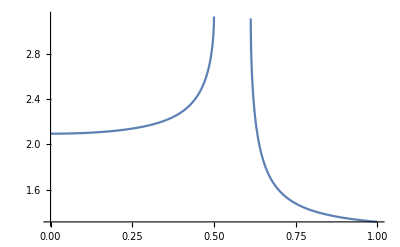

```mathematica
Plot[ArcCos[(-1+2 b^2)/(√((2-6 b^2)^2))],{b,0,1}]
```

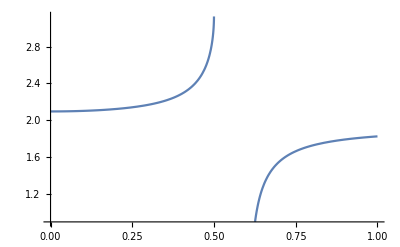

```mathematica
Plot[ArcCos[(-1+2 b^2)/(2-6 b^2)],{b,0,1}]
```

```mathematica
(*Apparently it matters how to resolve the square root*)
```

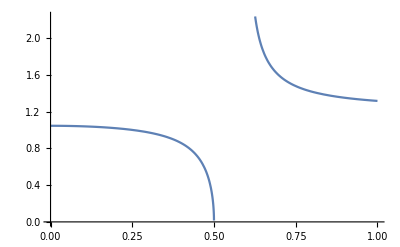

```mathematica
Plot[ArcCos[(-1+2 b^2)/(-(2-6 b^2))],{b,0,1}]
```

```mathematica
(*Apparently it matters how to resolve the square root*)
```

```mathematica
Solve[ 3  ArcCos[(-1+2 b^2)/(√((2-6 b^2)^2))]==2 π , b]
```

{{b→0},{b→-√(2/5)},{b→√(2/5)}}

```mathematica
ArcCos[costh[1,1,1,√(2/5),1,1,√(2/5),1,√(2/5),√(2/5)]]//Simplify
```

(2 π)/3

```mathematica
ArcCos[1/(2 √(-2+6 b^2))]/.{b->√(2/5)}//Simplify
```

ArcCos[(√(5/2))/2]

```mathematica
%//N
```

0.659058

```mathematica
ArcCos[1/4]//N
```

1.31812

```mathematica
(*indeed there are 2 simplices at a boundary triangle *)
```

```mathematica
(*  "1" is the bulk vertex; 12= triangle 345; 23=triangle 145 *)

{FD[ArcCos[√(5/8)],ArcCos[√(5/8)],ArcCos[√(5/8)],ArcCos[√(5/8)],(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3]}//MatrixForm
```

((√15)/32 | (√15)/32 | (√15)/32 | (√15)/32 | (√3)/32 | (√3)/32 | (√3)/32 | (√3)/32 | (√3)/32 | (√3)/32)

```mathematica
Hess[ArcCos[√(5/8)],ArcCos[√(5/8)],ArcCos[√(5/8)],ArcCos[√(5/8)],(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3]//Simplify//MatrixForm
```

(-7/32 | 3/32 | 3/32 | 3/32 | -(3 √5)/32 | -(3 √5)/32 | -(3 √5)/32 | 0 | 0 | 0
3/32 | -7/32 | 3/32 | 3/32 | -(3 √5)/32 | 0 | 0 | -(3 √5)/32 | -(3 √5)/32 | 0
3/32 | 3/32 | -7/32 | 3/32 | 0 | -(3 √5)/32 | 0 | -(3 √5)/32 | 0 | -(3 √5)/32
3/32 | 3/32 | 3/32 | -7/32 | 0 | 0 | -(3 √5)/32 | 0 | -(3 √5)/32 | -(3 √5)/32
-(3 √5)/32 | -(3 √5)/32 | 0 | 0 | -7/32 | -3/32 | -3/32 | -3/32 | -3/32 | 0
-(3 √5)/32 | 0 | -(3 √5)/32 | 0 | -3/32 | -7/32 | -3/32 | -3/32 | 0 | -3/32
-(3 √5)/32 | 0 | 0 | -(3 √5)/32 | -3/32 | -3/32 | -7/32 | 0 | -3/32 | -3/32
0 | -(3 √5)/32 | -(3 √5)/32 | 0 | -3/32 | -3/32 | 0 | -7/32 | -3/32 | -3/32
0 | -(3 √5)/32 | 0 | -(3 √5)/32 | -3/32 | 0 | -3/32 | -3/32 | -7/32 | -3/32
0 | 0 | -(3 √5)/32 | -(3 √5)/32 | 0 | -3/32 | -3/32 | -3/32 | -3/32 | -7/32)

```mathematica
Det[({{-7/32, 3/32, 3/32, 3/32, -(3 √5)/32, -(3 √5)/32, -(3 √5)/32, 0, 0, 0}, {3/32, -7/32, 3/32, 3/32, -(3 √5)/32, 0, 0, -(3 √5)/32, -(3 √5)/32, 0}, {3/32, 3/32, -7/32, 3/32, 0, -(3 √5)/32, 0, -(3 √5)/32, 0, -(3 √5)/32}, {3/32, 3/32, 3/32, -7/32, 0, 0, -(3 √5)/32, 0, -(3 √5)/32, -(3 √5)/32}, {-(3 √5)/32, -(3 √5)/32, 0, 0, -7/32, -3/32, -3/32, -3/32, -3/32, 0}, {-(3 √5)/32, 0, -(3 √5)/32, 0, -3/32, -7/32, -3/32, -3/32, 0, -3/32}, {-(3 √5)/32, 0, 0, -(3 √5)/32, -3/32, -3/32, -7/32, 0, -3/32, -3/32}, {0, -(3 √5)/32, -(3 √5)/32, 0, -3/32, -3/32, 0, -7/32, -3/32, -3/32}, {0, -(3 √5)/32, 0, -(3 √5)/32, -3/32, 0, -3/32, -3/32, -7/32, -3/32}, {0, 0, -(3 √5)/32, -(3 √5)/32, 0, -3/32, -3/32, -3/32, -3/32, -7/32}})]
```

9625/4398046511104

```mathematica
(*EOMs for Lambda*)
```

```mathematica
Solve[Ar[1,1,1]== λ   (√15)/32,λ]
```

{{λ→8/(√5)}}

```mathematica
Solve[Ar[1,√(2/5),√(2/5)]== λ   (√3)/32,λ]
```

{{λ→8/(√5)}}

```mathematica
8/(√5)({{-7/32, 3/32, 3/32, 3/32, -(3 √5)/32, -(3 √5)/32, -(3 √5)/32, 0, 0, 0}, {3/32, -7/32, 3/32, 3/32, -(3 √5)/32, 0, 0, -(3 √5)/32, -(3 √5)/32, 0}, {3/32, 3/32, -7/32, 3/32, 0, -(3 √5)/32, 0, -(3 √5)/32, 0, -(3 √5)/32}, {3/32, 3/32, 3/32, -7/32, 0, 0, -(3 √5)/32, 0, -(3 √5)/32, -(3 √5)/32}, {-(3 √5)/32, -(3 √5)/32, 0, 0, -7/32, -3/32, -3/32, -3/32, -3/32, 0}, {-(3 √5)/32, 0, -(3 √5)/32, 0, -3/32, -7/32, -3/32, -3/32, 0, -3/32}, {-(3 √5)/32, 0, 0, -(3 √5)/32, -3/32, -3/32, -7/32, 0, -3/32, -3/32}, {0, -(3 √5)/32, -(3 √5)/32, 0, -3/32, -3/32, 0, -7/32, -3/32, -3/32}, {0, -(3 √5)/32, 0, -(3 √5)/32, -3/32, 0, -3/32, -3/32, -7/32, -3/32}, {0, 0, -(3 √5)/32, -(3 √5)/32, 0, -3/32, -3/32, -3/32, -3/32, -7/32}})//MatrixForm
```

(-7/(4 √5) | 3/(4 √5) | 3/(4 √5) | 3/(4 √5) | -3/4 | -3/4 | -3/4 | 0 | 0 | 0
3/(4 √5) | -7/(4 √5) | 3/(4 √5) | 3/(4 √5) | -3/4 | 0 | 0 | -3/4 | -3/4 | 0
3/(4 √5) | 3/(4 √5) | -7/(4 √5) | 3/(4 √5) | 0 | -3/4 | 0 | -3/4 | 0 | -3/4
3/(4 √5) | 3/(4 √5) | 3/(4 √5) | -7/(4 √5) | 0 | 0 | -3/4 | 0 | -3/4 | -3/4
-3/4 | -3/4 | 0 | 0 | -7/(4 √5) | -3/(4 √5) | -3/(4 √5) | -3/(4 √5) | -3/(4 √5) | 0
-3/4 | 0 | -3/4 | 0 | -3/(4 √5) | -7/(4 √5) | -3/(4 √5) | -3/(4 √5) | 0 | -3/(4 √5)
-3/4 | 0 | 0 | -3/4 | -3/(4 √5) | -3/(4 √5) | -7/(4 √5) | 0 | -3/(4 √5) | -3/(4 √5)
0 | -3/4 | -3/4 | 0 | -3/(4 √5) | -3/(4 √5) | 0 | -7/(4 √5) | -3/(4 √5) | -3/(4 √5)
0 | -3/4 | 0 | -3/4 | -3/(4 √5) | 0 | -3/(4 √5) | -3/(4 √5) | -7/(4 √5) | -3/(4 √5)
0 | 0 | -3/4 | -3/4 | 0 | -3/(4 √5) | -3/(4 √5) | -3/(4 √5) | -3/(4 √5) | -7/(4 √5))

```mathematica
(*Solve for angle and lambda perturbative variables. The following is the quadratic matrix to be inverted*)
```

```mathematica
HessT:=({{0, (√15)/32, (√15)/32, (√15)/32, (√15)/32, (√3)/32, (√3)/32, (√3)/32, (√3)/32, (√3)/32, (√3)/32}, {(√15)/32, -7/(4 √5), 3/(4 √5), 3/(4 √5), 3/(4 √5), -3/4, -3/4, -3/4, 0, 0, 0}, {(√15)/32, 3/(4 √5), -7/(4 √5), 3/(4 √5), 3/(4 √5), -3/4, 0, 0, -3/4, -3/4, 0}, {(√15)/32, 3/(4 √5), 3/(4 √5), -7/(4 √5), 3/(4 √5), 0, -3/4, 0, -3/4, 0, -3/4}, {(√15)/32, 3/(4 √5), 3/(4 √5), 3/(4 √5), -7/(4 √5), 0, 0, -3/4, 0, -3/4, -3/4}, {(√3)/32, -3/4, -3/4, 0, 0, -7/(4 √5), -3/(4 √5), -3/(4 √5), -3/(4 √5), -3/(4 √5), 0}, {(√3)/32, -3/4, 0, -3/4, 0, -3/(4 √5), -7/(4 √5), -3/(4 √5), -3/(4 √5), 0, -3/(4 √5)}, {(√3)/32, -3/4, 0, 0, -3/4, -3/(4 √5), -3/(4 √5), -7/(4 √5), 0, -3/(4 √5), -3/(4 √5)}, {(√3)/32, 0, -3/4, -3/4, 0, -3/(4 √5), -3/(4 √5), 0, -7/(4 √5), -3/(4 √5), -3/(4 √5)}, {(√3)/32, 0, -3/4, 0, -3/4, -3/(4 √5), 0, -3/(4 √5), -3/(4 √5), -7/(4 √5), -3/(4 √5)}, {(√3)/32, 0, 0, -3/4, -3/4, 0, -3/(4 √5), -3/(4 √5), -3/(4 √5), -3/(4 √5), -7/(4 √5)}})
```

```mathematica
Det[HessT]
```

-3/(2621440 √5)

```mathematica
(*Use "opposite" notation also for areas; x=dihedral angles*)
```

```mathematica
Inverse[HessT]//Simplify//MatrixForm
```

(-9856/(3 √5) | 40 √(5/3) | 40 √(5/3) | 40 √(5/3) | 40 √(5/3) | -128/(√3) | -128/(√3) | -128/(√3) | -128/(√3) | -128/(√3) | -128/(√3)
40 √(5/3) | 3/(2 √5) | -11/(2 √5) | -11/(2 √5) | -11/(2 √5) | 1 | 1 | 1 | 4 | 4 | 4
40 √(5/3) | -11/(2 √5) | 3/(2 √5) | -11/(2 √5) | -11/(2 √5) | 1 | 4 | 4 | 1 | 1 | 4
40 √(5/3) | -11/(2 √5) | -11/(2 √5) | 3/(2 √5) | -11/(2 √5) | 4 | 1 | 4 | 1 | 4 | 1
40 √(5/3) | -11/(2 √5) | -11/(2 √5) | -11/(2 √5) | 3/(2 √5) | 4 | 4 | 1 | 4 | 1 | 1
-128/(√3) | 1 | 1 | 4 | 4 | -2 √5 | -√5 | -√5 | -√5 | -√5 | -4 √5
-128/(√3) | 1 | 4 | 1 | 4 | -√5 | -2 √5 | -√5 | -√5 | -4 √5 | -√5
-128/(√3) | 1 | 4 | 4 | 1 | -√5 | -√5 | -2 √5 | -4 √5 | -√5 | -√5
-128/(√3) | 4 | 1 | 1 | 4 | -√5 | -√5 | -4 √5 | -2 √5 | -√5 | -√5
-128/(√3) | 4 | 1 | 4 | 1 | -√5 | -4 √5 | -√5 | -√5 | -2 √5 | -√5
-128/(√3) | 4 | 4 | 1 | 1 | -4 √5 | -√5 | -√5 | -√5 | -√5 | -2 √5)

```mathematica
NullSpace[({{3/(2 √5), -11/(2 √5), -11/(2 √5), -11/(2 √5), 1, 1, 1, 4, 4, 4}, {-11/(2 √5), 3/(2 √5), -11/(2 √5), -11/(2 √5), 1, 4, 4, 1, 1, 4}, {-11/(2 √5), -11/(2 √5), 3/(2 √5), -11/(2 √5), 4, 1, 4, 1, 4, 1}, {-11/(2 √5), -11/(2 √5), -11/(2 √5), 3/(2 √5), 4, 4, 1, 4, 1, 1}, {1, 1, 4, 4, -2 √5, -√5, -√5, -√5, -√5, -4 √5}, {1, 4, 1, 4, -√5, -2 √5, -√5, -√5, -4 √5, -√5}, {1, 4, 4, 1, -√5, -√5, -2 √5, -4 √5, -√5, -√5}, {4, 1, 1, 4, -√5, -√5, -4 √5, -2 √5, -√5, -√5}, {4, 1, 4, 1, -√5, -4 √5, -√5, -√5, -2 √5, -√5}, {4, 4, 1, 1, -4 √5, -√5, -√5, -√5, -√5, -2 √5}})]
```

{{√5,√5,√5,√5,1,1,1,1,1,1}}

```mathematica
Solve[ ({{0}, {a12}, {a13}, {a14}, {a15}, {a23}, {a24}, {a25}, {a34}, {a35}, {a45}})==HessT.({{λ}, {x12}, {x13}, {x14}, {x15}, {x23}, {x24}, {x25}, {x34}, {x35}, {x45}}), {λ,x12,x13,x14,x15,x23,x24,x25,x34,x35,x45}]//Simplify
```

{{λ→(8 (5 √5 a12+5 √5 a13+5 √5 a14+5 √5 a15-16 a23-16 a24-16 a25-16 a34-16 a35-16 a45))/(√3),x12→(3 a12)/(2 √5)-(11 a13)/(2 √5)-(11 a14)/(2 √5)-(11 a15)/(2 √5)+a23+a24+a25+4 a34+4 a35+4 a45,x13→-(11 a12)/(2 √5)+(3 a13)/(2 √5)-(11 a14)/(2 √5)-(11 a15)/(2 √5)+a23+4 a24+4 a25+a34+a35+4 a45,x14→-(11 a12)/(2 √5)-(11 a13)/(2 √5)+(3 a14)/(2 √5)-(11 a15)/(2 √5)+4 a23+a24+4 a25+a34+4 a35+a45,x15→-(11 a12)/(2 √5)-(11 a13)/(2 √5)-(11 a14)/(2 √5)+(3 a15)/(2 √5)+4 a23+4 a24+a25+4 a34+a35+a45,x23→a12+a13+4 a14+4 a15-2 √5 a23-√5 a24-√5 a25-√5 a34-√5 a35-4 √5 a45,x24→a12+4 a13+a14+4 a15-√5 a23-2 √5 a24-√5 a25-√5 a34-4 √5 a35-√5 a45,x25→a12+4 a13+4 a14+a15-√5 a23-√5 a24-2 √5 a25-4 √5 a34-√5 a35-√5 a45,x34→4 a12+a13+a14+4 a15-√5 a23-√5 a24-4 √5 a25-2 √5 a34-√5 a35-√5 a45,x35→4 a12+a13+4 a14+a15-√5 a23-4 √5 a24-√5 a25-√5 a34-2 √5 a35-√5 a45,x45→4 a12+4 a13+a14+a15-4 √5 a23-√5 a24-√5 a25-√5 a34-√5 a35-2 √5 a45}}

```mathematica
(*action contribution from one simplex*)
```

```mathematica
S1:=(-Transpose[ ({{0}, {a12}, {a13}, {a14}, {a15}, {a23}, {a24}, {a25}, {a34}, {a35}, {a45}})].({{λ}, {x12}, {x13}, {x14}, {x15}, {x23}, {x24}, {x25}, {x34}, {x35}, {x45}})+ 1/2 Transpose[({{λ}, {x12}, {x13}, {x14}, {x15}, {x23}, {x24}, {x25}, {x34}, {x35}, {x45}})].HessT.({{λ}, {x12}, {x13}, {x14}, {x15}, {x23}, {x24}, {x25}, {x34}, {x35}, {x45}}))[[1,1]]//Simplify
```

```mathematica
S1/.{λ->1/(√3)8 (5 √5 a12+5 √5 a13+5 √5 a14+5 √5 a15-16 a23-16 a24-16 a25-16 a34-16 a35-16 a45),x12->(3 a12)/(2 √5)-(11 a13)/(2 √5)-(11 a14)/(2 √5)-(11 a15)/(2 √5)+a23+a24+a25+4 a34+4 a35+4 a45,x13->-(11 a12)/(2 √5)+(3 a13)/(2 √5)-(11 a14)/(2 √5)-(11 a15)/(2 √5)+a23+4 a24+4 a25+a34+a35+4 a45,x14->-(11 a12)/(2 √5)-(11 a13)/(2 √5)+(3 a14)/(2 √5)-(11 a15)/(2 √5)+4 a23+a24+4 a25+a34+4 a35+a45,x15->-(11 a12)/(2 √5)-(11 a13)/(2 √5)-(11 a14)/(2 √5)+(3 a15)/(2 √5)+4 a23+4 a24+a25+4 a34+a35+a45,x23->a12+a13+4 a14+4 a15-2 √5 a23-√5 a24-√5 a25-√5 a34-√5 a35-4 √5 a45,x24->a12+4 a13+a14+4 a15-√5 a23-2 √5 a24-√5 a25-√5 a34-4 √5 a35-√5 a45,x25->a12+4 a13+4 a14+a15-√5 a23-√5 a24-2 √5 a25-4 √5 a34-√5 a35-√5 a45,x34->4 a12+a13+a14+4 a15-√5 a23-√5 a24-4 √5 a25-2 √5 a34-√5 a35-√5 a45,x35->4 a12+a13+4 a14+a15-√5 a23-4 √5 a24-√5 a25-√5 a34-2 √5 a35-√5 a45,x45->4 a12+4 a13+a14+a15-4 √5 a23-√5 a24-√5 a25-√5 a34-√5 a35-2 √5 a45}//Simplify
```

```mathematica
S2:=-(3 a12^2)/(4 √5)-(3 a13^2)/(4 √5)-(3 a14^2)/(4 √5)+(11 a14 a15)/(2 √5)-(3 a15^2)/(4 √5)-4 a14 a23-4 a15 a23+√5 a23^2-a14 a24-4 a15 a24+√5 a23 a24+√5 a24^2-4 a14 a25-a15 a25+√5 a23 a25+√5 a24 a25+√5 a25^2-a14 a34-4 a15 a34+√5 a23 a34+√5 a24 a34+4 √5 a25 a34+√5 a34^2-4 a14 a35-a15 a35+√5 a23 a35+4 √5 a24 a35+√5 a25 a35+√5 a34 a35+√5 a35^2+a12 ((11 a13)/(2 √5)+(11 a14)/(2 √5)+(11 a15)/(2 √5)-a23-a24-a25-4 a34-4 a35-4 a45)-a14 a45-a15 a45+4 √5 a23 a45+√5 a24 a45+√5 a25 a45+√5 a34 a45+√5 a35 a45+√5 a45^2+1/10 a13 (11 √5 a14+11 √5 a15-10 (a23+4 a24+4 a25+a34+a35+4 a45))
```

```mathematica
Extract[CoefficientArrays[S2,{a12,a13,a14,a15,a23,a24,a25,a34,a35,a45},"Symmetric"->True]//Normal,3]//MatrixForm
```

```mathematica
SA1:=({{-3/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), -1/2, -1/2, -1/2, -2, -2, -2}, {11/(4 √5), -3/(4 √5), 11/(4 √5), 11/(4 √5), -1/2, -2, -2, -1/2, -1/2, -2}, {11/(4 √5), 11/(4 √5), -3/(4 √5), 11/(4 √5), -2, -1/2, -2, -1/2, -2, -1/2}, {11/(4 √5), 11/(4 √5), 11/(4 √5), -3/(4 √5), -2, -2, -1/2, -2, -1/2, -1/2}, {-1/2, -1/2, -2, -2, √5, (√5)/2, (√5)/2, (√5)/2, (√5)/2, 2 √5}, {-1/2, -2, -1/2, -2, (√5)/2, √5, (√5)/2, (√5)/2, 2 √5, (√5)/2}, {-1/2, -2, -2, -1/2, (√5)/2, (√5)/2, √5, 2 √5, (√5)/2, (√5)/2}, {-2, -1/2, -1/2, -2, (√5)/2, (√5)/2, 2 √5, √5, (√5)/2, (√5)/2}, {-2, -1/2, -2, -1/2, (√5)/2, 2 √5, (√5)/2, (√5)/2, √5, (√5)/2}, {-2, -2, -1/2, -1/2, 2 √5, (√5)/2, (√5)/2, (√5)/2, (√5)/2, √5}})
```

```mathematica
NullSpace[SA1]
```

{{√5,√5,√5,√5,1,1,1,1,1,1}}

```mathematica
(*Compare to submatrix of inverse HessT*)
```

```mathematica
SA1+1/2({{3/(2 √5), -11/(2 √5), -11/(2 √5), -11/(2 √5), 1, 1, 1, 4, 4, 4}, {-11/(2 √5), 3/(2 √5), -11/(2 √5), -11/(2 √5), 1, 4, 4, 1, 1, 4}, {-11/(2 √5), -11/(2 √5), 3/(2 √5), -11/(2 √5), 4, 1, 4, 1, 4, 1}, {-11/(2 √5), -11/(2 √5), -11/(2 √5), 3/(2 √5), 4, 4, 1, 4, 1, 1}, {1, 1, 4, 4, -2 √5, -√5, -√5, -√5, -√5, -4 √5}, {1, 4, 1, 4, -√5, -2 √5, -√5, -√5, -4 √5, -√5}, {1, 4, 4, 1, -√5, -√5, -2 √5, -4 √5, -√5, -√5}, {4, 1, 1, 4, -√5, -√5, -4 √5, -2 √5, -√5, -√5}, {4, 1, 4, 1, -√5, -4 √5, -√5, -√5, -2 √5, -√5}, {4, 4, 1, 1, -4 √5, -√5, -√5, -√5, -√5, -2 √5}})//Simplify
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
(*There are 5 simplices. Let the vertices be 1 to 6 with 1 the bulk vertex. Change to triple vertex labels for areas. There should be 20 areas -- 10 boundary and 10 bulk*)
```

```mathematica
S51:=Transpose[({{a345}, {a245}, {a235}, {a234}, {a145}, {a135}, {a134}, {a125}, {a124}, {a123}})].SA1.({{a345}, {a245}, {a235}, {a234}, {a145}, {a135}, {a134}, {a125}, {a124}, {a123}})+Transpose[({{a346}, {a246}, {a236}, {a234}, {a146}, {a136}, {a134}, {a126}, {a124}, {a123}})].SA1.({{a346}, {a246}, {a236}, {a234}, {a146}, {a136}, {a134}, {a126}, {a124}, {a123}})+Transpose[({{a356}, {a256}, {a236}, {a235}, {a156}, {a136}, {a135}, {a126}, {a125}, {a123}})].SA1.({{a356}, {a256}, {a236}, {a235}, {a156}, {a136}, {a135}, {a126}, {a125}, {a123}})+Transpose[({{a456}, {a256}, {a246}, {a245}, {a156}, {a146}, {a145}, {a126}, {a125}, {a124}})].SA1.({{a456}, {a256}, {a246}, {a245}, {a156}, {a146}, {a145}, {a126}, {a125}, {a124}})s+Transpose[({{a456}, {a356}, {a346}, {a345}, {a156}, {a146}, {a145}, {a136}, {a135}, {a134}})].SA1.({{a456}, {a356}, {a346}, {a345}, {a156}, {a146}, {a145}, {a136}, {a135}, {a134}})
```

```mathematica
S51[[1,1]]//Simplify
```

```mathematica
S51A:=3 √5 a123^2+3 √5 a124^2+2 a123 (√5 a124+√5 a125+√5 a126+√5 a134+√5 a135+√5 a136+2 √5 a145+2 √5 a146+2 √5 a156-a234-a235-a236-2 a245-2 a246-2 a256-2 a345-2 a346-2 a356)+2 a124 (√5 a125+√5 a126+√5 a134+2 √5 a135+2 √5 a136+√5 a145+√5 a146+2 √5 a156-a234-2 a235-2 a236-a245-a246-2 a256-2 a345-2 a346-2 a456)+1/10 (30 √5 a125^2+30 √5 a126^2+30 √5 a134^2+20 √5 a134 a135+30 √5 a135^2+20 √5 a134 a136+20 √5 a135 a136+30 √5 a136^2+20 √5 a134 a145+20 √5 a135 a145+40 √5 a136 a145+30 √5 a145^2+20 √5 a134 a146+40 √5 a135 a146+20 √5 a136 a146+20 √5 a145 a146+30 √5 a146^2+40 √5 a134 a156+20 √5 a135 a156+20 √5 a136 a156+20 √5 a145 a156+20 √5 a146 a156+30 √5 a156^2-20 a134 a234-40 a135 a234-40 a136 a234-40 a145 a234-40 a146 a234-3 √5 a234^2-40 a134 a235-20 a135 a235-40 a136 a235-40 a145 a235-40 a156 a235+11 √5 a234 a235-3 √5 a235^2-40 a134 a236-40 a135 a236-20 a136 a236-40 a146 a236-40 a156 a236+11 √5 a234 a236+11 √5 a235 a236-3 √5 a236^2-40 a134 a245-40 a135 a245-20 a145 a245-40 a146 a245-40 a156 a245+11 √5 a234 a245+11 √5 a235 a245-3 √5 a245^2-40 a134 a246-40 a136 a246-40 a145 a246-20 a146 a246-40 a156 a246+11 √5 a234 a246+11 √5 a236 a246+11 √5 a245 a246-3 √5 a246^2-40 a135 a256-40 a136 a256-40 a145 a256-40 a146 a256-20 a156 a256+11 √5 a235 a256+11 √5 a236 a256+11 √5 a245 a256+11 √5 a246 a256-3 √5 a256^2-20 a134 a345-20 a135 a345-40 a136 a345-20 a145 a345-40 a146 a345-40 a156 a345+11 √5 a234 a345+11 √5 a235 a345+11 √5 a245 a345-3 √5 a345^2-20 a134 a346-40 a135 a346-20 a136 a346-40 a145 a346-20 a146 a346-40 a156 a346+11 √5 a234 a346+11 √5 a236 a346+11 √5 a246 a346+11 √5 a345 a346-3 √5 a346^2-40 a134 a356-20 a135 a356-20 a136 a356-40 a145 a356-40 a146 a356-20 a156 a356+11 √5 a235 a356+11 √5 a236 a356+11 √5 a256 a356+11 √5 a345 a356+11 √5 a346 a356-3 √5 a356^2+20 a125 (√5 a126+2 √5 a134+√5 a135+2 √5 a136+√5 a145+2 √5 a146+√5 a156-2 a234-a235-2 a236-a245-2 a246-a256-2 a345-2 a356-2 a456)+20 a126 (2 √5 a134+2 √5 a135+√5 a136+2 √5 a145+√5 a146+√5 a156-2 a234-2 a235-a236-2 a245-a246-a256-2 a346-2 a356-2 a456)-40 a134 a456-40 a135 a456-40 a136 a456-20 a145 a456-20 a146 a456-20 a156 a456+11 √5 a245 a456+11 √5 a246 a456+11 √5 a256 a456+11 √5 a345 a456+11 √5 a346 a456+11 √5 a356 a456-3 √5 a456^2)
```

```mathematica
(*Note that 'triple vertex' ordering is different from 'two vertex ordering'}
```

```mathematica
Extract[CoefficientArrays[S51A,{a123,a124,a125,a126,a134,a135,a136,a145,a146,a156,a234,a235,a236,a245,a246,a256,a345,a346,a356,a456},"Symmetric"->True]//Normal,3]//MatrixForm
```

(3 √5 | √5 | √5 | √5 | √5 | √5 | √5 | 2 √5 | 2 √5 | 2 √5 | -1 | -1 | -1 | -2 | -2 | -2 | -2 | -2 | -2 | 0
√5 | 3 √5 | √5 | √5 | √5 | 2 √5 | 2 √5 | √5 | √5 | 2 √5 | -1 | -2 | -2 | -1 | -1 | -2 | -2 | -2 | 0 | -2
√5 | √5 | 3 √5 | √5 | 2 √5 | √5 | 2 √5 | √5 | 2 √5 | √5 | -2 | -1 | -2 | -1 | -2 | -1 | -2 | 0 | -2 | -2
√5 | √5 | √5 | 3 √5 | 2 √5 | 2 √5 | √5 | 2 √5 | √5 | √5 | -2 | -2 | -1 | -2 | -1 | -1 | 0 | -2 | -2 | -2
√5 | √5 | 2 √5 | 2 √5 | 3 √5 | √5 | √5 | √5 | √5 | 2 √5 | -1 | -2 | -2 | -2 | -2 | 0 | -1 | -1 | -2 | -2
√5 | 2 √5 | √5 | 2 √5 | √5 | 3 √5 | √5 | √5 | 2 √5 | √5 | -2 | -1 | -2 | -2 | 0 | -2 | -1 | -2 | -1 | -2
√5 | 2 √5 | 2 √5 | √5 | √5 | √5 | 3 √5 | 2 √5 | √5 | √5 | -2 | -2 | -1 | 0 | -2 | -2 | -2 | -1 | -1 | -2
2 √5 | √5 | √5 | 2 √5 | √5 | √5 | 2 √5 | 3 √5 | √5 | √5 | -2 | -2 | 0 | -1 | -2 | -2 | -1 | -2 | -2 | -1
2 √5 | √5 | 2 √5 | √5 | √5 | 2 √5 | √5 | √5 | 3 √5 | √5 | -2 | 0 | -2 | -2 | -1 | -2 | -2 | -1 | -2 | -1
2 √5 | 2 √5 | √5 | √5 | 2 √5 | √5 | √5 | √5 | √5 | 3 √5 | 0 | -2 | -2 | -2 | -2 | -1 | -2 | -2 | -1 | -1
-1 | -1 | -2 | -2 | -1 | -2 | -2 | -2 | -2 | 0 | -3/(2 √5) | 11/(4 √5) | 11/(4 √5) | 11/(4 √5) | 11/(4 √5) | 0 | 11/(4 √5) | 11/(4 √5) | 0 | 0
-1 | -2 | -1 | -2 | -2 | -1 | -2 | -2 | 0 | -2 | 11/(4 √5) | -3/(2 √5) | 11/(4 √5) | 11/(4 √5) | 0 | 11/(4 √5) | 11/(4 √5) | 0 | 11/(4 √5) | 0
-1 | -2 | -2 | -1 | -2 | -2 | -1 | 0 | -2 | -2 | 11/(4 √5) | 11/(4 √5) | -3/(2 √5) | 0 | 11/(4 √5) | 11/(4 √5) | 0 | 11/(4 √5) | 11/(4 √5) | 0
-2 | -1 | -1 | -2 | -2 | -2 | 0 | -1 | -2 | -2 | 11/(4 √5) | 11/(4 √5) | 0 | -3/(2 √5) | 11/(4 √5) | 11/(4 √5) | 11/(4 √5) | 0 | 0 | 11/(4 √5)
-2 | -1 | -2 | -1 | -2 | 0 | -2 | -2 | -1 | -2 | 11/(4 √5) | 0 | 11/(4 √5) | 11/(4 √5) | -3/(2 √5) | 11/(4 √5) | 0 | 11/(4 √5) | 0 | 11/(4 √5)
-2 | -2 | -1 | -1 | 0 | -2 | -2 | -2 | -2 | -1 | 0 | 11/(4 √5) | 11/(4 √5) | 11/(4 √5) | 11/(4 √5) | -3/(2 √5) | 0 | 0 | 11/(4 √5) | 11/(4 √5)
-2 | -2 | -2 | 0 | -1 | -1 | -2 | -1 | -2 | -2 | 11/(4 √5) | 11/(4 √5) | 0 | 11/(4 √5) | 0 | 0 | -3/(2 √5) | 11/(4 √5) | 11/(4 √5) | 11/(4 √5)
-2 | -2 | 0 | -2 | -1 | -2 | -1 | -2 | -1 | -2 | 11/(4 √5) | 0 | 11/(4 √5) | 0 | 11/(4 √5) | 0 | 11/(4 √5) | -3/(2 √5) | 11/(4 √5) | 11/(4 √5)
-2 | 0 | -2 | -2 | -2 | -1 | -1 | -2 | -2 | -1 | 0 | 11/(4 √5) | 11/(4 √5) | 0 | 0 | 11/(4 √5) | 11/(4 √5) | 11/(4 √5) | -3/(2 √5) | 11/(4 √5)
0 | -2 | -2 | -2 | -2 | -2 | -2 | -1 | -1 | -1 | 0 | 0 | 0 | 11/(4 √5) | 11/(4 √5) | 11/(4 √5) | 11/(4 √5) | 11/(4 √5) | 11/(4 √5) | -3/(2 √5))

```mathematica
(*Nullspace of bulk variables*)
```

```mathematica
1/(√5)({{3 √5, √5, √5, √5, √5, √5, √5, 2 √5, 2 √5, 2 √5}, {√5, 3 √5, √5, √5, √5, 2 √5, 2 √5, √5, √5, 2 √5}, {√5, √5, 3 √5, √5, 2 √5, √5, 2 √5, √5, 2 √5, √5}, {√5, √5, √5, 3 √5, 2 √5, 2 √5, √5, 2 √5, √5, √5}, {√5, √5, 2 √5, 2 √5, 3 √5, √5, √5, √5, √5, 2 √5}, {√5, 2 √5, √5, 2 √5, √5, 3 √5, √5, √5, 2 √5, √5}, {√5, 2 √5, 2 √5, √5, √5, √5, 3 √5, 2 √5, √5, √5}, {2 √5, √5, √5, 2 √5, √5, √5, 2 √5, 3 √5, √5, √5}, {2 √5, √5, 2 √5, √5, √5, 2 √5, √5, √5, 3 √5, √5}, {2 √5, 2 √5, √5, √5, 2 √5, √5, √5, √5, √5, 3 √5}})//MatrixForm
```

(3 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2
1 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2
1 | 1 | 3 | 1 | 2 | 1 | 2 | 1 | 2 | 1
1 | 1 | 1 | 3 | 2 | 2 | 1 | 2 | 1 | 1
1 | 1 | 2 | 2 | 3 | 1 | 1 | 1 | 1 | 2
1 | 2 | 1 | 2 | 1 | 3 | 1 | 1 | 2 | 1
1 | 2 | 2 | 1 | 1 | 1 | 3 | 2 | 1 | 1
2 | 1 | 1 | 2 | 1 | 1 | 2 | 3 | 1 | 1
2 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 3 | 1
2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 3)

```mathematica
NullSpace[({{3, 1, 1, 1, 1, 1, 1, 2, 2, 2}, {1, 3, 1, 1, 1, 2, 2, 1, 1, 2}, {1, 1, 3, 1, 2, 1, 2, 1, 2, 1}, {1, 1, 1, 3, 2, 2, 1, 2, 1, 1}, {1, 1, 2, 2, 3, 1, 1, 1, 1, 2}, {1, 2, 1, 2, 1, 3, 1, 1, 2, 1}, {1, 2, 2, 1, 1, 1, 3, 2, 1, 1}, {2, 1, 1, 2, 1, 1, 2, 3, 1, 1}, {2, 1, 2, 1, 1, 2, 1, 1, 3, 1}, {2, 2, 1, 1, 2, 1, 1, 1, 1, 3}})]
```

{{-1,-1,1,1,-2,0,0,0,0,2},{-1,1,-1,1,0,-2,0,0,2,0},{-1,-1,-1,-3,2,2,0,2,0,0},{0,-1,-1,-1,1,1,1,0,0,0}}

```mathematica
(*Would have expected more null vectors - this way it is exactly as in Regge calculus!*)(*If this is correct it could correspond to one symmetry per edge minus a vertex redundancy  OR 4 per vertex *)
```

```mathematica
NullSpace[({{3 √5, √5, √5, √5, √5, √5, √5, 2 √5, 2 √5, 2 √5, -1, -1, -1, -2, -2, -2, -2, -2, -2, 0}, {√5, 3 √5, √5, √5, √5, 2 √5, 2 √5, √5, √5, 2 √5, -1, -2, -2, -1, -1, -2, -2, -2, 0, -2}, {√5, √5, 3 √5, √5, 2 √5, √5, 2 √5, √5, 2 √5, √5, -2, -1, -2, -1, -2, -1, -2, 0, -2, -2}, {√5, √5, √5, 3 √5, 2 √5, 2 √5, √5, 2 √5, √5, √5, -2, -2, -1, -2, -1, -1, 0, -2, -2, -2}, {√5, √5, 2 √5, 2 √5, 3 √5, √5, √5, √5, √5, 2 √5, -1, -2, -2, -2, -2, 0, -1, -1, -2, -2}, {√5, 2 √5, √5, 2 √5, √5, 3 √5, √5, √5, 2 √5, √5, -2, -1, -2, -2, 0, -2, -1, -2, -1, -2}, {√5, 2 √5, 2 √5, √5, √5, √5, 3 √5, 2 √5, √5, √5, -2, -2, -1, 0, -2, -2, -2, -1, -1, -2}, {2 √5, √5, √5, 2 √5, √5, √5, 2 √5, 3 √5, √5, √5, -2, -2, 0, -1, -2, -2, -1, -2, -2, -1}, {2 √5, √5, 2 √5, √5, √5, 2 √5, √5, √5, 3 √5, √5, -2, 0, -2, -2, -1, -2, -2, -1, -2, -1}, {2 √5, 2 √5, √5, √5, 2 √5, √5, √5, √5, √5, 3 √5, 0, -2, -2, -2, -2, -1, -2, -2, -1, -1}, {-1, -1, -2, -2, -1, -2, -2, -2, -2, 0, -3/(2 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), 0, 11/(4 √5), 11/(4 √5), 0, 0}, {-1, -2, -1, -2, -2, -1, -2, -2, 0, -2, 11/(4 √5), -3/(2 √5), 11/(4 √5), 11/(4 √5), 0, 11/(4 √5), 11/(4 √5), 0, 11/(4 √5), 0}, {-1, -2, -2, -1, -2, -2, -1, 0, -2, -2, 11/(4 √5), 11/(4 √5), -3/(2 √5), 0, 11/(4 √5), 11/(4 √5), 0, 11/(4 √5), 11/(4 √5), 0}, {-2, -1, -1, -2, -2, -2, 0, -1, -2, -2, 11/(4 √5), 11/(4 √5), 0, -3/(2 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), 0, 0, 11/(4 √5)}, {-2, -1, -2, -1, -2, 0, -2, -2, -1, -2, 11/(4 √5), 0, 11/(4 √5), 11/(4 √5), -3/(2 √5), 11/(4 √5), 0, 11/(4 √5), 0, 11/(4 √5)}, {-2, -2, -1, -1, 0, -2, -2, -2, -2, -1, 0, 11/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), -3/(2 √5), 0, 0, 11/(4 √5), 11/(4 √5)}, {-2, -2, -2, 0, -1, -1, -2, -1, -2, -2, 11/(4 √5), 11/(4 √5), 0, 11/(4 √5), 0, 0, -3/(2 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5)}, {-2, -2, 0, -2, -1, -2, -1, -2, -1, -2, 11/(4 √5), 0, 11/(4 √5), 0, 11/(4 √5), 0, 11/(4 √5), -3/(2 √5), 11/(4 √5), 11/(4 √5)}, {-2, 0, -2, -2, -2, -1, -1, -2, -2, -1, 0, 11/(4 √5), 11/(4 √5), 0, 0, 11/(4 √5), 11/(4 √5), 11/(4 √5), -3/(2 √5), 11/(4 √5)}, {0, -2, -2, -2, -2, -2, -2, -1, -1, -1, 0, 0, 0, 11/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), -3/(2 √5)}})]
```

{{(√5)/2,(√5)/2,(√5)/2,(√5)/2,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1},{-1/2,-1/2,1/2,1/2,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{-1/2,1/2,-1/2,1/2,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{-1/2,-1/2,-1/2,-3/2,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,-1,-1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(*Check this result. Consider a triangulation with bulk edge but without a vertex: 4-2 configuration*)
```

```mathematica
(**********************************************************************************)
(*4-2 move configuration*)
```

```mathematica
(*Dihedral angle at triangle b,1,1*)
```

```mathematica
ArcCos[costh[1,1,1,1,1,1,1,1,1,b]]//Simplify
```

ArcCos[-(b^2 (-2+b^2))/(2 √(b^4 (-3+b^2)^2))]

```mathematica
(*Dihedral angle at triangle opposite edge b*)
```

```mathematica
ArcCos[costh[b,1,1,1,1,1,1,1,1,1]]//Simplify
```

ArcCos[1-(3 b^2)/4]

```mathematica
(*Dihedral angle at triangle with lenght 1,1,1 sharing one of th vertices of b edge*)
```

```mathematica
ArcCos[costh[1,b,1,1,1,1,1,1,1,1]]//Simplify
```

ArcCos[b^2/(2 √(6 b^2-2 b^4))]

```mathematica
Solve[ 3 ArcCos[-(b^2 (-2+b^2))/(2 √(b^4 (-3+b^2)^2))] == 2 π, b]
```

{{b→-√(5/2)},{b→√(5/2)}}

```mathematica
(*Dihedral angle at triangle b,1,1*)
```

```mathematica
ArcCos[-(b^2 (-2+b^2))/(2 √(b^4 (-3+b^2)^2))]/.{b->√(5/2)}
```

(2 π)/3

```mathematica
(*Dihedral angle at triangle opposite edge b*)
```

```mathematica
ArcCos[1-(3 b^2)/4]/.{b->√(5/2)}
```

ArcCos[-7/8]

```mathematica
(*Dihedral angle at triangle with lenght 1,1,1 sharing one of th vertices of b edge*)
```

```mathematica
ArcCos[b^2/(2 √(6 b^2-2 b^4))]/.{b->√(5/2)}
```

ArcCos[(√(5/2))/2]

```mathematica
FD[ArcCos[-7/8],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],(2 π)/3,(2 π)/3,(2 π)/3]
```

{(√15)/128,(√15)/128,(√15)/128,(√15)/128,(√15)/128,(√15)/128,(√15)/128,(5 √3)/256,(5 √3)/256,(5 √3)/256}

```mathematica
Hess[ArcCos[-7/8],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],(2 π)/3,(2 π)/3,(2 π)/3]//Simplify//MatrixForm
```

(-37/128 | -15/128 | -15/128 | -15/128 | -15/128 | -15/128 | -15/128 | -(9 √5)/128 | -(9 √5)/128 | -(9 √5)/128
-15/128 | -7/128 | -3/64 | -3/64 | 3/128 | 9/128 | 9/128 | -(3 √5)/128 | -(3 √5)/128 | 0
-15/128 | -3/64 | -7/128 | -3/64 | 9/128 | 3/128 | 9/128 | -(3 √5)/128 | 0 | -(3 √5)/128
-15/128 | -3/64 | -3/64 | -7/128 | 9/128 | 9/128 | 3/128 | 0 | -(3 √5)/128 | -(3 √5)/128
-15/128 | 3/128 | 9/128 | 9/128 | -7/128 | -3/64 | -3/64 | -(3 √5)/128 | -(3 √5)/128 | 0
-15/128 | 9/128 | 3/128 | 9/128 | -3/64 | -7/128 | -3/64 | -(3 √5)/128 | 0 | -(3 √5)/128
-15/128 | 9/128 | 9/128 | 3/128 | -3/64 | -3/64 | -7/128 | 0 | -(3 √5)/128 | -(3 √5)/128
-(9 √5)/128 | -(3 √5)/128 | -(3 √5)/128 | 0 | -(3 √5)/128 | -(3 √5)/128 | 0 | -35/256 | -15/256 | -15/256
-(9 √5)/128 | -(3 √5)/128 | 0 | -(3 √5)/128 | -(3 √5)/128 | 0 | -(3 √5)/128 | -15/256 | -35/256 | -15/256
-(9 √5)/128 | 0 | -(3 √5)/128 | -(3 √5)/128 | 0 | -(3 √5)/128 | -(3 √5)/128 | -15/256 | -15/256 | -35/256)

```mathematica
Det[Gr[ArcCos[-7/8],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],ArcCos[(√(5/2))/2],(2 π)/3,(2 π)/3,(2 π)/3]]
```

0

```mathematica
(*EOMs for Lambda*)
```

```mathematica
Solve[ Ar[1,1,1] ==λ (√15)/128]
```

{{λ→32/(√5)}}

```mathematica
Solve[ Ar[1,1,√(5/2)] ==λ (5 √3)/256]
```

{{λ→32/(√5)}}

```mathematica
32/(√5)({{-37/128, -15/128, -15/128, -15/128, -15/128, -15/128, -15/128, -(9 √5)/128, -(9 √5)/128, -(9 √5)/128}, {-15/128, -7/128, -3/64, -3/64, 3/128, 9/128, 9/128, -(3 √5)/128, -(3 √5)/128, 0}, {-15/128, -3/64, -7/128, -3/64, 9/128, 3/128, 9/128, -(3 √5)/128, 0, -(3 √5)/128}, {-15/128, -3/64, -3/64, -7/128, 9/128, 9/128, 3/128, 0, -(3 √5)/128, -(3 √5)/128}, {-15/128, 3/128, 9/128, 9/128, -7/128, -3/64, -3/64, -(3 √5)/128, -(3 √5)/128, 0}, {-15/128, 9/128, 3/128, 9/128, -3/64, -7/128, -3/64, -(3 √5)/128, 0, -(3 √5)/128}, {-15/128, 9/128, 9/128, 3/128, -3/64, -3/64, -7/128, 0, -(3 √5)/128, -(3 √5)/128}, {-(9 √5)/128, -(3 √5)/128, -(3 √5)/128, 0, -(3 √5)/128, -(3 √5)/128, 0, -35/256, -15/256, -15/256}, {-(9 √5)/128, -(3 √5)/128, 0, -(3 √5)/128, -(3 √5)/128, 0, -(3 √5)/128, -15/256, -35/256, -15/256}, {-(9 √5)/128, 0, -(3 √5)/128, -(3 √5)/128, 0, -(3 √5)/128, -(3 √5)/128, -15/256, -15/256, -35/256}})//MatrixForm
```

(-37/(4 √5) | -(3 √5)/4 | -(3 √5)/4 | -(3 √5)/4 | -(3 √5)/4 | -(3 √5)/4 | -(3 √5)/4 | -9/4 | -9/4 | -9/4
-(3 √5)/4 | -7/(4 √5) | -3/(2 √5) | -3/(2 √5) | 3/(4 √5) | 9/(4 √5) | 9/(4 √5) | -3/4 | -3/4 | 0
-(3 √5)/4 | -3/(2 √5) | -7/(4 √5) | -3/(2 √5) | 9/(4 √5) | 3/(4 √5) | 9/(4 √5) | -3/4 | 0 | -3/4
-(3 √5)/4 | -3/(2 √5) | -3/(2 √5) | -7/(4 √5) | 9/(4 √5) | 9/(4 √5) | 3/(4 √5) | 0 | -3/4 | -3/4
-(3 √5)/4 | 3/(4 √5) | 9/(4 √5) | 9/(4 √5) | -7/(4 √5) | -3/(2 √5) | -3/(2 √5) | -3/4 | -3/4 | 0
-(3 √5)/4 | 9/(4 √5) | 3/(4 √5) | 9/(4 √5) | -3/(2 √5) | -7/(4 √5) | -3/(2 √5) | -3/4 | 0 | -3/4
-(3 √5)/4 | 9/(4 √5) | 9/(4 √5) | 3/(4 √5) | -3/(2 √5) | -3/(2 √5) | -7/(4 √5) | 0 | -3/4 | -3/4
-9/4 | -3/4 | -3/4 | 0 | -3/4 | -3/4 | 0 | -(7 √5)/8 | -(3 √5)/8 | -(3 √5)/8
-9/4 | -3/4 | 0 | -3/4 | -3/4 | 0 | -3/4 | -(3 √5)/8 | -(7 √5)/8 | -(3 √5)/8
-9/4 | 0 | -3/4 | -3/4 | 0 | -3/4 | -3/4 | -(3 √5)/8 | -(3 √5)/8 | -(7 √5)/8)

```mathematica
(*Solve for lambda and angles*)
```

```mathematica
HT42:=({{0, (√15)/128, (√15)/128, (√15)/128, (√15)/128, (√15)/128, (√15)/128, (√15)/128, (5 √3)/256, (5 √3)/256, (5 √3)/256}, {(√15)/128, -37/(4 √5), -(3 √5)/4, -(3 √5)/4, -(3 √5)/4, -(3 √5)/4, -(3 √5)/4, -(3 √5)/4, -9/4, -9/4, -9/4}, {(√15)/128, -(3 √5)/4, -7/(4 √5), -3/(2 √5), -3/(2 √5), 3/(4 √5), 9/(4 √5), 9/(4 √5), -3/4, -3/4, 0}, {(√15)/128, -(3 √5)/4, -3/(2 √5), -7/(4 √5), -3/(2 √5), 9/(4 √5), 3/(4 √5), 9/(4 √5), -3/4, 0, -3/4}, {(√15)/128, -(3 √5)/4, -3/(2 √5), -3/(2 √5), -7/(4 √5), 9/(4 √5), 9/(4 √5), 3/(4 √5), 0, -3/4, -3/4}, {(√15)/128, -(3 √5)/4, 3/(4 √5), 9/(4 √5), 9/(4 √5), -7/(4 √5), -3/(2 √5), -3/(2 √5), -3/4, -3/4, 0}, {(√15)/128, -(3 √5)/4, 9/(4 √5), 3/(4 √5), 9/(4 √5), -3/(2 √5), -7/(4 √5), -3/(2 √5), -3/4, 0, -3/4}, {(√15)/128, -(3 √5)/4, 9/(4 √5), 9/(4 √5), 3/(4 √5), -3/(2 √5), -3/(2 √5), -7/(4 √5), 0, -3/4, -3/4}, {(5 √3)/256, -9/4, -3/4, -3/4, 0, -3/4, -3/4, 0, -(7 √5)/8, -(3 √5)/8, -(3 √5)/8}, {(5 √3)/256, -9/4, -3/4, 0, -3/4, -3/4, 0, -3/4, -(3 √5)/8, -(7 √5)/8, -(3 √5)/8}, {(5 √3)/256, -9/4, 0, -3/4, -3/4, 0, -3/4, -3/4, -(3 √5)/8, -(3 √5)/8, -(7 √5)/8}})
```

```mathematica
Inverse[HT42]//MatrixForm
```

(-3510272/(15 √5) | -3136/(√15) | 2912/(√15) | 2912/(√15) | 2912/(√15) | 2912/(√15) | 2912/(√15) | 2912/(√15) | -9472/(5 √3) | -9472/(5 √3) | -9472/(5 √3)
-3136/(√15) | -3 √5 | (5 √5)/2 | (5 √5)/2 | (5 √5)/2 | (5 √5)/2 | (5 √5)/2 | (5 √5)/2 | -8 | -8 | -8
2912/(√15) | (5 √5)/2 | -(3 √5)/2 | -29/(2 √5) | -29/(2 √5) | -2 √5 | -13/(√5) | -13/(√5) | 7 | 7 | 10
2912/(√15) | (5 √5)/2 | -29/(2 √5) | -(3 √5)/2 | -29/(2 √5) | -13/(√5) | -2 √5 | -13/(√5) | 7 | 10 | 7
2912/(√15) | (5 √5)/2 | -29/(2 √5) | -29/(2 √5) | -(3 √5)/2 | -13/(√5) | -13/(√5) | -2 √5 | 10 | 7 | 7
2912/(√15) | (5 √5)/2 | -2 √5 | -13/(√5) | -13/(√5) | -(3 √5)/2 | -29/(2 √5) | -29/(2 √5) | 7 | 7 | 10
2912/(√15) | (5 √5)/2 | -13/(√5) | -2 √5 | -13/(√5) | -29/(2 √5) | -(3 √5)/2 | -29/(2 √5) | 7 | 10 | 7
2912/(√15) | (5 √5)/2 | -13/(√5) | -13/(√5) | -2 √5 | -29/(2 √5) | -29/(2 √5) | -(3 √5)/2 | 10 | 7 | 7
-9472/(5 √3) | -8 | 7 | 7 | 10 | 7 | 7 | 10 | -22/(√5) | -29/(√5) | -29/(√5)
-9472/(5 √3) | -8 | 7 | 10 | 7 | 7 | 10 | 7 | -29/(√5) | -22/(√5) | -29/(√5)
-9472/(5 √3) | -8 | 10 | 7 | 7 | 10 | 7 | 7 | -29/(√5) | -29/(√5) | -22/(√5))

```mathematica
({{-3 √5, (5 √5)/2, (5 √5)/2, (5 √5)/2, (5 √5)/2, (5 √5)/2, (5 √5)/2, -8, -8, -8}, {(5 √5)/2, -(3 √5)/2, -29/(2 √5), -29/(2 √5), -2 √5, -13/(√5), -13/(√5), 7, 7, 10}, {(5 √5)/2, -29/(2 √5), -(3 √5)/2, -29/(2 √5), -13/(√5), -2 √5, -13/(√5), 7, 10, 7}, {(5 √5)/2, -29/(2 √5), -29/(2 √5), -(3 √5)/2, -13/(√5), -13/(√5), -2 √5, 10, 7, 7}, {(5 √5)/2, -2 √5, -13/(√5), -13/(√5), -(3 √5)/2, -29/(2 √5), -29/(2 √5), 7, 7, 10}, {(5 √5)/2, -13/(√5), -2 √5, -13/(√5), -29/(2 √5), -(3 √5)/2, -29/(2 √5), 7, 10, 7}, {(5 √5)/2, -13/(√5), -13/(√5), -2 √5, -29/(2 √5), -29/(2 √5), -(3 √5)/2, 10, 7, 7}, {-8, 7, 7, 10, 7, 7, 10, -22/(√5), -29/(√5), -29/(√5)}, {-8, 7, 10, 7, 7, 10, 7, -29/(√5), -22/(√5), -29/(√5)}, {-8, 10, 7, 7, 10, 7, 7, -29/(√5), -29/(√5), -22/(√5)}})//NullSpace//Simplify
```

{{2/(√5),2/(√5),2/(√5),2/(√5),2/(√5),2/(√5),2/(√5),1,1,1}}

```mathematica
Solve[ ({{0}, {a01}, {a02}, {a03}, {a04}, {a12}, {a13}, {a14}, {a23}, {a24}, {a34}})==HT42.({{λ}, {x01}, {x02}, {x03}, {x04}, {x12}, {x13}, {x14}, {x23}, {x24}, {x34}}), {λ,x01,x02,x03,x04,x12,x13,x14,x23,x24,x34}]//Simplify
```

{{λ→-1/(5 √3)32 (98 √5 a01-91 √5 a02-91 √5 a03-91 √5 a04-91 √5 a12-91 √5 a13-91 √5 a14+296 a23+296 a24+296 a34),x01→1/2 (-6 √5 a01+5 √5 a02+5 √5 a03+5 √5 a04+5 √5 a12+5 √5 a13+5 √5 a14-16 a23-16 a24-16 a34),x02→1/10 (25 √5 a01-15 √5 a02-29 √5 a03-29 √5 a04-20 √5 a12-26 √5 a13-26 √5 a14+70 a23+70 a24+100 a34),x03→1/10 (25 √5 a01-29 √5 a02-15 √5 a03-29 √5 a04-26 √5 a12-20 √5 a13-26 √5 a14+70 a23+100 a24+70 a34),x04→1/10 (25 √5 a01-29 √5 a02-29 √5 a03-15 √5 a04-26 √5 a12-26 √5 a13-20 √5 a14+100 a23+70 a24+70 a34),x12→1/10 (25 √5 a01-20 √5 a02-26 √5 a03-26 √5 a04-15 √5 a12-29 √5 a13-29 √5 a14+70 a23+70 a24+100 a34),x13→1/10 (25 √5 a01-26 √5 a02-20 √5 a03-26 √5 a04-29 √5 a12-15 √5 a13-29 √5 a14+70 a23+100 a24+70 a34),x14→1/10 (25 √5 a01-26 √5 a02-26 √5 a03-20 √5 a04-29 √5 a12-29 √5 a13-15 √5 a14+100 a23+70 a24+70 a34),x23→-8 a01+7 a02+7 a03+10 a04+7 a12+7 a13+10 a14-(22 a23)/(√5)-(29 a24)/(√5)-(29 a34)/(√5),x24→-8 a01+7 a02+10 a03+7 a04+7 a12+10 a13+7 a14-(29 a23)/(√5)-(22 a24)/(√5)-(29 a34)/(√5),x34→-8 a01+10 a02+7 a03+7 a04+10 a12+7 a13+7 a14-(29 a23)/(√5)-(29 a24)/(√5)-(22 a34)/(√5)}}

```mathematica
(*action contribution from one simplex*)
```

```mathematica
S142:=(-Transpose[ ({{0}, {a01}, {a02}, {a03}, {a04}, {a12}, {a13}, {a14}, {a23}, {a24}, {a34}})].({{λ}, {x01}, {x02}, {x03}, {x04}, {x12}, {x13}, {x14}, {x23}, {x24}, {x34}})+ 1/2 Transpose[({{λ}, {x01}, {x02}, {x03}, {x04}, {x12}, {x13}, {x14}, {x23}, {x24}, {x34}})].HT42.({{λ}, {x01}, {x02}, {x03}, {x04}, {x12}, {x13}, {x14}, {x23}, {x24}, {x34}}))[[1,1]]//Simplify
```

```mathematica
S142
```

1/1280(-1280 a01 x01-1184 √5 x01^2-1280 a02 x02-224 √5 x02^2-1280 a03 x03-384 √5 x02 x03-224 √5 x03^2-1280 a04 x04-384 √5 x02 x04-384 √5 x03 x04-224 √5 x04^2-1280 a12 x12+192 √5 x02 x12+576 √5 x03 x12+576 √5 x04 x12-224 √5 x12^2-1280 a13 x13+576 √5 x02 x13+192 √5 x03 x13+576 √5 x04 x13-384 √5 x12 x13-224 √5 x13^2-1280 a14 x14+576 √5 x02 x14+576 √5 x03 x14+192 √5 x04 x14-384 √5 x12 x14-384 √5 x13 x14-224 √5 x14^2-1280 a23 x23-960 x02 x23-960 x03 x23-960 x12 x23-960 x13 x23-560 √5 x23^2-1280 a24 x24-960 x02 x24-960 x04 x24-960 x12 x24-960 x14 x24-480 √5 x23 x24-560 √5 x24^2-1280 a34 x34-960 x03 x34-960 x04 x34-960 x13 x34-960 x14 x34-480 √5 x23 x34-480 √5 x24 x34-560 √5 x34^2+10 √15 x02 λ+10 √15 x03 λ+10 √15 x04 λ+10 √15 x12 λ+10 √15 x13 λ+10 √15 x14 λ+25 √3 x23 λ+25 √3 x24 λ+25 √3 x34 λ-10 x01 (96 √5 x02+96 √5 x03+96 √5 x04+96 √5 x12+96 √5 x13+96 √5 x14+288 x23+288 x24+288 x34-√15 λ))

```mathematica
S142/.{λ->-1/(5 √3)32 (98 √5 a01-91 √5 a02-91 √5 a03-91 √5 a04-91 √5 a12-91 √5 a13-91 √5 a14+296 a23+296 a24+296 a34),x01->1/2 (-6 √5 a01+5 √5 a02+5 √5 a03+5 √5 a04+5 √5 a12+5 √5 a13+5 √5 a14-16 a23-16 a24-16 a34),x02->1/10 (25 √5 a01-15 √5 a02-29 √5 a03-29 √5 a04-20 √5 a12-26 √5 a13-26 √5 a14+70 a23+70 a24+100 a34),x03->1/10 (25 √5 a01-29 √5 a02-15 √5 a03-29 √5 a04-26 √5 a12-20 √5 a13-26 √5 a14+70 a23+100 a24+70 a34),x04->1/10 (25 √5 a01-29 √5 a02-29 √5 a03-15 √5 a04-26 √5 a12-26 √5 a13-20 √5 a14+100 a23+70 a24+70 a34),x12->1/10 (25 √5 a01-20 √5 a02-26 √5 a03-26 √5 a04-15 √5 a12-29 √5 a13-29 √5 a14+70 a23+70 a24+100 a34),x13->1/10 (25 √5 a01-26 √5 a02-20 √5 a03-26 √5 a04-29 √5 a12-15 √5 a13-29 √5 a14+70 a23+100 a24+70 a34),x14->1/10 (25 √5 a01-26 √5 a02-26 √5 a03-20 √5 a04-29 √5 a12-29 √5 a13-15 √5 a14+100 a23+70 a24+70 a34),x23->-8 a01+7 a02+7 a03+10 a04+7 a12+7 a13+10 a14-(22 a23)/(√5)-(29 a24)/(√5)-(29 a34)/(√5),x24->-8 a01+7 a02+10 a03+7 a04+7 a12+10 a13+7 a14-(29 a23)/(√5)-(22 a24)/(√5)-(29 a34)/(√5),x34->-8 a01+10 a02+7 a03+7 a04+10 a12+7 a13+7 a14-(29 a23)/(√5)-(29 a24)/(√5)-(22 a34)/(√5)}//Simplify
```

```mathematica
S242:=(3 √5 a01^2)/2+(3 √5 a02^2)/4+(3 √5 a03^2)/4+(29 a03 a04)/(2 √5)+(3 √5 a04^2)/4+(13 a03 a12)/(√5)+(13 a04 a12)/(√5)+(3 √5 a12^2)/4+2 √5 a03 a13+(13 a04 a13)/(√5)+(29 a12 a13)/(2 √5)+(3 √5 a13^2)/4+(13 a03 a14)/(√5)+2 √5 a04 a14+(29 a12 a14)/(2 √5)+(29 a13 a14)/(2 √5)+(3 √5 a14^2)/4-7 a03 a23-10 a04 a23-7 a12 a23-7 a13 a23-10 a14 a23+(11 a23^2)/(√5)-10 a03 a24-7 a04 a24-7 a12 a24-10 a13 a24-7 a14 a24+(29 a23 a24)/(√5)+(11 a24^2)/(√5)+1/10 a02 (29 √5 a03+29 √5 a04+20 √5 a12+26 √5 a13+26 √5 a14-70 a23-70 a24-100 a34)-1/2 a01 (5 √5 a02+5 √5 a03+5 √5 a04+5 √5 a12+5 √5 a13+5 √5 a14-16 a23-16 a24-16 a34)-7 a03 a34-7 a04 a34-10 a12 a34-7 a13 a34-7 a14 a34+(29 a23 a34)/(√5)+(29 a24 a34)/(√5)+(11 a34^2)/(√5)
```

```mathematica
Extract[CoefficientArrays[S242,{a01,a02,a03,a04,a12,a13,a14,a23,a24,a34},"Symmetric"->True]//Normal,3]//MatrixForm
```

```mathematica
SA42:=({{(3 √5)/2, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, 4, 4, 4}, {-(5 √5)/4, (3 √5)/4, 29/(4 √5), 29/(4 √5), √5, 13/(2 √5), 13/(2 √5), -7/2, -7/2, -5}, {-(5 √5)/4, 29/(4 √5), (3 √5)/4, 29/(4 √5), 13/(2 √5), √5, 13/(2 √5), -7/2, -5, -7/2}, {-(5 √5)/4, 29/(4 √5), 29/(4 √5), (3 √5)/4, 13/(2 √5), 13/(2 √5), √5, -5, -7/2, -7/2}, {-(5 √5)/4, √5, 13/(2 √5), 13/(2 √5), (3 √5)/4, 29/(4 √5), 29/(4 √5), -7/2, -7/2, -5}, {-(5 √5)/4, 13/(2 √5), √5, 13/(2 √5), 29/(4 √5), (3 √5)/4, 29/(4 √5), -7/2, -5, -7/2}, {-(5 √5)/4, 13/(2 √5), 13/(2 √5), √5, 29/(4 √5), 29/(4 √5), (3 √5)/4, -5, -7/2, -7/2}, {4, -7/2, -7/2, -5, -7/2, -7/2, -5, 11/(√5), 29/(2 √5), 29/(2 √5)}, {4, -7/2, -5, -7/2, -7/2, -5, -7/2, 29/(2 √5), 11/(√5), 29/(2 √5)}, {4, -5, -7/2, -7/2, -5, -7/2, -7/2, 29/(2 √5), 29/(2 √5), 11/(√5)}})
```

```mathematica
NullSpace[SA42]
```

{{2/(√5),2/(√5),2/(√5),2/(√5),2/(√5),2/(√5),2/(√5),1,1,1}}

```mathematica
(*There are 4 simplices. Let the vertices be 0 to 5 with 01 the bulk edge. Change to triple vertex labels for areas.*)
```

```mathematica
S42:=(Transpose[ ({{a234}, {a134}, {a124}, {a123}, {a034}, {a024}, {a023}, {a014}, {a013}, {a012}})].SA42. ({{a234}, {a134}, {a124}, {a123}, {a034}, {a024}, {a023}, {a014}, {a013}, {a012}})  (*01234*)+Transpose[ ({{a235}, {a135}, {a125}, {a123}, {a035}, {a025}, {a023}, {a015}, {a013}, {a012}})].SA42. ({{a235}, {a135}, {a125}, {a123}, {a035}, {a025}, {a023}, {a015}, {a013}, {a012}})(*01235*) + Transpose[ ({{a245}, {a145}, {a125}, {a124}, {a045}, {a025}, {a024}, {a015}, {a014}, {a012}})].SA42. ({{a245}, {a145}, {a125}, {a124}, {a045}, {a025}, {a024}, {a015}, {a014}, {a012}})(*01245*)+Transpose[ ({{a345}, {a145}, {a135}, {a134}, {a045}, {a035}, {a034}, {a015}, {a014}, {a013}})].SA42. ({{a345}, {a145}, {a135}, {a134}, {a045}, {a035}, {a034}, {a015}, {a014}, {a013}})(*01345*))[[1,1]]//Simplify
```

```mathematica
S42
```

1/10 (66 √5 a012^2+66 √5 a013^2+66 √5 a014^2+116 √5 a014 a015+66 √5 a015^2-100 a014 a023-100 a015 a023+15 √5 a023^2-140 a014 a024-100 a015 a024+29 √5 a023 a024+15 √5 a024^2-100 a014 a025-140 a015 a025+29 √5 a023 a025+29 √5 a024 a025+15 √5 a025^2-140 a014 a034-100 a015 a034+29 √5 a023 a034+29 √5 a024 a034+15 √5 a034^2-100 a014 a035-140 a015 a035+29 √5 a023 a035+29 √5 a025 a035+29 √5 a034 a035+15 √5 a035^2-140 a014 a045-140 a015 a045+29 √5 a024 a045+29 √5 a025 a045+29 √5 a034 a045+29 √5 a035 a045+15 √5 a045^2-100 a014 a123-100 a015 a123+40 √5 a023 a123+26 √5 a024 a123+26 √5 a025 a123+26 √5 a034 a123+26 √5 a035 a123+15 √5 a123^2-140 a014 a124-100 a015 a124+26 √5 a023 a124+40 √5 a024 a124+26 √5 a025 a124+26 √5 a034 a124+26 √5 a045 a124+29 √5 a123 a124+15 √5 a124^2-100 a014 a125-140 a015 a125+26 √5 a023 a125+26 √5 a024 a125+40 √5 a025 a125+26 √5 a035 a125+26 √5 a045 a125+29 √5 a123 a125+29 √5 a124 a125+15 √5 a125^2-140 a014 a134-100 a015 a134+26 √5 a023 a134+26 √5 a024 a134+40 √5 a034 a134+26 √5 a035 a134+26 √5 a045 a134+29 √5 a123 a134+29 √5 a124 a134+15 √5 a134^2-100 a014 a135-140 a015 a135+26 √5 a023 a135+26 √5 a025 a135+26 √5 a034 a135+40 √5 a035 a135+26 √5 a045 a135+29 √5 a123 a135+29 √5 a125 a135+29 √5 a134 a135+15 √5 a135^2-140 a014 a145-140 a015 a145+26 √5 a024 a145+26 √5 a025 a145+26 √5 a034 a145+26 √5 a035 a145+40 √5 a045 a145+29 √5 a124 a145+29 √5 a125 a145+29 √5 a134 a145+29 √5 a135 a145+15 √5 a145^2+80 a014 a234-25 √5 a023 a234-25 √5 a024 a234-25 √5 a034 a234-25 √5 a123 a234-25 √5 a124 a234-25 √5 a134 a234+15 √5 a234^2+80 a015 a235-25 √5 a023 a235-25 √5 a025 a235-25 √5 a035 a235-25 √5 a123 a235-25 √5 a125 a235-25 √5 a135 a235+15 √5 a235^2+80 a014 a245+80 a015 a245-25 √5 a024 a245-25 √5 a025 a245-25 √5 a045 a245-25 √5 a124 a245-25 √5 a125 a245-25 √5 a145 a245+15 √5 a245^2+4 a012 (29 √5 a013+29 √5 a014+29 √5 a015-35 a023-35 a024-35 a025-25 a034-25 a035-25 a045-35 a123-35 a124-35 a125-25 a134-25 a135-25 a145+20 a234+20 a235+20 a245)+4 a013 (29 √5 a014+29 √5 a015-5 (7 a023+5 a024+5 a025+7 a034+7 a035+5 a045+7 a123+5 a124+5 a125+7 a134+7 a135+5 a145-4 a234-4 a235-4 a345))+80 a014 a345+80 a015 a345-25 √5 a034 a345-25 √5 a035 a345-25 √5 a045 a345-25 √5 a134 a345-25 √5 a135 a345-25 √5 a145 a345+15 √5 a345^2)

```mathematica
Extract[CoefficientArrays[S42,{a012,a013,a014,a015,a023,a024,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245,a345},"Symmetric"->True]//Normal,3]//MatrixForm
```

```mathematica
S42M:=({{33/(√5), 29/(√5), 29/(√5), 29/(√5), -7, -7, -7, -5, -5, -5, -7, -7, -7, -5, -5, -5, 4, 4, 4, 0}, {29/(√5), 33/(√5), 29/(√5), 29/(√5), -7, -5, -5, -7, -7, -5, -7, -5, -5, -7, -7, -5, 4, 4, 0, 4}, {29/(√5), 29/(√5), 33/(√5), 29/(√5), -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, 4, 0, 4, 4}, {29/(√5), 29/(√5), 29/(√5), 33/(√5), -5, -5, -7, -5, -7, -7, -5, -5, -7, -5, -7, -7, 0, 4, 4, 4}, {-7, -7, -5, -5, (3 √5)/2, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 0, -(5 √5)/4, -(5 √5)/4, 0, 0}, {-7, -5, -7, -5, 29/(4 √5), (3 √5)/2, 29/(4 √5), 29/(4 √5), 0, 29/(4 √5), 13/(2 √5), 2 √5, 13/(2 √5), 13/(2 √5), 0, 13/(2 √5), -(5 √5)/4, 0, -(5 √5)/4, 0}, {-7, -5, -5, -7, 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 29/(4 √5), 29/(4 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 13/(2 √5), 13/(2 √5), 0, -(5 √5)/4, -(5 √5)/4, 0}, {-5, -7, -7, -5, 29/(4 √5), 29/(4 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), 13/(2 √5), 13/(2 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), -(5 √5)/4, 0, 0, -(5 √5)/4}, {-5, -7, -5, -7, 29/(4 √5), 0, 29/(4 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 13/(2 √5), 0, 13/(2 √5), 13/(2 √5), 2 √5, 13/(2 √5), 0, -(5 √5)/4, 0, -(5 √5)/4}, {-5, -5, -7, -7, 0, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 0, -(5 √5)/4, -(5 √5)/4}, {-7, -7, -5, -5, 2 √5, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), 0, -(5 √5)/4, -(5 √5)/4, 0, 0}, {-7, -5, -7, -5, 13/(2 √5), 2 √5, 13/(2 √5), 13/(2 √5), 0, 13/(2 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 29/(4 √5), 0, 29/(4 √5), -(5 √5)/4, 0, -(5 √5)/4, 0}, {-7, -5, -5, -7, 13/(2 √5), 13/(2 √5), 2 √5, 0, 13/(2 √5), 13/(2 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 29/(4 √5), 29/(4 √5), 0, -(5 √5)/4, -(5 √5)/4, 0}, {-5, -7, -7, -5, 13/(2 √5), 13/(2 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), 29/(4 √5), 29/(4 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), -(5 √5)/4, 0, 0, -(5 √5)/4}, {-5, -7, -5, -7, 13/(2 √5), 0, 13/(2 √5), 13/(2 √5), 2 √5, 13/(2 √5), 29/(4 √5), 0, 29/(4 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 0, -(5 √5)/4, 0, -(5 √5)/4}, {-5, -5, -7, -7, 0, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 0, -(5 √5)/4, -(5 √5)/4}, {4, 4, 4, 0, -(5 √5)/4, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, -(5 √5)/4, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0, 0, 0}, {4, 4, 0, 4, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0, 0}, {4, 0, 4, 4, 0, -(5 √5)/4, -(5 √5)/4, 0, 0, -(5 √5)/4, 0, -(5 √5)/4, -(5 √5)/4, 0, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0}, {0, 4, 4, 4, 0, 0, 0, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, 0, 0, 0, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, 0, 0, 0, (3 √5)/2}})
```

```mathematica
Det[({{33/(√5), 29/(√5), 29/(√5), 29/(√5)}, {29/(√5), 33/(√5), 29/(√5), 29/(√5)}, {29/(√5), 29/(√5), 33/(√5), 29/(√5)}, {29/(√5), 29/(√5), 29/(√5), 33/(√5)}})]
```

1536/5

```mathematica
({{33/(√5), 29/(√5), 29/(√5), 29/(√5), -7, -7, -7, -5, -5, -5, -7, -7, -7, -5, -5, -5, 4, 4, 4, 0}, {29/(√5), 33/(√5), 29/(√5), 29/(√5), -7, -5, -5, -7, -7, -5, -7, -5, -5, -7, -7, -5, 4, 4, 0, 4}, {29/(√5), 29/(√5), 33/(√5), 29/(√5), -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, 4, 0, 4, 4}, {29/(√5), 29/(√5), 29/(√5), 33/(√5), -5, -5, -7, -5, -7, -7, -5, -5, -7, -5, -7, -7, 0, 4, 4, 4}, {-7, -7, -5, -5, (3 √5)/2, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 0, -(5 √5)/4, -(5 √5)/4, 0, 0}, {-7, -5, -7, -5, 29/(4 √5), (3 √5)/2, 29/(4 √5), 29/(4 √5), 0, 29/(4 √5), 13/(2 √5), 2 √5, 13/(2 √5), 13/(2 √5), 0, 13/(2 √5), -(5 √5)/4, 0, -(5 √5)/4, 0}, {-7, -5, -5, -7, 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 29/(4 √5), 29/(4 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 13/(2 √5), 13/(2 √5), 0, -(5 √5)/4, -(5 √5)/4, 0}, {-5, -7, -7, -5, 29/(4 √5), 29/(4 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), 13/(2 √5), 13/(2 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), -(5 √5)/4, 0, 0, -(5 √5)/4}, {-5, -7, -5, -7, 29/(4 √5), 0, 29/(4 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 13/(2 √5), 0, 13/(2 √5), 13/(2 √5), 2 √5, 13/(2 √5), 0, -(5 √5)/4, 0, -(5 √5)/4}, {-5, -5, -7, -7, 0, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 0, -(5 √5)/4, -(5 √5)/4}, {-7, -7, -5, -5, 2 √5, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), 0, -(5 √5)/4, -(5 √5)/4, 0, 0}, {-7, -5, -7, -5, 13/(2 √5), 2 √5, 13/(2 √5), 13/(2 √5), 0, 13/(2 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 29/(4 √5), 0, 29/(4 √5), -(5 √5)/4, 0, -(5 √5)/4, 0}, {-7, -5, -5, -7, 13/(2 √5), 13/(2 √5), 2 √5, 0, 13/(2 √5), 13/(2 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 29/(4 √5), 29/(4 √5), 0, -(5 √5)/4, -(5 √5)/4, 0}, {-5, -7, -7, -5, 13/(2 √5), 13/(2 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), 29/(4 √5), 29/(4 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), -(5 √5)/4, 0, 0, -(5 √5)/4}, {-5, -7, -5, -7, 13/(2 √5), 0, 13/(2 √5), 13/(2 √5), 2 √5, 13/(2 √5), 29/(4 √5), 0, 29/(4 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 0, -(5 √5)/4, 0, -(5 √5)/4}, {-5, -5, -7, -7, 0, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 0, -(5 √5)/4, -(5 √5)/4}, {4, 4, 4, 0, -(5 √5)/4, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, -(5 √5)/4, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0, 0, 0}, {4, 4, 0, 4, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0, 0}, {4, 0, 4, 4, 0, -(5 √5)/4, -(5 √5)/4, 0, 0, -(5 √5)/4, 0, -(5 √5)/4, -(5 √5)/4, 0, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0}, {0, 4, 4, 4, 0, 0, 0, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, 0, 0, 0, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, 0, 0, 0, (3 √5)/2}})-({{33/(√5), 29/(√5), 29/(√5), 29/(√5)}, {29/(√5), 33/(√5), 29/(√5), 29/(√5)}, {29/(√5), 29/(√5), 33/(√5), 29/(√5)}, {29/(√5), 29/(√5), 29/(√5), 33/(√5)}, {-7, -7, -5, -5}, {-7, -5, -7, -5}, {-7, -5, -5, -7}, {-5, -7, -7, -5}, {-5, -7, -5, -7}, {-5, -5, -7, -7}, {-7, -7, -5, -5}, {-7, -5, -7, -5}, {-7, -5, -5, -7}, {-5, -7, -7, -5}, {-5, -7, -5, -7}, {-5, -5, -7, -7}, {4, 4, 4, 0}, {4, 4, 0, 4}, {4, 0, 4, 4}, {0, 4, 4, 4}}).Inverse[({{33/(√5), 29/(√5), 29/(√5), 29/(√5)}, {29/(√5), 33/(√5), 29/(√5), 29/(√5)}, {29/(√5), 29/(√5), 33/(√5), 29/(√5)}, {29/(√5), 29/(√5), 29/(√5), 33/(√5)}})].({{33/(√5), 29/(√5), 29/(√5), 29/(√5), -7, -7, -7, -5, -5, -5, -7, -7, -7, -5, -5, -5, 4, 4, 4, 0}, {29/(√5), 33/(√5), 29/(√5), 29/(√5), -7, -5, -5, -7, -7, -5, -7, -5, -5, -7, -7, -5, 4, 4, 0, 4}, {29/(√5), 29/(√5), 33/(√5), 29/(√5), -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, 4, 0, 4, 4}, {29/(√5), 29/(√5), 29/(√5), 33/(√5), -5, -5, -7, -5, -7, -7, -5, -5, -7, -5, -7, -7, 0, 4, 4, 4}})//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -7/(2 √5) | (√5)/4 | (√5)/4 | (√5)/4 | (√5)/4 | -1/(√5) | -1/(√5) | 1/(2 √5) | 1/(2 √5) | 1/(2 √5) | 1/(2 √5) | -1/(√5) | 7/(4 √5) | 7/(4 √5) | -2/(√5) | -2/(√5)
0 | 0 | 0 | 0 | (√5)/4 | -7/(2 √5) | (√5)/4 | (√5)/4 | -1/(√5) | (√5)/4 | 1/(2 √5) | -1/(√5) | 1/(2 √5) | 1/(2 √5) | -1/(√5) | 1/(2 √5) | 7/(4 √5) | -2/(√5) | 7/(4 √5) | -2/(√5)
0 | 0 | 0 | 0 | (√5)/4 | (√5)/4 | -7/(2 √5) | -1/(√5) | (√5)/4 | (√5)/4 | 1/(2 √5) | 1/(2 √5) | -1/(√5) | -1/(√5) | 1/(2 √5) | 1/(2 √5) | -2/(√5) | 7/(4 √5) | 7/(4 √5) | -2/(√5)
0 | 0 | 0 | 0 | (√5)/4 | (√5)/4 | -1/(√5) | -7/(2 √5) | (√5)/4 | (√5)/4 | 1/(2 √5) | 1/(2 √5) | -1/(√5) | -1/(√5) | 1/(2 √5) | 1/(2 √5) | 7/(4 √5) | -2/(√5) | -2/(√5) | 7/(4 √5)
0 | 0 | 0 | 0 | (√5)/4 | -1/(√5) | (√5)/4 | (√5)/4 | -7/(2 √5) | (√5)/4 | 1/(2 √5) | -1/(√5) | 1/(2 √5) | 1/(2 √5) | -1/(√5) | 1/(2 √5) | -2/(√5) | 7/(4 √5) | -2/(√5) | 7/(4 √5)
0 | 0 | 0 | 0 | -1/(√5) | (√5)/4 | (√5)/4 | (√5)/4 | (√5)/4 | -7/(2 √5) | -1/(√5) | 1/(2 √5) | 1/(2 √5) | 1/(2 √5) | 1/(2 √5) | -1/(√5) | -2/(√5) | -2/(√5) | 7/(4 √5) | 7/(4 √5)
0 | 0 | 0 | 0 | -1/(√5) | 1/(2 √5) | 1/(2 √5) | 1/(2 √5) | 1/(2 √5) | -1/(√5) | -7/(2 √5) | (√5)/4 | (√5)/4 | (√5)/4 | (√5)/4 | -1/(√5) | 7/(4 √5) | 7/(4 √5) | -2/(√5) | -2/(√5)
0 | 0 | 0 | 0 | 1/(2 √5) | -1/(√5) | 1/(2 √5) | 1/(2 √5) | -1/(√5) | 1/(2 √5) | (√5)/4 | -7/(2 √5) | (√5)/4 | (√5)/4 | -1/(√5) | (√5)/4 | 7/(4 √5) | -2/(√5) | 7/(4 √5) | -2/(√5)
0 | 0 | 0 | 0 | 1/(2 √5) | 1/(2 √5) | -1/(√5) | -1/(√5) | 1/(2 √5) | 1/(2 √5) | (√5)/4 | (√5)/4 | -7/(2 √5) | -1/(√5) | (√5)/4 | (√5)/4 | -2/(√5) | 7/(4 √5) | 7/(4 √5) | -2/(√5)
0 | 0 | 0 | 0 | 1/(2 √5) | 1/(2 √5) | -1/(√5) | -1/(√5) | 1/(2 √5) | 1/(2 √5) | (√5)/4 | (√5)/4 | -1/(√5) | -7/(2 √5) | (√5)/4 | (√5)/4 | 7/(4 √5) | -2/(√5) | -2/(√5) | 7/(4 √5)
0 | 0 | 0 | 0 | 1/(2 √5) | -1/(√5) | 1/(2 √5) | 1/(2 √5) | -1/(√5) | 1/(2 √5) | (√5)/4 | -1/(√5) | (√5)/4 | (√5)/4 | -7/(2 √5) | (√5)/4 | -2/(√5) | 7/(4 √5) | -2/(√5) | 7/(4 √5)
0 | 0 | 0 | 0 | -1/(√5) | 1/(2 √5) | 1/(2 √5) | 1/(2 √5) | 1/(2 √5) | -1/(√5) | -1/(√5) | (√5)/4 | (√5)/4 | (√5)/4 | (√5)/4 | -7/(2 √5) | -2/(√5) | -2/(√5) | 7/(4 √5) | 7/(4 √5)
0 | 0 | 0 | 0 | 7/(4 √5) | 7/(4 √5) | -2/(√5) | 7/(4 √5) | -2/(√5) | -2/(√5) | 7/(4 √5) | 7/(4 √5) | -2/(√5) | 7/(4 √5) | -2/(√5) | -2/(√5) | -9/(√5) | 7/(2 √5) | 7/(2 √5) | 7/(2 √5)
0 | 0 | 0 | 0 | 7/(4 √5) | -2/(√5) | 7/(4 √5) | -2/(√5) | 7/(4 √5) | -2/(√5) | 7/(4 √5) | -2/(√5) | 7/(4 √5) | -2/(√5) | 7/(4 √5) | -2/(√5) | 7/(2 √5) | -9/(√5) | 7/(2 √5) | 7/(2 √5)
0 | 0 | 0 | 0 | -2/(√5) | 7/(4 √5) | 7/(4 √5) | -2/(√5) | -2/(√5) | 7/(4 √5) | -2/(√5) | 7/(4 √5) | 7/(4 √5) | -2/(√5) | -2/(√5) | 7/(4 √5) | 7/(2 √5) | 7/(2 √5) | -9/(√5) | 7/(2 √5)
0 | 0 | 0 | 0 | -2/(√5) | -2/(√5) | -2/(√5) | 7/(4 √5) | 7/(4 √5) | 7/(4 √5) | -2/(√5) | -2/(√5) | -2/(√5) | 7/(4 √5) | 7/(4 √5) | 7/(4 √5) | 7/(2 √5) | 7/(2 √5) | 7/(2 √5) | -9/(√5))

```mathematica
Det[S42M]
```

0

```mathematica
NullSpace[S42M]
```

$Aborted

```mathematica
(*Guess null vector from above*)
```

```mathematica
(**********************************************************************************)
(*3-3 move configuration*)
```

```mathematica
(*Dihedral angle at triangle b,1,1*)
```

```mathematica
ArcCos[costh[1,1,1,1,1,1,1,1,1,b]]//Simplify
```

ArcCos[-(b^2 (-2+b^2))/(2 √(b^4 (-3+b^2)^2))]

```mathematica
(*Dihedral angle at triangle opposite edge b*)
```

```mathematica
ArcCos[costh[b,1,1,1,1,1,1,1,1,1]]//Simplify
```

ArcCos[1-(3 b^2)/4]

```mathematica
(*Dihedral angle at triangle with lenght 1,1,1 sharing one of th vertices of b edge*)
```

```mathematica
ArcCos[costh[1,b,1,1,1,1,1,1,1,1]]//Simplify
```

ArcCos[b^2/(2 √(6 b^2-2 b^4))]

```mathematica
Solve[ 3 ArcCos[1-(3 b^2)/4] == 2 π, b]
```

{{b→-√2},{b→√2}}

```mathematica
(*This would mean a right angle. Need a more general configuraiton*)



(*Length b for edge 34; length a for edge Ii, I=0,1,2, i=3,4; length 1 for edge IJ*)

(*Dihedral angle at triangle 1,1,1 -- opposite b edge*)
```

```mathematica
ArcCos[costh[b,a,a,a,a,a,a,1,1,1]]//Simplify
```

ArcCos[(-2+6 a^2-3 b^2)/(√((2-6 a^2)^2))]

```mathematica
(*Dihedral angle at triangle 1,a,a opposite Ii edge*)
```

```mathematica
ArcCos[costh[a,a,1,1,b,a,a,a,a,1]]//Simplify
```

ArcCos[b^2/(2 √(-(-1+3 a^2) b^2 (1-4 a^2+b^2)))]

```mathematica
(*Dihedral angle at triangle a,a,b opposite IJ edge*)
```

```mathematica
ArcCos[costh[1,1,a,a,1,a,a,a,a,b]]//Simplify
```

ArcCos[-(b^2 (2-4 a^2+b^2))/(2 √(b^4 (1-4 a^2+b^2)^2))]

```mathematica
Simplify[Solve[ 3 ArcCos[(-2+6 a^2-3 b^2)/(√((2-6 a^2)^2))]== 2 π, b], a>=1]
```

{{b→√(-1+3 a^2)},{b→-√(-1+3 a^2)}}

```mathematica
Simplify[Solve[ 3 ArcCos[(-2+6 a^2-3 b^2)/(√((2-6 a^2)^2))]== 2 π, a]]
```

{{a→-1/3 ⅈ √(-3-3 b^2)},{a→1/3 ⅈ √(-3-3 b^2)},{a→-ⅈ √(-1/3-b^2)},{a→ⅈ √(-1/3-b^2)}}

```mathematica
%/.{b->1}//Simplify
```

{{a→√(2/3)},{a→-√(2/3)},{a→2/(√3)},{a→-2/(√3)}}

```mathematica
(*This would be an easier choice*)
```

```mathematica
(*General a*)
```

```mathematica
(*Dihedral angle at triangle 1,1,1 -- opposite b edge*)
```

```mathematica
Simplify[ArcCos[(-2+6 a^2-3 b^2)/(√((2-6 a^2)^2))]/.{b->√(-1+3 a^2)},a≥1]
```

(2 π)/3

```mathematica
(*Dihedral angle at triangle 1,a,a opposite Ii edge*)
Simplify[ArcCos[b^2/(2 √(-(-1+3 a^2) b^2 (1-4 a^2+b^2)))]/.{b->√(-1+3 a^2)},a≥1]
```

ArcCos[1/(2 a)]

```mathematica
(*Dihedral angle at triangle a,a,b opposite IJ edge*)
Simplify[ArcCos[-(b^2 (2-4 a^2+b^2))/(2 √(b^4 (1-4 a^2+b^2)^2))]/.{b->√(-1+3 a^2)},a≥1]
```

ArcCos[1/2-1/(2 a^2)]

```mathematica
Simplify[FD[ArcCos[1/2-1/(2 a^2)],ArcCos[1/2-1/(2 a^2)],ArcCos[1/(2 a)],ArcCos[1/(2 a)],ArcCos[1/2-1/(2 a^2)],ArcCos[1/(2 a)],ArcCos[1/(2 a)],ArcCos[1/(2 a)],ArcCos[1/(2 a)],(2 π)/3],a≥1]//MatrixForm
```

((√(3-1/a^4+2/a^2) (1-3 a^2)^2)/(16 a^4)
(√(3-1/a^4+2/a^2) (1-3 a^2)^2)/(16 a^4)
(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5)
(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5)
(√(3-1/a^4+2/a^2) (1-3 a^2)^2)/(16 a^4)
(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5)
(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5)
(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5)
(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5)
(√3 (1-3 a^2)^2)/(16 a^6))

```mathematica
Simplify[Hess[ArcCos[1/2-1/(2 a^2)],ArcCos[1/2-1/(2 a^2)],ArcCos[1/(2 a)],ArcCos[1/(2 a)],ArcCos[1/2-1/(2 a^2)],ArcCos[1/(2 a)],ArcCos[1/(2 a)],ArcCos[1/(2 a)],ArcCos[1/(2 a)],(2 π)/3],a≥1]//MatrixForm
```

(-((1-3 a^2)^2 (3+a^2))/(16 a^6) | -((1-3 a^2)^2 (1+a^2))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | -((1-3 a^2)^2 (1+a^2))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | 0 | 0 | (√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2)
-((1-3 a^2)^2 (1+a^2))/(16 a^6) | -((1-3 a^2)^2 (3+a^2))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | -((1-3 a^2)^2 (1+a^2))/(16 a^6) | 0 | 0 | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | (√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2)
((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | (1-8 a^2+23 a^4-24 a^6)/(16 a^6) | (-1+8 a^2-19 a^4+12 a^6)/(16 a^6) | 0 | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | (1-7 a^2+12 a^4)/(16 a^4) | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | (1-7 a^2+12 a^4)/(16 a^4) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)
((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | (-1+8 a^2-19 a^4+12 a^6)/(16 a^6) | (1-8 a^2+23 a^4-24 a^6)/(16 a^6) | 0 | (1-7 a^2+12 a^4)/(16 a^4) | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | (1-7 a^2+12 a^4)/(16 a^4) | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)
-((1-3 a^2)^2 (1+a^2))/(16 a^6) | -((1-3 a^2)^2 (1+a^2))/(16 a^6) | 0 | 0 | -((1-3 a^2)^2 (3+a^2))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | (√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2)
((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | 0 | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | (1-7 a^2+12 a^4)/(16 a^4) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | (1-8 a^2+23 a^4-24 a^6)/(16 a^6) | (-1+8 a^2-19 a^4+12 a^6)/(16 a^6) | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | (1-7 a^2+12 a^4)/(16 a^4) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)
((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | 0 | (1-7 a^2+12 a^4)/(16 a^4) | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | (-1+8 a^2-19 a^4+12 a^6)/(16 a^6) | (1-8 a^2+23 a^4-24 a^6)/(16 a^6) | (1-7 a^2+12 a^4)/(16 a^4) | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)
0 | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | (1-7 a^2+12 a^4)/(16 a^4) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | (1-7 a^2+12 a^4)/(16 a^4) | (1-8 a^2+23 a^4-24 a^6)/(16 a^6) | (-1+8 a^2-19 a^4+12 a^6)/(16 a^6) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)
0 | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | (1-7 a^2+12 a^4)/(16 a^4) | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6) | (1-7 a^2+12 a^4)/(16 a^4) | (1-9 a^2+26 a^4-24 a^6)/(16 a^6) | (-1+8 a^2-19 a^4+12 a^6)/(16 a^6) | (1-8 a^2+23 a^4-24 a^6)/(16 a^6) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)
(√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2) | (√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5) | (√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5) | -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5) | -(7 (1-3 a^2)^2)/(16 a^6))

```mathematica
(*EOMs for Lambda*)
```

```mathematica
Solve[ Ar[1,1,1] ==λ (√3 (1-3 a^2)^2)/(16 a^6),λ]
```

{{λ→(4 a^6)/((-1+3 a^2)^2)}}

```mathematica
Simplify[Solve[ Ar[1,a,a] ==λ (√(4-1/a^2) (1-3 a^2)^2)/(16 a^5),λ],a≥1]
```

{{λ→(4 a^6)/((1-3 a^2)^2)}}

```mathematica
Simplify[Solve[ Ar[√(-1+3 a^2),a,a] ==λ (√(3-1/a^4+2/a^2) (1-3 a^2)^2)/(16 a^4),λ],a≥1]
```

{{λ→(4 a^6)/((1-3 a^2)^2)}}

```mathematica
(4 a^6)/((1-3 a^2)^2)({{-((1-3 a^2)^2 (3+a^2))/(16 a^6), -((1-3 a^2)^2 (1+a^2))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), -((1-3 a^2)^2 (1+a^2))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), 0, 0, (√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2)}, {-((1-3 a^2)^2 (1+a^2))/(16 a^6), -((1-3 a^2)^2 (3+a^2))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), -((1-3 a^2)^2 (1+a^2))/(16 a^6), 0, 0, ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), (√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2)}, {((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), (1-8 a^2+23 a^4-24 a^6)/(16 a^6), (-1+8 a^2-19 a^4+12 a^6)/(16 a^6), 0, (1-9 a^2+26 a^4-24 a^6)/(16 a^6), (1-7 a^2+12 a^4)/(16 a^4), (1-9 a^2+26 a^4-24 a^6)/(16 a^6), (1-7 a^2+12 a^4)/(16 a^4), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)}, {((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), (-1+8 a^2-19 a^4+12 a^6)/(16 a^6), (1-8 a^2+23 a^4-24 a^6)/(16 a^6), 0, (1-7 a^2+12 a^4)/(16 a^4), (1-9 a^2+26 a^4-24 a^6)/(16 a^6), (1-7 a^2+12 a^4)/(16 a^4), (1-9 a^2+26 a^4-24 a^6)/(16 a^6), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)}, {-((1-3 a^2)^2 (1+a^2))/(16 a^6), -((1-3 a^2)^2 (1+a^2))/(16 a^6), 0, 0, -((1-3 a^2)^2 (3+a^2))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), (√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2)}, {((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), 0, (1-9 a^2+26 a^4-24 a^6)/(16 a^6), (1-7 a^2+12 a^4)/(16 a^4), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), (1-8 a^2+23 a^4-24 a^6)/(16 a^6), (-1+8 a^2-19 a^4+12 a^6)/(16 a^6), (1-9 a^2+26 a^4-24 a^6)/(16 a^6), (1-7 a^2+12 a^4)/(16 a^4), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)}, {((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), 0, (1-7 a^2+12 a^4)/(16 a^4), (1-9 a^2+26 a^4-24 a^6)/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), (-1+8 a^2-19 a^4+12 a^6)/(16 a^6), (1-8 a^2+23 a^4-24 a^6)/(16 a^6), (1-7 a^2+12 a^4)/(16 a^4), (1-9 a^2+26 a^4-24 a^6)/(16 a^6), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)}, {0, ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), (1-9 a^2+26 a^4-24 a^6)/(16 a^6), (1-7 a^2+12 a^4)/(16 a^4), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), (1-9 a^2+26 a^4-24 a^6)/(16 a^6), (1-7 a^2+12 a^4)/(16 a^4), (1-8 a^2+23 a^4-24 a^6)/(16 a^6), (-1+8 a^2-19 a^4+12 a^6)/(16 a^6), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)}, {0, ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), (1-7 a^2+12 a^4)/(16 a^4), (1-9 a^2+26 a^4-24 a^6)/(16 a^6), ((1-3 a^2) √(1-6 a^2+5 a^4+12 a^6))/(16 a^6), (1-7 a^2+12 a^4)/(16 a^4), (1-9 a^2+26 a^4-24 a^6)/(16 a^6), (-1+8 a^2-19 a^4+12 a^6)/(16 a^6), (1-8 a^2+23 a^4-24 a^6)/(16 a^6), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5)}, {(√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2), (√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5), (√(9-3/a^4+6/a^2) (1-3 a^2))/(8 a^2), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5), -(√(12-3/a^2) (1-3 a^2)^2)/(16 a^5), -(7 (1-3 a^2)^2)/(16 a^6)}})//Simplify//MatrixForm
```

(1/4 (-3-a^2) | 1/4 (-1-a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | 1/4 (-1-a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | 0 | 0 | -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2)
1/4 (-1-a^2) | 1/4 (-3-a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | 1/4 (-1-a^2) | 0 | 0 | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2)
(√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (1-5 a^2+8 a^4)/(4-12 a^2) | (1-5 a^2+4 a^4)/(-4+12 a^2) | 0 | (1-6 a^2+8 a^4)/(4-12 a^2) | (a^2-4 a^4)/(4-12 a^2) | (1-6 a^2+8 a^4)/(4-12 a^2) | (a^2-4 a^4)/(4-12 a^2) | -1/4 √(12-3/a^2) a
(√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (1-5 a^2+4 a^4)/(-4+12 a^2) | (1-5 a^2+8 a^4)/(4-12 a^2) | 0 | (a^2-4 a^4)/(4-12 a^2) | (1-6 a^2+8 a^4)/(4-12 a^2) | (a^2-4 a^4)/(4-12 a^2) | (1-6 a^2+8 a^4)/(4-12 a^2) | -1/4 √(12-3/a^2) a
1/4 (-1-a^2) | 1/4 (-1-a^2) | 0 | 0 | 1/4 (-3-a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2)
(√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | 0 | (1-6 a^2+8 a^4)/(4-12 a^2) | (a^2-4 a^4)/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (1-5 a^2+8 a^4)/(4-12 a^2) | (1-5 a^2+4 a^4)/(-4+12 a^2) | (1-6 a^2+8 a^4)/(4-12 a^2) | (a^2-4 a^4)/(4-12 a^2) | -1/4 √(12-3/a^2) a
(√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | 0 | (a^2-4 a^4)/(4-12 a^2) | (1-6 a^2+8 a^4)/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (1-5 a^2+4 a^4)/(-4+12 a^2) | (1-5 a^2+8 a^4)/(4-12 a^2) | (a^2-4 a^4)/(4-12 a^2) | (1-6 a^2+8 a^4)/(4-12 a^2) | -1/4 √(12-3/a^2) a
0 | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (1-6 a^2+8 a^4)/(4-12 a^2) | (a^2-4 a^4)/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (1-6 a^2+8 a^4)/(4-12 a^2) | (a^2-4 a^4)/(4-12 a^2) | (1-5 a^2+8 a^4)/(4-12 a^2) | (1-5 a^2+4 a^4)/(-4+12 a^2) | -1/4 √(12-3/a^2) a
0 | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (a^2-4 a^4)/(4-12 a^2) | (1-6 a^2+8 a^4)/(4-12 a^2) | (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2) | (a^2-4 a^4)/(4-12 a^2) | (1-6 a^2+8 a^4)/(4-12 a^2) | (1-5 a^2+4 a^4)/(-4+12 a^2) | (1-5 a^2+8 a^4)/(4-12 a^2) | -1/4 √(12-3/a^2) a
-(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2) | -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2) | -1/4 √(12-3/a^2) a | -1/4 √(12-3/a^2) a | -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2) | -1/4 √(12-3/a^2) a | -1/4 √(12-3/a^2) a | -1/4 √(12-3/a^2) a | -1/4 √(12-3/a^2) a | -7/4)

```mathematica
HT33:=({{0, (√(3-1/a^4+2/a^2) (1-3 a^2)^2)/(16 a^4), (√(3-1/a^4+2/a^2) (1-3 a^2)^2)/(16 a^4), (√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), (√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), (√(3-1/a^4+2/a^2) (1-3 a^2)^2)/(16 a^4), (√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), (√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), (√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), (√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), (√3 (1-3 a^2)^2)/(16 a^6)}, {(√(3-1/a^4+2/a^2) (1-3 a^2)^2)/(16 a^4), 1/4 (-3-a^2), 1/4 (-1-a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), 1/4 (-1-a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), 0, 0, -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2)}, {(√(3-1/a^4+2/a^2) (1-3 a^2)^2)/(16 a^4), 1/4 (-1-a^2), 1/4 (-3-a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), 1/4 (-1-a^2), 0, 0, (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2)}, {(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (1-5 a^2+8 a^4)/(4-12 a^2), (1-5 a^2+4 a^4)/(-4+12 a^2), 0, (1-6 a^2+8 a^4)/(4-12 a^2), (a^2-4 a^4)/(4-12 a^2), (1-6 a^2+8 a^4)/(4-12 a^2), (a^2-4 a^4)/(4-12 a^2), -1/4 √(12-3/a^2) a}, {(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (1-5 a^2+4 a^4)/(-4+12 a^2), (1-5 a^2+8 a^4)/(4-12 a^2), 0, (a^2-4 a^4)/(4-12 a^2), (1-6 a^2+8 a^4)/(4-12 a^2), (a^2-4 a^4)/(4-12 a^2), (1-6 a^2+8 a^4)/(4-12 a^2), -1/4 √(12-3/a^2) a}, {(√(3-1/a^4+2/a^2) (1-3 a^2)^2)/(16 a^4), 1/4 (-1-a^2), 1/4 (-1-a^2), 0, 0, 1/4 (-3-a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2)}, {(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), 0, (1-6 a^2+8 a^4)/(4-12 a^2), (a^2-4 a^4)/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (1-5 a^2+8 a^4)/(4-12 a^2), (1-5 a^2+4 a^4)/(-4+12 a^2), (1-6 a^2+8 a^4)/(4-12 a^2), (a^2-4 a^4)/(4-12 a^2), -1/4 √(12-3/a^2) a}, {(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), 0, (a^2-4 a^4)/(4-12 a^2), (1-6 a^2+8 a^4)/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (1-5 a^2+4 a^4)/(-4+12 a^2), (1-5 a^2+8 a^4)/(4-12 a^2), (a^2-4 a^4)/(4-12 a^2), (1-6 a^2+8 a^4)/(4-12 a^2), -1/4 √(12-3/a^2) a}, {(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), 0, (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (1-6 a^2+8 a^4)/(4-12 a^2), (a^2-4 a^4)/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (1-6 a^2+8 a^4)/(4-12 a^2), (a^2-4 a^4)/(4-12 a^2), (1-5 a^2+8 a^4)/(4-12 a^2), (1-5 a^2+4 a^4)/(-4+12 a^2), -1/4 √(12-3/a^2) a}, {(√(4-1/a^2) (1-3 a^2)^2)/(16 a^5), 0, (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (a^2-4 a^4)/(4-12 a^2), (1-6 a^2+8 a^4)/(4-12 a^2), (√(1-6 a^2+5 a^4+12 a^6))/(4-12 a^2), (a^2-4 a^4)/(4-12 a^2), (1-6 a^2+8 a^4)/(4-12 a^2), (1-5 a^2+4 a^4)/(-4+12 a^2), (1-5 a^2+8 a^4)/(4-12 a^2), -1/4 √(12-3/a^2) a}, {(√3 (1-3 a^2)^2)/(16 a^6), -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2), -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2), -1/4 √(12-3/a^2) a, -1/4 √(12-3/a^2) a, -(√(9-3/a^4+6/a^2) a^4)/(-2+6 a^2), -1/4 √(12-3/a^2) a, -1/4 √(12-3/a^2) a, -1/4 √(12-3/a^2) a, -1/4 √(12-3/a^2) a, -7/4}})
```

```mathematica
(*  with b=1 and a =√(2/3)*)
```

```mathematica
(*Dihedral angle at triangle 1,1,1 -- opposite b edge*)
```

```mathematica
Simplify[ArcCos[(-2+6 a^2-3 b^2)/(√((2-6 a^2)^2))]/.{b->1,a-> √(2/3)}]
```

(2 π)/3

```mathematica
(*Dihedral angle at triangle 1,a,a opposite Ii edge*)
Simplify[ArcCos[b^2/(2 √(-(-1+3 a^2) b^2 (1-4 a^2+b^2)))]/.{b->1,a-> √(2/3)}]
```

ArcCos[(√(3/2))/2]

```mathematica
(*Dihedral angle at triangle a,a,b opposite IJ edge*)
Simplify[ArcCos[-(b^2 (2-4 a^2+b^2))/(2 √(b^4 (1-4 a^2+b^2)^2))]/.{b->1,a-> √(2/3)}]
```

ArcCos[-1/4]

```mathematica
Simplify[FD[ArcCos[-1/4],ArcCos[-1/4],ArcCos[(√(3/2))/2],ArcCos[(√(3/2))/2],ArcCos[-1/4],ArcCos[(√(3/2))/2],ArcCos[(√(3/2))/2],ArcCos[(√(3/2))/2],ArcCos[(√(3/2))/2],(2 π)/3]]//MatrixForm
```

((9 √15)/128
(9 √15)/128
(9 √15)/128
(9 √15)/128
(9 √15)/128
(9 √15)/128
(9 √15)/128
(9 √15)/128
(9 √15)/128
(27 √3)/128)

```mathematica
Simplify[Hess[ArcCos[-1/4],ArcCos[-1/4],ArcCos[(√(3/2))/2],ArcCos[(√(3/2))/2],ArcCos[-1/4],ArcCos[(√(3/2))/2],ArcCos[(√(3/2))/2],ArcCos[(√(3/2))/2],ArcCos[(√(3/2))/2],(2 π)/3]]//MatrixForm
```

(-99/128 | -45/128 | -45/128 | -45/128 | -45/128 | -45/128 | -45/128 | 0 | 0 | -(9 √5)/32
-45/128 | -99/128 | -45/128 | -45/128 | -45/128 | 0 | 0 | -45/128 | -45/128 | -(9 √5)/32
-45/128 | -45/128 | -33/128 | -15/128 | 0 | -15/128 | 15/64 | -15/128 | 15/64 | -(27 √5)/128
-45/128 | -45/128 | -15/128 | -33/128 | 0 | 15/64 | -15/128 | 15/64 | -15/128 | -(27 √5)/128
-45/128 | -45/128 | 0 | 0 | -99/128 | -45/128 | -45/128 | -45/128 | -45/128 | -(9 √5)/32
-45/128 | 0 | -15/128 | 15/64 | -45/128 | -33/128 | -15/128 | -15/128 | 15/64 | -(27 √5)/128
-45/128 | 0 | 15/64 | -15/128 | -45/128 | -15/128 | -33/128 | 15/64 | -15/128 | -(27 √5)/128
0 | -45/128 | -15/128 | 15/64 | -45/128 | -15/128 | 15/64 | -33/128 | -15/128 | -(27 √5)/128
0 | -45/128 | 15/64 | -15/128 | -45/128 | 15/64 | -15/128 | -15/128 | -33/128 | -(27 √5)/128
-(9 √5)/32 | -(9 √5)/32 | -(27 √5)/128 | -(27 √5)/128 | -(9 √5)/32 | -(27 √5)/128 | -(27 √5)/128 | -(27 √5)/128 | -(27 √5)/128 | -189/128)

```mathematica
Det[%]
```

-53379182394909/1152921504606846976

```mathematica
(*EOMs for Lambda*)
```

```mathematica
Solve[ Ar[1,1,1] ==λ (27 √3)/128,λ]
```

{{λ→32/27}}

```mathematica
Simplify[Solve[ Ar[1,√(2/3),√(2/3)] ==λ (9 √15)/128,λ],a≥1]
```

{{λ→32/27}}

```mathematica
32/27({{-99/128, -45/128, -45/128, -45/128, -45/128, -45/128, -45/128, 0, 0, -(9 √5)/32}, {-45/128, -99/128, -45/128, -45/128, -45/128, 0, 0, -45/128, -45/128, -(9 √5)/32}, {-45/128, -45/128, -33/128, -15/128, 0, -15/128, 15/64, -15/128, 15/64, -(27 √5)/128}, {-45/128, -45/128, -15/128, -33/128, 0, 15/64, -15/128, 15/64, -15/128, -(27 √5)/128}, {-45/128, -45/128, 0, 0, -99/128, -45/128, -45/128, -45/128, -45/128, -(9 √5)/32}, {-45/128, 0, -15/128, 15/64, -45/128, -33/128, -15/128, -15/128, 15/64, -(27 √5)/128}, {-45/128, 0, 15/64, -15/128, -45/128, -15/128, -33/128, 15/64, -15/128, -(27 √5)/128}, {0, -45/128, -15/128, 15/64, -45/128, -15/128, 15/64, -33/128, -15/128, -(27 √5)/128}, {0, -45/128, 15/64, -15/128, -45/128, 15/64, -15/128, -15/128, -33/128, -(27 √5)/128}, {-(9 √5)/32, -(9 √5)/32, -(27 √5)/128, -(27 √5)/128, -(9 √5)/32, -(27 √5)/128, -(27 √5)/128, -(27 √5)/128, -(27 √5)/128, -189/128}})//Simplify//MatrixForm
```

(-11/12 | -5/12 | -5/12 | -5/12 | -5/12 | -5/12 | -5/12 | 0 | 0 | -(√5)/3
-5/12 | -11/12 | -5/12 | -5/12 | -5/12 | 0 | 0 | -5/12 | -5/12 | -(√5)/3
-5/12 | -5/12 | -11/36 | -5/36 | 0 | -5/36 | 5/18 | -5/36 | 5/18 | -(√5)/4
-5/12 | -5/12 | -5/36 | -11/36 | 0 | 5/18 | -5/36 | 5/18 | -5/36 | -(√5)/4
-5/12 | -5/12 | 0 | 0 | -11/12 | -5/12 | -5/12 | -5/12 | -5/12 | -(√5)/3
-5/12 | 0 | -5/36 | 5/18 | -5/12 | -11/36 | -5/36 | -5/36 | 5/18 | -(√5)/4
-5/12 | 0 | 5/18 | -5/36 | -5/12 | -5/36 | -11/36 | 5/18 | -5/36 | -(√5)/4
0 | -5/12 | -5/36 | 5/18 | -5/12 | -5/36 | 5/18 | -11/36 | -5/36 | -(√5)/4
0 | -5/12 | 5/18 | -5/36 | -5/12 | 5/18 | -5/36 | -5/36 | -11/36 | -(√5)/4
-(√5)/3 | -(√5)/3 | -(√5)/4 | -(√5)/4 | -(√5)/3 | -(√5)/4 | -(√5)/4 | -(√5)/4 | -(√5)/4 | -7/4)

```mathematica
HT33S:=({{0, (9 √15)/128, (9 √15)/128, (9 √15)/128, (9 √15)/128, (9 √15)/128, (9 √15)/128, (9 √15)/128, (9 √15)/128, (9 √15)/128, (27 √3)/128}, {(9 √15)/128, -11/12, -5/12, -5/12, -5/12, -5/12, -5/12, -5/12, 0, 0, -(√5)/3}, {(9 √15)/128, -5/12, -11/12, -5/12, -5/12, -5/12, 0, 0, -5/12, -5/12, -(√5)/3}, {(9 √15)/128, -5/12, -5/12, -11/36, -5/36, 0, -5/36, 5/18, -5/36, 5/18, -(√5)/4}, {(9 √15)/128, -5/12, -5/12, -5/36, -11/36, 0, 5/18, -5/36, 5/18, -5/36, -(√5)/4}, {(9 √15)/128, -5/12, -5/12, 0, 0, -11/12, -5/12, -5/12, -5/12, -5/12, -(√5)/3}, {(9 √15)/128, -5/12, 0, -5/36, 5/18, -5/12, -11/36, -5/36, -5/36, 5/18, -(√5)/4}, {(9 √15)/128, -5/12, 0, 5/18, -5/36, -5/12, -5/36, -11/36, 5/18, -5/36, -(√5)/4}, {(9 √15)/128, 0, -5/12, -5/36, 5/18, -5/12, -5/36, 5/18, -11/36, -5/36, -(√5)/4}, {(9 √15)/128, 0, -5/12, 5/18, -5/36, -5/12, 5/18, -5/36, -5/36, -11/36, -(√5)/4}, {(27 √3)/128, -(√5)/3, -(√5)/3, -(√5)/4, -(√5)/4, -(√5)/3, -(√5)/4, -(√5)/4, -(√5)/4, -(√5)/4, -7/4}})
```

```mathematica
Solve[ ({{0}, {a01}, {a02}, {a03}, {a04}, {a12}, {a13}, {a14}, {a23}, {a24}, {a34}})==HT33S.({{λ}, {x01}, {x02}, {x03}, {x04}, {x12}, {x13}, {x14}, {x23}, {x24}, {x34}}), {λ,x01,x02,x03,x04,x12,x13,x14,x23,x24,x34}]//Simplify
```

{{λ→(32 (22 √5 a01+22 √5 a02-17 √5 a03-17 √5 a04+22 √5 a12-17 √5 a13-17 √5 a14-17 √5 a23-17 √5 a24+64 a34))/(27 √3),x01→1/2 (26 a01+5 a02-15 a03-15 a04+5 a12-15 a13-15 a14+8 √5 a34),x02→1/2 (5 a01+26 a02-15 a03-15 a04+5 a12-15 a23-15 a24+8 √5 a34),x03→1/6 (-45 a01-45 a02+49 a03+35 a04+10 a13+20 a14+10 a23+20 a24-18 √5 a34),x04→1/6 (-45 a01-45 a02+35 a03+49 a04+20 a13+10 a14+20 a23+10 a24-18 √5 a34),x12→1/2 (5 a01+5 a02+26 a12-15 a13-15 a14-15 a23-15 a24+8 √5 a34),x13→1/6 (-45 a01+10 a03+20 a04-45 a12+49 a13+35 a14+10 a23+20 a24-18 √5 a34),x14→1/6 (-45 a01+20 a03+10 a04-45 a12+35 a13+49 a14+20 a23+10 a24-18 √5 a34),x23→1/6 (-45 a02+10 a03+20 a04-45 a12+10 a13+20 a14+49 a23+35 a24-18 √5 a34),x24→1/6 (-45 a02+20 a03+10 a04-45 a12+20 a13+10 a14+35 a23+49 a24-18 √5 a34),x34→4 √5 a01+4 √5 a02-3 √5 a03-3 √5 a04+4 √5 a12-3 √5 a13-3 √5 a14-3 √5 a23-3 √5 a24+10 a34}}

```mathematica
(*action contribution from one simplex*)
```

```mathematica
S133S:=(-Transpose[ ({{0}, {a01}, {a02}, {a03}, {a04}, {a12}, {a13}, {a14}, {a23}, {a24}, {a34}})].({{λ}, {x01}, {x02}, {x03}, {x04}, {x12}, {x13}, {x14}, {x23}, {x24}, {x34}})+ 1/2 Transpose[({{λ}, {x01}, {x02}, {x03}, {x04}, {x12}, {x13}, {x14}, {x23}, {x24}, {x34}})].HT33S.({{λ}, {x01}, {x02}, {x03}, {x04}, {x12}, {x13}, {x14}, {x23}, {x24}, {x34}}))[[1,1]]//Simplify
```

```mathematica
S133S
```

1/1152(-1152 a01 x01-528 x01^2-1152 a02 x02-528 x02^2-1152 a03 x03-480 x02 x03-176 x03^2-1152 a04 x04-480 x02 x04-160 x03 x04-176 x04^2-1152 a12 x12-480 x02 x12-528 x12^2-1152 a13 x13-160 x03 x13+320 x04 x13-480 x12 x13-176 x13^2-1152 a14 x14+320 x03 x14-160 x04 x14-480 x12 x14-160 x13 x14-176 x14^2-1152 a23 x23-480 x02 x23-160 x03 x23+320 x04 x23-480 x12 x23-160 x13 x23+320 x14 x23-176 x23^2-1152 a24 x24-480 x02 x24+320 x03 x24-160 x04 x24-480 x12 x24+320 x13 x24-160 x14 x24-160 x23 x24-176 x24^2-1152 a34 x34-384 √5 x02 x34-288 √5 x03 x34-288 √5 x04 x34-384 √5 x12 x34-288 √5 x13 x34-288 √5 x14 x34-288 √5 x23 x34-288 √5 x24 x34-1008 x34^2+81 √15 x02 λ+81 √15 x03 λ+81 √15 x04 λ+81 √15 x12 λ+81 √15 x13 λ+81 √15 x14 λ+81 √15 x23 λ+81 √15 x24 λ+243 √3 x34 λ-3 x01 (160 x02+160 x03+160 x04+160 x12+160 x13+160 x14+128 √5 x34-27 √15 λ))

```mathematica
S133S/.{λ->(32 (22 √5 a01+22 √5 a02-17 √5 a03-17 √5 a04+22 √5 a12-17 √5 a13-17 √5 a14-17 √5 a23-17 √5 a24+64 a34))/(27 √3),x01->1/2 (26 a01+5 a02-15 a03-15 a04+5 a12-15 a13-15 a14+8 √5 a34),x02->1/2 (5 a01+26 a02-15 a03-15 a04+5 a12-15 a23-15 a24+8 √5 a34),x03->1/6 (-45 a01-45 a02+49 a03+35 a04+10 a13+20 a14+10 a23+20 a24-18 √5 a34),x04->1/6 (-45 a01-45 a02+35 a03+49 a04+20 a13+10 a14+20 a23+10 a24-18 √5 a34),x12->1/2 (5 a01+5 a02+26 a12-15 a13-15 a14-15 a23-15 a24+8 √5 a34),x13->1/6 (-45 a01+10 a03+20 a04-45 a12+49 a13+35 a14+10 a23+20 a24-18 √5 a34),x14->1/6 (-45 a01+20 a03+10 a04-45 a12+35 a13+49 a14+20 a23+10 a24-18 √5 a34),x23->1/6 (-45 a02+10 a03+20 a04-45 a12+10 a13+20 a14+49 a23+35 a24-18 √5 a34),x24->1/6 (-45 a02+20 a03+10 a04-45 a12+20 a13+10 a14+35 a23+49 a24-18 √5 a34),x34->4 √5 a01+4 √5 a02-3 √5 a03-3 √5 a04+4 √5 a12-3 √5 a13-3 √5 a14-3 √5 a23-3 √5 a24+10 a34}//Simplify
```

```mathematica
S233S:=1/12 (-78 a01^2-78 a02^2-49 a03^2-70 a03 a04-49 a04^2-78 a12^2-20 a03 a13-40 a04 a13+90 a12 a13-49 a13^2-40 a03 a14-20 a04 a14+90 a12 a14-70 a13 a14-49 a14^2-20 a03 a23-40 a04 a23+90 a12 a23-20 a13 a23-40 a14 a23-49 a23^2-40 a03 a24-20 a04 a24+90 a12 a24-40 a13 a24-20 a14 a24-70 a23 a24-49 a24^2+36 √5 a03 a34+36 √5 a04 a34-48 √5 a12 a34+36 √5 a13 a34+36 √5 a14 a34+36 √5 a23 a34+36 √5 a24 a34-60 a34^2+6 a02 (15 a03+15 a04-5 a12+15 a23+15 a24-8 √5 a34)-6 a01 (5 a02-15 a03-15 a04+5 a12-15 a13-15 a14+8 √5 a34))
```

```mathematica
Extract[CoefficientArrays[S233S,{a01,a02,a03,a04,a12,a13,a14,a23,a24,a34},"Symmetric"->True]//Normal,3]//MatrixForm
```

```mathematica
SA33S:=({{-13/2, -5/4, 15/4, 15/4, -5/4, 15/4, 15/4, 0, 0, -2 √5}, {-5/4, -13/2, 15/4, 15/4, -5/4, 0, 0, 15/4, 15/4, -2 √5}, {15/4, 15/4, -49/12, -35/12, 0, -5/6, -5/3, -5/6, -5/3, (3 √5)/2}, {15/4, 15/4, -35/12, -49/12, 0, -5/3, -5/6, -5/3, -5/6, (3 √5)/2}, {-5/4, -5/4, 0, 0, -13/2, 15/4, 15/4, 15/4, 15/4, -2 √5}, {15/4, 0, -5/6, -5/3, 15/4, -49/12, -35/12, -5/6, -5/3, (3 √5)/2}, {15/4, 0, -5/3, -5/6, 15/4, -35/12, -49/12, -5/3, -5/6, (3 √5)/2}, {0, 15/4, -5/6, -5/3, 15/4, -5/6, -5/3, -49/12, -35/12, (3 √5)/2}, {0, 15/4, -5/3, -5/6, 15/4, -5/3, -5/6, -35/12, -49/12, (3 √5)/2}, {-2 √5, -2 √5, (3 √5)/2, (3 √5)/2, -2 √5, (3 √5)/2, (3 √5)/2, (3 √5)/2, (3 √5)/2, -5}})
```

```mathematica
NullSpace[SA33S]
```

{{(√5)/3,(√5)/3,(√5)/3,(√5)/3,(√5)/3,(√5)/3,(√5)/3,(√5)/3,(√5)/3,1}}

```mathematica
(*There are 3 simplices. Let the vertices be 0 to 5 with 012 the bulk triangle. Change to triple vertex labels for areas.*)
```

```mathematica
S33S:=(Transpose[ ({{a234}, {a134}, {a124}, {a123}, {a034}, {a024}, {a023}, {a014}, {a013}, {a012}})].SA33S. ({{a234}, {a134}, {a124}, {a123}, {a034}, {a024}, {a023}, {a014}, {a013}, {a012}})  (*01234*)+Transpose[ ({{a235}, {a135}, {a125}, {a123}, {a035}, {a025}, {a023}, {a015}, {a013}, {a012}})].SA33S. ({{a235}, {a135}, {a125}, {a123}, {a035}, {a025}, {a023}, {a015}, {a013}, {a012}})(*01235*) + Transpose[ ({{a245}, {a145}, {a125}, {a124}, {a045}, {a025}, {a024}, {a015}, {a014}, {a012}})].SA33S. ({{a245}, {a145}, {a125}, {a124}, {a045}, {a025}, {a024}, {a015}, {a014}, {a012}})(*01245*))[[1,1]]//Simplify
```

```mathematica
Extract[CoefficientArrays[S33S,{a012,a013,a014,a015,a023,a024,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245},"Symmetric"->True]//Normal,3]//MatrixForm
```

```mathematica
({{-15, 3 √5, 3 √5, 3 √5, 3 √5, 3 √5, 3 √5, -2 √5, -2 √5, -2 √5, 3 √5, 3 √5, 3 √5, -2 √5, -2 √5, -2 √5, -2 √5, -2 √5, -2 √5}, {3 √5, -49/6, -35/12, -35/12, -5/3, -5/3, -5/3, 15/4, 15/4, 0, -5/3, -5/3, -5/3, 15/4, 15/4, 0, 0, 0, 0}, {3 √5, -35/12, -49/6, -35/12, -5/3, -5/3, -5/3, 15/4, 0, 15/4, -5/3, -5/3, -5/3, 15/4, 0, 15/4, 0, 0, 0}, {3 √5, -35/12, -35/12, -49/6, -5/3, -5/3, -5/3, 0, 15/4, 15/4, -5/3, -5/3, -5/3, 0, 15/4, 15/4, 0, 0, 0}, {3 √5, -5/3, -5/3, -5/3, -49/6, -35/12, -35/12, 15/4, 15/4, 0, -5/3, -5/3, -5/3, 0, 0, 0, 15/4, 15/4, 0}, {3 √5, -5/3, -5/3, -5/3, -35/12, -49/6, -35/12, 15/4, 0, 15/4, -5/3, -5/3, -5/3, 0, 0, 0, 15/4, 0, 15/4}, {3 √5, -5/3, -5/3, -5/3, -35/12, -35/12, -49/6, 0, 15/4, 15/4, -5/3, -5/3, -5/3, 0, 0, 0, 0, 15/4, 15/4}, {-2 √5, 15/4, 15/4, 0, 15/4, 15/4, 0, -13/2, 0, 0, 0, 0, 0, -5/4, 0, 0, -5/4, 0, 0}, {-2 √5, 15/4, 0, 15/4, 15/4, 0, 15/4, 0, -13/2, 0, 0, 0, 0, 0, -5/4, 0, 0, -5/4, 0}, {-2 √5, 0, 15/4, 15/4, 0, 15/4, 15/4, 0, 0, -13/2, 0, 0, 0, 0, 0, -5/4, 0, 0, -5/4}, {3 √5, -5/3, -5/3, -5/3, -5/3, -5/3, -5/3, 0, 0, 0, -49/6, -35/12, -35/12, 15/4, 15/4, 0, 15/4, 15/4, 0}, {3 √5, -5/3, -5/3, -5/3, -5/3, -5/3, -5/3, 0, 0, 0, -35/12, -49/6, -35/12, 15/4, 0, 15/4, 15/4, 0, 15/4}, {3 √5, -5/3, -5/3, -5/3, -5/3, -5/3, -5/3, 0, 0, 0, -35/12, -35/12, -49/6, 0, 15/4, 15/4, 0, 15/4, 15/4}, {-2 √5, 15/4, 15/4, 0, 0, 0, 0, -5/4, 0, 0, 15/4, 15/4, 0, -13/2, 0, 0, -5/4, 0, 0}, {-2 √5, 15/4, 0, 15/4, 0, 0, 0, 0, -5/4, 0, 15/4, 0, 15/4, 0, -13/2, 0, 0, -5/4, 0}, {-2 √5, 0, 15/4, 15/4, 0, 0, 0, 0, 0, -5/4, 0, 15/4, 15/4, 0, 0, -13/2, 0, 0, -5/4}, {-2 √5, 0, 0, 0, 15/4, 15/4, 0, -5/4, 0, 0, 15/4, 15/4, 0, -5/4, 0, 0, -13/2, 0, 0}, {-2 √5, 0, 0, 0, 15/4, 0, 15/4, 0, -5/4, 0, 15/4, 0, 15/4, 0, -5/4, 0, 0, -13/2, 0}, {-2 √5, 0, 0, 0, 0, 15/4, 15/4, 0, 0, -5/4, 0, 15/4, 15/4, 0, 0, -5/4, 0, 0, -13/2}})
```

```mathematica
NullSpace[%%]
```

{{3/(√5),1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
(*We get solutions for all boundary perturbations*)
```

```mathematica
(*Different kind of bounadry perturbations:
a) respecting geometricity of boundary and still leading to a flat solution
    b) respecting geometricity of boundary but due to flatness forcing bulk triangle to violate geometricity  DOES THIS POSSIBILITY EXIST?  WOULD NEED TO CONSIDER   d EPSILON_bulk / dl_boundary
      c) not respecting geometricity*)
```

```mathematica
(* area perturbations consistent with length δA = \partial A / \partial l δ l *)
```

```mathematica
{D[Ar[t01,t02,t12],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t01,t03,t13],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t01,t04,t14],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t01,t05,t15],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t02,t03,t23],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t02,t04,t24],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t02,t05,t25],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t03,t04,t34],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t03,t05,t35],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t04,t05,t45],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t12,t13,t23],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t12,t14,t24],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t12,t15,t25],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t13,t14,t34],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t13,t15,t35],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t14,t15,t45],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t23,t24,t34],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t23,t25,t35],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t24,t25,t45],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}]
(*,D[Ar[t34,t35,t45],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}]*)
}//Simplify//MatrixForm
```

```mathematica
ArLe33[t01_,t02_,t03_,t04_,t05_,t12_,t13_,t14_,t15_,t23_,t24_,t25_,t34_,t35_,t45_]:=({{(t01 (-t01^2+t02^2+t12^2))/(2 √(-t01^4-(t02^2-t12^2)^2+2 t01^2 (t02^2+t12^2))), (t02 (t01^2-t02^2+t12^2))/(2 √(-t01^4-(t02^2-t12^2)^2+2 t01^2 (t02^2+t12^2))), 0, 0, 0, (t12 (t01^2+t02^2-t12^2))/(2 √(-t01^4-(t02^2-t12^2)^2+2 t01^2 (t02^2+t12^2))), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {(t01 (-t01^2+t03^2+t13^2))/(2 √(-t01^4-(t03^2-t13^2)^2+2 t01^2 (t03^2+t13^2))), 0, (t03 (t01^2-t03^2+t13^2))/(2 √(-t01^4-(t03^2-t13^2)^2+2 t01^2 (t03^2+t13^2))), 0, 0, 0, (t13 (t01^2+t03^2-t13^2))/(2 √(-t01^4-(t03^2-t13^2)^2+2 t01^2 (t03^2+t13^2))), 0, 0, 0, 0, 0, 0, 0, 0}, {(t01 (-t01^2+t04^2+t14^2))/(2 √(-t01^4-(t04^2-t14^2)^2+2 t01^2 (t04^2+t14^2))), 0, 0, (t04 (t01^2-t04^2+t14^2))/(2 √(-t01^4-(t04^2-t14^2)^2+2 t01^2 (t04^2+t14^2))), 0, 0, 0, (t14 (t01^2+t04^2-t14^2))/(2 √(-t01^4-(t04^2-t14^2)^2+2 t01^2 (t04^2+t14^2))), 0, 0, 0, 0, 0, 0, 0}, {(t01 (-t01^2+t05^2+t15^2))/(2 √(-t01^4-(t05^2-t15^2)^2+2 t01^2 (t05^2+t15^2))), 0, 0, 0, (t05 (t01^2-t05^2+t15^2))/(2 √(-t01^4-(t05^2-t15^2)^2+2 t01^2 (t05^2+t15^2))), 0, 0, 0, (t15 (t01^2+t05^2-t15^2))/(2 √(-t01^4-(t05^2-t15^2)^2+2 t01^2 (t05^2+t15^2))), 0, 0, 0, 0, 0, 0}, {0, (t02 (-t02^2+t03^2+t23^2))/(2 √(-t02^4-(t03^2-t23^2)^2+2 t02^2 (t03^2+t23^2))), (t03 (t02^2-t03^2+t23^2))/(2 √(-t02^4-(t03^2-t23^2)^2+2 t02^2 (t03^2+t23^2))), 0, 0, 0, 0, 0, 0, (t23 (t02^2+t03^2-t23^2))/(2 √(-t02^4-(t03^2-t23^2)^2+2 t02^2 (t03^2+t23^2))), 0, 0, 0, 0, 0}, {0, (t02 (-t02^2+t04^2+t24^2))/(2 √(-t02^4-(t04^2-t24^2)^2+2 t02^2 (t04^2+t24^2))), 0, (t04 (t02^2-t04^2+t24^2))/(2 √(-t02^4-(t04^2-t24^2)^2+2 t02^2 (t04^2+t24^2))), 0, 0, 0, 0, 0, 0, (t24 (t02^2+t04^2-t24^2))/(2 √(-t02^4-(t04^2-t24^2)^2+2 t02^2 (t04^2+t24^2))), 0, 0, 0, 0}, {0, (t02 (-t02^2+t05^2+t25^2))/(2 √(-t02^4-(t05^2-t25^2)^2+2 t02^2 (t05^2+t25^2))), 0, 0, (t05 (t02^2-t05^2+t25^2))/(2 √(-t02^4-(t05^2-t25^2)^2+2 t02^2 (t05^2+t25^2))), 0, 0, 0, 0, 0, 0, (t25 (t02^2+t05^2-t25^2))/(2 √(-t02^4-(t05^2-t25^2)^2+2 t02^2 (t05^2+t25^2))), 0, 0, 0}, {0, 0, (t03 (-t03^2+t04^2+t34^2))/(2 √(-t03^4-(t04^2-t34^2)^2+2 t03^2 (t04^2+t34^2))), (t04 (t03^2-t04^2+t34^2))/(2 √(-t03^4-(t04^2-t34^2)^2+2 t03^2 (t04^2+t34^2))), 0, 0, 0, 0, 0, 0, 0, 0, (t34 (t03^2+t04^2-t34^2))/(2 √(-t03^4-(t04^2-t34^2)^2+2 t03^2 (t04^2+t34^2))), 0, 0}, {0, 0, (t03 (-t03^2+t05^2+t35^2))/(2 √(-t03^4-(t05^2-t35^2)^2+2 t03^2 (t05^2+t35^2))), 0, (t05 (t03^2-t05^2+t35^2))/(2 √(-t03^4-(t05^2-t35^2)^2+2 t03^2 (t05^2+t35^2))), 0, 0, 0, 0, 0, 0, 0, 0, (t35 (t03^2+t05^2-t35^2))/(2 √(-t03^4-(t05^2-t35^2)^2+2 t03^2 (t05^2+t35^2))), 0}, {0, 0, 0, (t04 (-t04^2+t05^2+t45^2))/(2 √(-t04^4-(t05^2-t45^2)^2+2 t04^2 (t05^2+t45^2))), (t05 (t04^2-t05^2+t45^2))/(2 √(-t04^4-(t05^2-t45^2)^2+2 t04^2 (t05^2+t45^2))), 0, 0, 0, 0, 0, 0, 0, 0, 0, (t45 (t04^2+t05^2-t45^2))/(2 √(-t04^4-(t05^2-t45^2)^2+2 t04^2 (t05^2+t45^2)))}, {0, 0, 0, 0, 0, (t12 (-t12^2+t13^2+t23^2))/(2 √(-t12^4-(t13^2-t23^2)^2+2 t12^2 (t13^2+t23^2))), (t13 (t12^2-t13^2+t23^2))/(2 √(-t12^4-(t13^2-t23^2)^2+2 t12^2 (t13^2+t23^2))), 0, 0, (t23 (t12^2+t13^2-t23^2))/(2 √(-t12^4-(t13^2-t23^2)^2+2 t12^2 (t13^2+t23^2))), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, (t12 (-t12^2+t14^2+t24^2))/(2 √(-t12^4-(t14^2-t24^2)^2+2 t12^2 (t14^2+t24^2))), 0, (t14 (t12^2-t14^2+t24^2))/(2 √(-t12^4-(t14^2-t24^2)^2+2 t12^2 (t14^2+t24^2))), 0, 0, (t24 (t12^2+t14^2-t24^2))/(2 √(-t12^4-(t14^2-t24^2)^2+2 t12^2 (t14^2+t24^2))), 0, 0, 0, 0}, {0, 0, 0, 0, 0, (t12 (-t12^2+t15^2+t25^2))/(2 √(-t12^4-(t15^2-t25^2)^2+2 t12^2 (t15^2+t25^2))), 0, 0, (t15 (t12^2-t15^2+t25^2))/(2 √(-t12^4-(t15^2-t25^2)^2+2 t12^2 (t15^2+t25^2))), 0, 0, (t25 (t12^2+t15^2-t25^2))/(2 √(-t12^4-(t15^2-t25^2)^2+2 t12^2 (t15^2+t25^2))), 0, 0, 0}, {0, 0, 0, 0, 0, 0, (t13 (-t13^2+t14^2+t34^2))/(2 √(-t13^4-(t14^2-t34^2)^2+2 t13^2 (t14^2+t34^2))), (t14 (t13^2-t14^2+t34^2))/(2 √(-t13^4-(t14^2-t34^2)^2+2 t13^2 (t14^2+t34^2))), 0, 0, 0, 0, (t34 (t13^2+t14^2-t34^2))/(2 √(-t13^4-(t14^2-t34^2)^2+2 t13^2 (t14^2+t34^2))), 0, 0}, {0, 0, 0, 0, 0, 0, (t13 (-t13^2+t15^2+t35^2))/(2 √(-t13^4-(t15^2-t35^2)^2+2 t13^2 (t15^2+t35^2))), 0, (t15 (t13^2-t15^2+t35^2))/(2 √(-t13^4-(t15^2-t35^2)^2+2 t13^2 (t15^2+t35^2))), 0, 0, 0, 0, (t35 (t13^2+t15^2-t35^2))/(2 √(-t13^4-(t15^2-t35^2)^2+2 t13^2 (t15^2+t35^2))), 0}, {0, 0, 0, 0, 0, 0, 0, (t14 (-t14^2+t15^2+t45^2))/(2 √(-t14^4-(t15^2-t45^2)^2+2 t14^2 (t15^2+t45^2))), (t15 (t14^2-t15^2+t45^2))/(2 √(-t14^4-(t15^2-t45^2)^2+2 t14^2 (t15^2+t45^2))), 0, 0, 0, 0, 0, (t45 (t14^2+t15^2-t45^2))/(2 √(-t14^4-(t15^2-t45^2)^2+2 t14^2 (t15^2+t45^2)))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (t23 (-t23^2+t24^2+t34^2))/(2 √(-t23^4-(t24^2-t34^2)^2+2 t23^2 (t24^2+t34^2))), (t24 (t23^2-t24^2+t34^2))/(2 √(-t23^4-(t24^2-t34^2)^2+2 t23^2 (t24^2+t34^2))), 0, (t34 (t23^2+t24^2-t34^2))/(2 √(-t23^4-(t24^2-t34^2)^2+2 t23^2 (t24^2+t34^2))), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (t23 (-t23^2+t25^2+t35^2))/(2 √(-t23^4-(t25^2-t35^2)^2+2 t23^2 (t25^2+t35^2))), 0, (t25 (t23^2-t25^2+t35^2))/(2 √(-t23^4-(t25^2-t35^2)^2+2 t23^2 (t25^2+t35^2))), 0, (t35 (t23^2+t25^2-t35^2))/(2 √(-t23^4-(t25^2-t35^2)^2+2 t23^2 (t25^2+t35^2))), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (t24 (-t24^2+t25^2+t45^2))/(2 √(-t24^4-(t25^2-t45^2)^2+2 t24^2 (t25^2+t45^2))), (t25 (t24^2-t25^2+t45^2))/(2 √(-t24^4-(t25^2-t45^2)^2+2 t24^2 (t25^2+t45^2))), 0, 0, (t45 (t24^2+t25^2-t45^2))/(2 √(-t24^4-(t25^2-t45^2)^2+2 t24^2 (t25^2+t45^2)))}})
```

```mathematica
ArLe33[1,1,√(2/3),√(2/3),√(2/3),1,√(2/3),√(2/3),√(2/3),√(2/3),√(2/3),√(2/3),1,1,1]//MatrixForm
```

(1/(2 √3) | 1/(2 √3) | 0 | 0 | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(2 √15) | 0 | 1/(√10) | 0 | 0 | 0 | 1/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(2 √15) | 0 | 0 | 1/(√10) | 0 | 0 | 0 | 1/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(2 √15) | 0 | 0 | 0 | 1/(√10) | 0 | 0 | 0 | 1/(√10) | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(2 √15) | 1/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√10) | 0 | 0 | 0 | 0 | 0
0 | 1/(2 √15) | 0 | 1/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√10) | 0 | 0 | 0 | 0
0 | 1/(2 √15) | 0 | 0 | 1/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√10) | 0 | 0 | 0
0 | 0 | 1/(√10) | 1/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √15) | 0 | 0
0 | 0 | 1/(√10) | 0 | 1/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √15) | 0
0 | 0 | 0 | 1/(√10) | 1/(√10) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √15)
0 | 0 | 0 | 0 | 0 | 1/(2 √15) | 1/(√10) | 0 | 0 | 1/(√10) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(2 √15) | 0 | 1/(√10) | 0 | 0 | 1/(√10) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(2 √15) | 0 | 0 | 1/(√10) | 0 | 0 | 1/(√10) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(√10) | 1/(√10) | 0 | 0 | 0 | 0 | 1/(2 √15) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(√10) | 0 | 1/(√10) | 0 | 0 | 0 | 0 | 1/(2 √15) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√10) | 1/(√10) | 0 | 0 | 0 | 0 | 0 | 1/(2 √15)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√10) | 1/(√10) | 0 | 1/(2 √15) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√10) | 0 | 1/(√10) | 0 | 1/(2 √15) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√10) | 1/(√10) | 0 | 0 | 1/(2 √15))

```mathematica
ArLe33[1,1,√(2/3),√(2/3),√(2/3),1,√(2/3),√(2/3),√(2/3),√(2/3),√(2/3),√(2/3),1,1,1]//NullSpace//Simplify
```

{}

```mathematica
NullSpace[Transpose[ArLe33[1,1,√(2/3),√(2/3),√(2/3),1,√(2/3),√(2/3),√(2/3),√(2/3),√(2/3),√(2/3),1,1,1]]]//MatrixForm
```

(0 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1
0 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 1 | 0
0 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 0 | -1 | 1 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 0)

```mathematica
(*Interestingly all these vectors have as first entry a zero*)
(*What does it mean?*)(*For boundary perturbations satisfying geometricity but inducing non-flatness?*)(*Are these possible?*)
```

```mathematica
(*This null space is also orthogonal to the vector describing the solution*)
```

```mathematica
({{0, -1, 0, 1, 0, 0, 0, 1, 0, -1, 1, 0, -1, 0, 0, 0, -1, 0, 1}, {0, 0, -1, 1, 0, 0, 0, 1, -1, 0, 0, 1, -1, 0, 0, 0, -1, 1, 0}, {0, 0, 0, 0, -1, 0, 1, 1, 0, -1, 1, 0, -1, -1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 1, 1, -1, 0, 0, 1, -1, -1, 1, 0, 0, 0, 0}}).Transpose[({{0, 3 √5, 3 √5, 3 √5, 3 √5, 3 √5, 3 √5, -2 √5, -2 √5, -2 √5, 3 √5, 3 √5, 3 √5, -2 √5, -2 √5, -2 √5, -2 √5, -2 √5, -2 √5}})]
```

{{0},{0},{0},{0}}

```mathematica
(*Thus it seems one can add a non-geometric perturbation to the boundary -- but it does not influence the solution*)
```

```mathematica
(*Are there length perturbations not affecting the boundary areas*)
```

```mathematica
NullSpace[({{1/(2 √15), 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0}, {0, 1/(2 √15), 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 1/(2 √15), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 1/(2 √15), 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 1/(2 √15)}})]
```

{{1,1,-1/(2 √6),-1/(2 √6),-1/(2 √6),1,-1/(2 √6),-1/(2 √6),-1/(2 √6),-1/(2 √6),-1/(2 √6),-1/(2 √6),1,1,1}}

```mathematica
(*How does it influence the 'effective' action*?)
(*Compute this action
```

```mathematica
D[S33S,a012]
```

1/6 (-180 a012+12 √5 (3 a013+3 a014+3 a015+3 a023+3 a024+3 a025-2 a034-2 a035-2 a045+3 a123+3 a124+3 a125-2 a134-2 a135-2 a145-2 a234-2 a235-2 a245))

```mathematica
Solve[0==%,a012]//Simplify
```

{{a012→(3 a013+3 a014+3 a015+3 a023+3 a024+3 a025-2 a034-2 a035-2 a045+3 a123+3 a124+3 a125-2 a134-2 a135-2 a145-2 a234-2 a235-2 a245)/(3 √5)}}

```mathematica
S33S/.{a012->(3 a013+3 a014+3 a015+3 a023+3 a024+3 a025-2 a034-2 a035-2 a045+3 a123+3 a124+3 a125-2 a134-2 a135-2 a145-2 a234-2 a235-2 a245)/(3 √5)}//Simplify
```

```mathematica
S33effact:=1/6 (-49 a013^2-49 a014^2-35 a014 a015-49 a015^2-20 a014 a023-20 a015 a023-49 a023^2-20 a014 a024-20 a015 a024-35 a023 a024-49 a024^2-20 a014 a025-20 a015 a025-35 a023 a025-35 a024 a025-49 a025^2+45 a014 a034+45 a023 a034+45 a024 a034-39 a034^2+45 a015 a035+45 a023 a035+45 a025 a035-39 a035^2+45 a014 a045+45 a015 a045+45 a024 a045+45 a025 a045-39 a045^2-20 a014 a123-20 a015 a123-20 a023 a123-20 a024 a123-20 a025 a123-49 a123^2-20 a014 a124-20 a015 a124-20 a023 a124-20 a024 a124-20 a025 a124-35 a123 a124-49 a124^2-20 a014 a125-20 a015 a125-20 a023 a125-20 a024 a125-20 a025 a125-35 a123 a125-35 a124 a125-49 a125^2+45 a014 a134-15 a034 a134+45 a123 a134+45 a124 a134-39 a134^2-5 a013 (7 a014+7 a015+4 a023+4 a024+4 a025-9 a034-9 a035+4 a123+4 a124+4 a125-9 a134-9 a135)+45 a015 a135-15 a035 a135+45 a123 a135+45 a125 a135-39 a135^2+45 a014 a145+45 a015 a145-15 a045 a145+45 a124 a145+45 a125 a145-39 a145^2+45 a023 a234+45 a024 a234-15 a034 a234+45 a123 a234+45 a124 a234-15 a134 a234-39 a234^2+45 a023 a235+45 a025 a235-15 a035 a235+45 a123 a235+45 a125 a235-15 a135 a235-39 a235^2+2 (3 a013+3 a014+3 a015+3 a023+3 a024+3 a025-2 a034-2 a035-2 a045+3 a123+3 a124+3 a125-2 a134-2 a135-2 a145-2 a234-2 a235-2 a245)^2+45 a024 a245+45 a025 a245-15 a045 a245+45 a124 a245+45 a125 a245-15 a145 a245-39 a245^2)
```

```mathematica
Extract[CoefficientArrays[S33effact,{a013,a014,a015,a023,a024,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245},"Symmetric"->True]//Normal,3]//MatrixForm
```

```mathematica
S33eff:=({{-31/6, 1/12, 1/12, 4/3, 4/3, 4/3, 7/4, 7/4, -2, 4/3, 4/3, 4/3, 7/4, 7/4, -2, -2, -2, -2}, {1/12, -31/6, 1/12, 4/3, 4/3, 4/3, 7/4, -2, 7/4, 4/3, 4/3, 4/3, 7/4, -2, 7/4, -2, -2, -2}, {1/12, 1/12, -31/6, 4/3, 4/3, 4/3, -2, 7/4, 7/4, 4/3, 4/3, 4/3, -2, 7/4, 7/4, -2, -2, -2}, {4/3, 4/3, 4/3, -31/6, 1/12, 1/12, 7/4, 7/4, -2, 4/3, 4/3, 4/3, -2, -2, -2, 7/4, 7/4, -2}, {4/3, 4/3, 4/3, 1/12, -31/6, 1/12, 7/4, -2, 7/4, 4/3, 4/3, 4/3, -2, -2, -2, 7/4, -2, 7/4}, {4/3, 4/3, 4/3, 1/12, 1/12, -31/6, -2, 7/4, 7/4, 4/3, 4/3, 4/3, -2, -2, -2, -2, 7/4, 7/4}, {7/4, 7/4, -2, 7/4, 7/4, -2, -31/6, 4/3, 4/3, -2, -2, -2, 1/12, 4/3, 4/3, 1/12, 4/3, 4/3}, {7/4, -2, 7/4, 7/4, -2, 7/4, 4/3, -31/6, 4/3, -2, -2, -2, 4/3, 1/12, 4/3, 4/3, 1/12, 4/3}, {-2, 7/4, 7/4, -2, 7/4, 7/4, 4/3, 4/3, -31/6, -2, -2, -2, 4/3, 4/3, 1/12, 4/3, 4/3, 1/12}, {4/3, 4/3, 4/3, 4/3, 4/3, 4/3, -2, -2, -2, -31/6, 1/12, 1/12, 7/4, 7/4, -2, 7/4, 7/4, -2}, {4/3, 4/3, 4/3, 4/3, 4/3, 4/3, -2, -2, -2, 1/12, -31/6, 1/12, 7/4, -2, 7/4, 7/4, -2, 7/4}, {4/3, 4/3, 4/3, 4/3, 4/3, 4/3, -2, -2, -2, 1/12, 1/12, -31/6, -2, 7/4, 7/4, -2, 7/4, 7/4}, {7/4, 7/4, -2, -2, -2, -2, 1/12, 4/3, 4/3, 7/4, 7/4, -2, -31/6, 4/3, 4/3, 1/12, 4/3, 4/3}, {7/4, -2, 7/4, -2, -2, -2, 4/3, 1/12, 4/3, 7/4, -2, 7/4, 4/3, -31/6, 4/3, 4/3, 1/12, 4/3}, {-2, 7/4, 7/4, -2, -2, -2, 4/3, 4/3, 1/12, -2, 7/4, 7/4, 4/3, 4/3, -31/6, 4/3, 4/3, 1/12}, {-2, -2, -2, 7/4, 7/4, -2, 1/12, 4/3, 4/3, 7/4, 7/4, -2, 1/12, 4/3, 4/3, -31/6, 4/3, 4/3}, {-2, -2, -2, 7/4, -2, 7/4, 4/3, 1/12, 4/3, 7/4, -2, 7/4, 4/3, 1/12, 4/3, 4/3, -31/6, 4/3}, {-2, -2, -2, -2, 7/4, 7/4, 4/3, 4/3, 1/12, -2, 7/4, 7/4, 4/3, 4/3, 1/12, 4/3, 4/3, -31/6}})
```

```mathematica
NullSpace[S33eff]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
Eigensystem[S33eff]//N//MatrixForm
```

(-14.8558 | -14.8558 | -14.8558 | -14.8558 | -9. | -9. | -9. | -9. | 6. | -1.5 | -1.5 | -1.5 | -1.5 | 0.605823 | 0.605823 | 0.605823 | 0.605823 | 0.
{0.947443,0.166667,0.166667,-0.333333,-1.11411,-1.11411,0.,0.,1.,0.947443,0.166667,0.166667,-1.,-1.,0.,0.,0.,1.} | {0.166667,0.947443,0.166667,0.166667,0.947443,0.166667,-1.,0.,-1.,-1.11411,-0.333333,-1.11411,0.,1.,0.,0.,1.,0.} | {0.166667,0.166667,0.947443,0.166667,0.166667,0.947443,0.,-1.,-1.,-1.11411,-1.11411,-0.333333,1.,8.1132×10^-16,0.,1.,0.,0.} | {0.,0.,0.,1.28078,1.28078,1.28078,-1.,-1.,-1.,-1.28078,-1.28078,-1.28078,1.,1.,1.,0.,0.,0.} | {-1.,0.,1.,0.,0.,0.,1.,0.,-1.,1.,0.,-1.,0.,0.,0.,-1.,0.,1.} | {0.,-1.,1.,0.,0.,0.,1.,-1.,0.,0.,1.,-1.,0.,0.,0.,-1.,1.,0.} | {0.,0.,0.,-1.,0.,1.,1.,0.,-1.,1.,0.,-1.,-1.,0.,1.,0.,0.,0.} | {0.,0.,0.,0.,-1.,1.,1.,-1.,0.,0.,1.,-1.,-1.,1.,0.,0.,0.,0.} | {-1.,-1.,-1.,-1.,-1.,-1.,1.,1.,1.,-1.,-1.,-1.,1.,1.,1.,1.,1.,1.} | {1.,0.,-1.,0.,0.,0.,1.,0.,-1.,-1.,0.,1.,0.,0.,0.,-1.,0.,1.} | {0.,1.,-1.,0.,0.,0.,1.,-1.,0.,0.,-1.,1.,0.,0.,0.,-1.,1.,0.} | {0.,0.,0.,1.,0.,-1.,1.,0.,-1.,-1.,0.,1.,-1.,0.,1.,0.,0.,0.} | {0.,0.,0.,0.,1.,-1.,1.,-1.,0.,0.,-1.,1.,-1.,1.,0.,0.,0.,0.} | {-1.11411,0.166653,0.166653,-0.333333,0.947386,0.947386,0.,0.,1.,-1.11411,0.166664,0.166664,-1.,-1.,0.,0.,0.,1.} | {0.166667,-1.11418,0.166653,0.166667,-1.11418,0.166653,-0.999915,0.,-1.,0.947443,-0.333327,0.947433,0.,1.,0.,0.,1.,0.} | {0.166667,0.166667,-1.11411,0.166667,0.166667,-1.11411,0.,-1.,-1.,0.947443,0.947443,-0.333333,1.,-7.18051×10^-15,0.,1.,0.,0.} | {0.,0.,0.,-0.780776,-0.780807,-0.780807,-0.999915,-0.999915,-1.,0.780776,0.780767,0.780763,1.,1.,1.,0.,0.,0.} | {1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.})

```mathematica
({{0, -1, 0, 1, 0, 0, 0, 1, 0, -1, 1, 0, -1, 0, 0, 0, -1, 0, 1}, {0, 0, -1, 1, 0, 0, 0, 1, -1, 0, 0, 1, -1, 0, 0, 0, -1, 1, 0}, {0, 0, 0, 0, -1, 0, 1, 1, 0, -1, 1, 0, -1, -1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 1, 1, -1, 0, 0, 1, -1, -1, 1, 0, 0, 0, 0}})
```

```mathematica
(*It seems this null space corresponds to eigenvalues lambda=-9*)
```

```mathematica
S33eff.Transpose[({{-1, 0, 1, 0, 0, 0, 1, 0, -1, 1, 0, -1, 0, 0, 0, -1, 0, 1}})]
```

{{9},{0},{-9},{0},{0},{0},{-9},{0},{9},{-9},{0},{9},{0},{0},{0},{9},{0},{-9}}

```mathematica
S33eff.Transpose[({{0, -1, 1, 0, 0, 0, 1, -1, 0, 0, 1, -1, 0, 0, 0, -1, 1, 0}})]
```

{{0},{9},{-9},{0},{0},{0},{-9},{9},{0},{0},{-9},{9},{0},{0},{0},{9},{-9},{0}}

```mathematica
S33eff.Transpose[({{0, 0, 0, -1, 0, 1, 1, 0, -1, 1, 0, -1, -1, 0, 1, 0, 0, 0}})]
```

{{0},{0},{0},{9},{0},{-9},{-9},{0},{9},{-9},{0},{9},{9},{0},{-9},{0},{0},{0}}

```mathematica
S33eff.Transpose[({{0, 0, 0, 0, -1, 1, 1, -1, 0, 0, 1, -1, -1, 1, 0, 0, 0, 0}})]
```

{{0},{0},{0},{0},{9},{-9},{-9},{9},{0},{0},{-9},{9},{9},{-9},{0},{0},{0},{0}}

```mathematica
(*Different kind of bounadry perturbations:
a) respecting geometricity of boundary and still leading to a flat solution
    b) respecting geometricity of boundary but due to flatness forcing bulk triangle to violate geometricity  DOES THIS POSSIBILITY EXIST?  WOULD NEED TO CONSIDER   d EPSILON_bulk / dl_boundary
      c) not respecting geometricity*)
```

```mathematica
(*Derivatives of angle at 012*)
```

```mathematica
D[ArcCos[costh[t34,t03,t13,t23,t04,t14,t24,t01,t02,t12]],{{t01,t02,t03,t04,t12,t13,t14,t23,t24,t34} ,1}]
```

```mathematica
DArcosth[t01_,t02_,t03_,t04_,t12_,t13_,t14_,t23_,t24_,t34_]:={-(((-4 t01 t02^2 t12^2+2 t01 t03^2 t12^2+2 t01 t04^2 t12^2+2 t01 t02^2 t14^2-2 t01 t03^2 t14^2-4 t01^3 t24^2+2 t01 t02^2 t24^2+2 t01 t03^2 t24^2+2 t01 t12^2 t24^2+t13^2 (2 t01 t02^2-2 t01 t04^2+2 t01 t24^2)+t23^2 (-2 t01^3+2 t01 t04^2+2 t01 t14^2+2 t01 (-t01^2+t02^2+t12^2-2 t24^2))+4 t01^3 t34^2-4 t01 t02^2 t34^2-4 t01 t12^2 t34^2)/(√((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)))-(((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-4 t01 t02^2 t12^2+4 t01 t04^2 t12^2+4 t01 t02^2 t14^2-4 t01 t04^2 t14^2-8 t01^3 t24^2+4 t01 t02^2 t24^2+4 t01 t04^2 t24^2+4 t01 t12^2 t24^2+4 t01 t14^2 t24^2-4 t01 t24^4)+(-4 t01 t02^2 t12^2+4 t01 t03^2 t12^2+4 t01 t02^2 t13^2-4 t01 t03^2 t13^2-8 t01^3 t23^2+4 t01 t02^2 t23^2+4 t01 t03^2 t23^2+4 t01 t12^2 t23^2+4 t01 t13^2 t23^2-4 t01 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)) (-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2))/(2 ((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))^(3/2)))/(√(1-(-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2)^2/((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))))),-(((-4 t01^2 t02 t12^2+2 t02 t03^2 t12^2+2 t02 t04^2 t12^2+2 t01^2 t02 t14^2-4 t02^3 t14^2+2 t02 t03^2 t14^2+2 t02 t12^2 t14^2+(2 t01^2 t02-2 t02 t04^2+2 t02 t14^2) t23^2+2 t01^2 t02 t24^2-2 t02 t03^2 t24^2+t13^2 (-2 t02^3+2 t02 t04^2+2 t02 (t01^2-t02^2+t12^2-2 t14^2)+2 t02 t24^2)-4 t01^2 t02 t34^2+4 t02^3 t34^2-4 t02 t12^2 t34^2)/(√((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)))-(((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-4 t01^2 t02 t12^2+4 t02 t04^2 t12^2+4 t01^2 t02 t14^2-8 t02^3 t14^2+4 t02 t04^2 t14^2+4 t02 t12^2 t14^2-4 t02 t14^4+4 t01^2 t02 t24^2-4 t02 t04^2 t24^2+4 t02 t14^2 t24^2)+(-4 t01^2 t02 t12^2+4 t02 t03^2 t12^2+4 t01^2 t02 t13^2-8 t02^3 t13^2+4 t02 t03^2 t13^2+4 t02 t12^2 t13^2-4 t02 t13^4+4 t01^2 t02 t23^2-4 t02 t03^2 t23^2+4 t02 t13^2 t23^2) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)) (-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2))/(2 ((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))^(3/2)))/(√(1-(-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2)^2/((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))))),-(((2 t01^2 t03 t12^2+2 t02^2 t03 t12^2-4 t03 t04^2 t12^2-2 t03 t12^4-2 t01^2 t03 t14^2+2 t02^2 t03 t14^2+2 t03 t12^2 t14^2+2 t01^2 t03 t24^2-2 t02^2 t03 t24^2+2 t03 t12^2 t24^2)/(√((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)))-((4 t01^2 t03 t12^2+4 t02^2 t03 t12^2-8 t03^3 t12^2-4 t03 t12^4-4 t01^2 t03 t13^2+4 t02^2 t03 t13^2+4 t03 t12^2 t13^2+4 t01^2 t03 t23^2-4 t02^2 t03 t23^2+4 t03 t12^2 t23^2) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4) (-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2))/(2 ((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))^(3/2)))/(√(1-(-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2)^2/((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))))),-(((2 t01^2 t04 t12^2+2 t02^2 t04 t12^2-4 t03^2 t04 t12^2-2 t04 t12^4+2 t04 (-t01^2+t02^2+t12^2) t13^2+2 t04 (t01^2-t02^2+t12^2) t23^2)/(√((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)))-((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (4 t01^2 t04 t12^2+4 t02^2 t04 t12^2-8 t04^3 t12^2-4 t04 t12^4-4 t01^2 t04 t14^2+4 t02^2 t04 t14^2+4 t04 t12^2 t14^2+4 t01^2 t04 t24^2-4 t02^2 t04 t24^2+4 t04 t12^2 t24^2) (-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2))/(2 ((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))^(3/2)))/(√(1-(-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2)^2/((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))))),-(((-4 t01^2 t02^2 t12+2 t01^2 t03^2 t12+2 t02^2 t03^2 t12+2 t01^2 t04^2 t12+2 t02^2 t04^2 t12-4 t03^2 t04^2 t12-4 t03^2 t12^3-4 t04^2 t12^3+2 t02^2 t12 t14^2+2 t03^2 t12 t14^2+(2 t01^2 t12+2 t04^2 t12-2 t12 t14^2) t23^2+2 t01^2 t12 t24^2+2 t03^2 t12 t24^2+t13^2 (2 t02^2 t12+2 t04^2 t12-2 t12 t24^2)-4 t01^2 t12 t34^2-4 t02^2 t12 t34^2+4 t12^3 t34^2)/(√((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)))-(((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-4 t01^2 t02^2 t12+4 t01^2 t04^2 t12+4 t02^2 t04^2 t12-4 t04^4 t12-8 t04^2 t12^3+4 t02^2 t12 t14^2+4 t04^2 t12 t14^2+4 t01^2 t12 t24^2+4 t04^2 t12 t24^2-4 t12 t14^2 t24^2)+(-4 t01^2 t02^2 t12+4 t01^2 t03^2 t12+4 t02^2 t03^2 t12-4 t03^4 t12-8 t03^2 t12^3+4 t02^2 t12 t13^2+4 t03^2 t12 t13^2+4 t01^2 t12 t23^2+4 t03^2 t12 t23^2-4 t12 t13^2 t23^2) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)) (-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2))/(2 ((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))^(3/2)))/(√(1-(-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2)^2/((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))))),-(((2 t13 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2))/(√((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)))-((4 t01^2 t02^2 t13-4 t02^4 t13-4 t01^2 t03^2 t13+4 t02^2 t03^2 t13+4 t02^2 t12^2 t13+4 t03^2 t12^2 t13-8 t02^2 t13^3+4 t01^2 t13 t23^2+4 t02^2 t13 t23^2-4 t12^2 t13 t23^2) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4) (-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2))/(2 ((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))^(3/2)))/(√(1-(-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2)^2/((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))))),-(((2 t01^2 t02^2 t14-2 t02^4 t14-2 t01^2 t03^2 t14+2 t02^2 t03^2 t14+2 t02^2 t12^2 t14+2 t03^2 t12^2 t14-4 t02^2 t13^2 t14+2 (t01^2+t02^2-t12^2) t14 t23^2)/(√((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)))-((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (4 t01^2 t02^2 t14-4 t02^4 t14-4 t01^2 t04^2 t14+4 t02^2 t04^2 t14+4 t02^2 t12^2 t14+4 t04^2 t12^2 t14-8 t02^2 t14^3+4 t01^2 t14 t24^2+4 t02^2 t14 t24^2-4 t12^2 t14 t24^2) (-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2))/(2 ((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))^(3/2)))/(√(1-(-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2)^2/((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))))),-(((2 t23 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2)))/(√((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)))-((-4 t01^4 t23+4 t01^2 t02^2 t23+4 t01^2 t03^2 t23-4 t02^2 t03^2 t23+4 t01^2 t12^2 t23+4 t03^2 t12^2 t23+4 t01^2 t13^2 t23+4 t02^2 t13^2 t23-4 t12^2 t13^2 t23-8 t01^2 t23^3) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4) (-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2))/(2 ((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))^(3/2)))/(√(1-(-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2)^2/((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))))),-(((-2 t01^4 t24+2 t01^2 t02^2 t24+2 t01^2 t03^2 t24-2 t02^2 t03^2 t24+2 t01^2 t12^2 t24+2 t03^2 t12^2 t24+2 (t01^2+t02^2-t12^2) t13^2 t24-4 t01^2 t23^2 t24)/(√((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)))-((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-4 t01^4 t24+4 t01^2 t02^2 t24+4 t01^2 t04^2 t24-4 t02^2 t04^2 t24+4 t01^2 t12^2 t24+4 t04^2 t12^2 t24+4 t01^2 t14^2 t24+4 t02^2 t14^2 t24-4 t12^2 t14^2 t24-8 t01^2 t24^3) (-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2))/(2 ((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))^(3/2)))/(√(1-(-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2)^2/((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4))))),-((2 t01^4 t34-4 t01^2 t02^2 t34+2 t02^4 t34-4 t01^2 t12^2 t34-4 t02^2 t12^2 t34+2 t12^4 t34)/(√((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)) √(1-(-2 t01^2 t02^2 t12^2+t01^2 t03^2 t12^2+t02^2 t03^2 t12^2+t01^2 t04^2 t12^2+t02^2 t04^2 t12^2-2 t03^2 t04^2 t12^2-t03^2 t12^4-t04^2 t12^4+t01^2 t02^2 t14^2-t02^4 t14^2-t01^2 t03^2 t14^2+t02^2 t03^2 t14^2+t02^2 t12^2 t14^2+t03^2 t12^2 t14^2-t01^4 t24^2+t01^2 t02^2 t24^2+t01^2 t03^2 t24^2-t02^2 t03^2 t24^2+t01^2 t12^2 t24^2+t03^2 t12^2 t24^2+t13^2 (t04^2 (-t01^2+t02^2+t12^2)+t02^2 (t01^2-t02^2+t12^2-2 t14^2)+(t01^2+t02^2-t12^2) t24^2)+t23^2 (t04^2 (t01^2-t02^2+t12^2)+(t01^2+t02^2-t12^2) t14^2+t01^2 (-t01^2+t02^2+t12^2-2 t24^2))+t01^4 t34^2-2 t01^2 t02^2 t34^2+t02^4 t34^2-2 t01^2 t12^2 t34^2-2 t02^2 t12^2 t34^2+t12^4 t34^2)^2/((-2 t01^2 t02^2 t12^2+2 t01^2 t03^2 t12^2+2 t02^2 t03^2 t12^2-2 t03^4 t12^2-2 t03^2 t12^4+2 t01^2 t02^2 t13^2-2 t02^4 t13^2-2 t01^2 t03^2 t13^2+2 t02^2 t03^2 t13^2+2 t02^2 t12^2 t13^2+2 t03^2 t12^2 t13^2-2 t02^2 t13^4-2 t01^4 t23^2+2 t01^2 t02^2 t23^2+2 t01^2 t03^2 t23^2-2 t02^2 t03^2 t23^2+2 t01^2 t12^2 t23^2+2 t03^2 t12^2 t23^2+2 t01^2 t13^2 t23^2+2 t02^2 t13^2 t23^2-2 t12^2 t13^2 t23^2-2 t01^2 t23^4) (-2 t01^2 t02^2 t12^2+2 t01^2 t04^2 t12^2+2 t02^2 t04^2 t12^2-2 t04^4 t12^2-2 t04^2 t12^4+2 t01^2 t02^2 t14^2-2 t02^4 t14^2-2 t01^2 t04^2 t14^2+2 t02^2 t04^2 t14^2+2 t02^2 t12^2 t14^2+2 t04^2 t12^2 t14^2-2 t02^2 t14^4-2 t01^4 t24^2+2 t01^2 t02^2 t24^2+2 t01^2 t04^2 t24^2-2 t02^2 t04^2 t24^2+2 t01^2 t12^2 t24^2+2 t04^2 t12^2 t24^2+2 t01^2 t14^2 t24^2+2 t02^2 t14^2 t24^2-2 t12^2 t14^2 t24^2-2 t01^2 t24^4)))))}
```

```mathematica
DArcosth[1,1, √(2/3),√(2/3),1,√(2/3),√(2/3),√(2/3),√(2/3),1]//Simplify
```

{2/(√3),2/(√3),-√2,-√2,2/(√3),-√2,-√2,-√2,-√2,2 √3}

```mathematica
(* Derivative for t01_,t02_,t03_,t04_,t05_,t12_,t13_,t14_,t15_,t23_,t24_,t25_,t34_,t35_,t45_*)
```

```mathematica
{3 2/(√3),3 2/(√3),-2 √2,-2 √2,-2 √2,3 2/(√3),-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}//Simplify
```

{2 √3,2 √3,-2 √2,-2 √2,-2 √2,2 √3,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}

```mathematica
({{1/(2 √3), 1/(2 √3), 0, 0, 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0}, {0, 1/(2 √15), 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 1/(2 √15), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 1/(2 √15), 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 1/(2 √15)}}).{2 √3,2 √3,-2 √2,-2 √2,-2 √2,2 √3,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}
```

{3,-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5)}

```mathematica
({{-15, 3 √5, 3 √5, 3 √5, 3 √5, 3 √5, 3 √5, -2 √5, -2 √5, -2 √5, 3 √5, 3 √5, 3 √5, -2 √5, -2 √5, -2 √5, -2 √5, -2 √5, -2 √5}, {3 √5, -49/6, -35/12, -35/12, -5/3, -5/3, -5/3, 15/4, 15/4, 0, -5/3, -5/3, -5/3, 15/4, 15/4, 0, 0, 0, 0}, {3 √5, -35/12, -49/6, -35/12, -5/3, -5/3, -5/3, 15/4, 0, 15/4, -5/3, -5/3, -5/3, 15/4, 0, 15/4, 0, 0, 0}, {3 √5, -35/12, -35/12, -49/6, -5/3, -5/3, -5/3, 0, 15/4, 15/4, -5/3, -5/3, -5/3, 0, 15/4, 15/4, 0, 0, 0}, {3 √5, -5/3, -5/3, -5/3, -49/6, -35/12, -35/12, 15/4, 15/4, 0, -5/3, -5/3, -5/3, 0, 0, 0, 15/4, 15/4, 0}, {3 √5, -5/3, -5/3, -5/3, -35/12, -49/6, -35/12, 15/4, 0, 15/4, -5/3, -5/3, -5/3, 0, 0, 0, 15/4, 0, 15/4}, {3 √5, -5/3, -5/3, -5/3, -35/12, -35/12, -49/6, 0, 15/4, 15/4, -5/3, -5/3, -5/3, 0, 0, 0, 0, 15/4, 15/4}, {-2 √5, 15/4, 15/4, 0, 15/4, 15/4, 0, -13/2, 0, 0, 0, 0, 0, -5/4, 0, 0, -5/4, 0, 0}, {-2 √5, 15/4, 0, 15/4, 15/4, 0, 15/4, 0, -13/2, 0, 0, 0, 0, 0, -5/4, 0, 0, -5/4, 0}, {-2 √5, 0, 15/4, 15/4, 0, 15/4, 15/4, 0, 0, -13/2, 0, 0, 0, 0, 0, -5/4, 0, 0, -5/4}, {3 √5, -5/3, -5/3, -5/3, -5/3, -5/3, -5/3, 0, 0, 0, -49/6, -35/12, -35/12, 15/4, 15/4, 0, 15/4, 15/4, 0}, {3 √5, -5/3, -5/3, -5/3, -5/3, -5/3, -5/3, 0, 0, 0, -35/12, -49/6, -35/12, 15/4, 0, 15/4, 15/4, 0, 15/4}, {3 √5, -5/3, -5/3, -5/3, -5/3, -5/3, -5/3, 0, 0, 0, -35/12, -35/12, -49/6, 0, 15/4, 15/4, 0, 15/4, 15/4}, {-2 √5, 15/4, 15/4, 0, 0, 0, 0, -5/4, 0, 0, 15/4, 15/4, 0, -13/2, 0, 0, -5/4, 0, 0}, {-2 √5, 15/4, 0, 15/4, 0, 0, 0, 0, -5/4, 0, 15/4, 0, 15/4, 0, -13/2, 0, 0, -5/4, 0}, {-2 √5, 0, 15/4, 15/4, 0, 0, 0, 0, 0, -5/4, 0, 15/4, 15/4, 0, 0, -13/2, 0, 0, -5/4}, {-2 √5, 0, 0, 0, 15/4, 15/4, 0, -5/4, 0, 0, 15/4, 15/4, 0, -5/4, 0, 0, -13/2, 0, 0}, {-2 √5, 0, 0, 0, 15/4, 0, 15/4, 0, -5/4, 0, 15/4, 0, 15/4, 0, -5/4, 0, 0, -13/2, 0}, {-2 √5, 0, 0, 0, 0, 15/4, 15/4, 0, 0, -5/4, 0, 15/4, 15/4, 0, 0, -5/4, 0, 0, -13/2}}).{3,-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5)}//Simplify
```

{-72,72/(√5),72/(√5),72/(√5),72/(√5),72/(√5),72/(√5),-48/(√5),-48/(√5),-48/(√5),72/(√5),72/(√5),72/(√5),-48/(√5),-48/(√5),-48/(√5),-48/(√5),-48/(√5),-48/(√5)}

```mathematica
(*A length perturbation keeping epsilon vanishining*)
```

```mathematica
Solve[{3 2/(√3),3 2/(√3),-2 √2,-2 √2,-2 √2,3 2/(√3),-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}.{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45}==0,t45]
```

{{t45→-(√3 t01+√3 t02-√2 t03-√2 t04-√2 t05+√3 t12-√2 t13-√2 t14-√2 t15-√2 t23-√2 t24-√2 t25+√3 t34+√3 t35)/(√3)}}

```mathematica
(*The corresponding area perturbation keeping epsilon vanishining*)
```

```mathematica
({{1/(2 √3), 1/(2 √3), 0, 0, 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0}, {0, 1/(2 √15), 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 1/(2 √15), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 1/(2 √15), 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 1/(2 √15)}}).{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45}/.{t45->-(√3 t01+√3 t02-√2 t03-√2 t04-√2 t05+√3 t12-√2 t13-√2 t14-√2 t15-√2 t23-√2 t24-√2 t25+√3 t34+√3 t35)/(√3)}//Simplify//MatrixForm
```

((t01+t02+t12)/(2 √3)
t01/(2 √15)+(t03+t13)/(√10)
t01/(2 √15)+(t04+t14)/(√10)
t01/(2 √15)+(t05+t15)/(√10)
t02/(2 √15)+(t03+t23)/(√10)
t02/(2 √15)+(t04+t24)/(√10)
t02/(2 √15)+(t05+t25)/(√10)
t03/(√10)+t04/(√10)+t34/(2 √15)
t03/(√10)+t05/(√10)+t35/(2 √15)
(-√3 t01-√3 t02+√2 t03+4 √2 t04+4 √2 t05-√3 t12+√2 t13+√2 t14+√2 t15+√2 t23+√2 t24+√2 t25-√3 t34-√3 t35)/(6 √5)
t12/(2 √15)+(t13+t23)/(√10)
t12/(2 √15)+(t14+t24)/(√10)
t12/(2 √15)+(t15+t25)/(√10)
t13/(√10)+t14/(√10)+t34/(2 √15)
t13/(√10)+t15/(√10)+t35/(2 √15)
(-√3 t01-√3 t02+√2 t03+√2 t04+√2 t05-√3 t12+√2 t13+4 √2 t14+4 √2 t15+√2 t23+√2 t24+√2 t25-√3 t34-√3 t35)/(6 √5)
t23/(√10)+t24/(√10)+t34/(2 √15)
t23/(√10)+t25/(√10)+t35/(2 √15)
(-√3 t01-√3 t02+√2 t03+√2 t04+√2 t05-√3 t12+√2 t13+√2 t14+√2 t15+√2 t23+4 √2 t24+4 √2 t25-√3 t34-√3 t35)/(6 √5))

```mathematica
(*multiply with equation of motion for the bulk area*)
```

```mathematica
%.({{-15}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {3 √5}, {3 √5}, {3 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}})//Simplify
```

{0}

```mathematica
(*That is we do get the right solution for geometric perturbations that do not violate flatness*)
```

```mathematica
(*A length perturbation that changes epsilon: given by \partial eps / \partial length*)
```

```mathematica
({{1/(2 √3), 1/(2 √3), 0, 0, 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0}, {0, 1/(2 √15), 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 1/(2 √15), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 1/(2 √15), 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 1/(2 √15)}}).{3 2/(√3),3 2/(√3),-2 √2,-2 √2,-2 √2,3 2/(√3),-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}
```

{3,-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5)}

```mathematica
%.({{-15}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {3 √5}, {3 √5}, {3 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}})//Simplify
```

{-72}

```mathematica
(*On the other hand we can consider this length perturbation and the perturbation on the Boundary area variables it induces*)
```

```mathematica
1/15{0,-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5)}.({{-15}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {3 √5}, {3 √5}, {3 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}})
```

{-9/5}

```mathematica
(*This is the solution for the bulk area perturbation*)
```

```mathematica
{-9/5,-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5)}.({{-15}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {3 √5}, {3 √5}, {3 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}})
```

{0}

```mathematica
(*Does this violate geometricity??*)
```

```mathematica
({{1/(2 √3), 1/(2 √3), 0, 0, 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0}, {0, 1/(2 √15), 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 1/(2 √15), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 1/(2 √15), 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 1/(2 √15)}}).{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45}//MatrixForm
```

```mathematica
({{t01/(2 √3)+t02/(2 √3)+t12/(2 √3)}, {t01/(2 √15)+t03/(√10)+t13/(√10)}, {t01/(2 √15)+t04/(√10)+t14/(√10)}, {t01/(2 √15)+t05/(√10)+t15/(√10)}, {t02/(2 √15)+t03/(√10)+t23/(√10)}, {t02/(2 √15)+t04/(√10)+t24/(√10)}, {t02/(2 √15)+t05/(√10)+t25/(√10)}, {t03/(√10)+t04/(√10)+t34/(2 √15)}, {t03/(√10)+t05/(√10)+t35/(2 √15)}, {t04/(√10)+t05/(√10)+t45/(2 √15)}, {t12/(2 √15)+t13/(√10)+t23/(√10)}, {t12/(2 √15)+t14/(√10)+t24/(√10)}, {t12/(2 √15)+t15/(√10)+t25/(√10)}, {t13/(√10)+t14/(√10)+t34/(2 √15)}, {t13/(√10)+t15/(√10)+t35/(2 √15)}, {t14/(√10)+t15/(√10)+t45/(2 √15)}, {t23/(√10)+t24/(√10)+t34/(2 √15)}, {t23/(√10)+t25/(√10)+t35/(2 √15)}, {t24/(√10)+t25/(√10)+t45/(2 √15)}})
```

```mathematica
Solve[({{x}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}})==({{t01/(2 √3)+t02/(2 √3)+t12/(2 √3)}, {t01/(2 √15)+t03/(√10)+t13/(√10)}, {t01/(2 √15)+t04/(√10)+t14/(√10)}, {t01/(2 √15)+t05/(√10)+t15/(√10)}, {t02/(2 √15)+t03/(√10)+t23/(√10)}, {t02/(2 √15)+t04/(√10)+t24/(√10)}, {t02/(2 √15)+t05/(√10)+t25/(√10)}, {t03/(√10)+t04/(√10)+t34/(2 √15)}, {t03/(√10)+t05/(√10)+t35/(2 √15)}, {t04/(√10)+t05/(√10)+t45/(2 √15)}, {t12/(2 √15)+t13/(√10)+t23/(√10)}, {t12/(2 √15)+t14/(√10)+t24/(√10)}, {t12/(2 √15)+t15/(√10)+t25/(√10)}, {t13/(√10)+t14/(√10)+t34/(2 √15)}, {t13/(√10)+t15/(√10)+t35/(2 √15)}, {t14/(√10)+t15/(√10)+t45/(2 √15)}, {t23/(√10)+t24/(√10)+t34/(2 √15)}, {t23/(√10)+t25/(√10)+t35/(2 √15)}, {t24/(√10)+t25/(√10)+t45/(2 √15)}}),{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45}]
```

{{t01→(2 x)/(√3),t02→(2 x)/(√3),t03→-x/(3 √2),t04→-x/(3 √2),t05→-x/(3 √2),t12→(2 x)/(√3),t13→-x/(3 √2),t14→-x/(3 √2),t15→-x/(3 √2),t23→-x/(3 √2),t24→-x/(3 √2),t25→-x/(3 √2),t34→(2 x)/(√3),t35→(2 x)/(√3),t45→(2 x)/(√3)}}

```mathematica
({{t01/(2 √3)+t02/(2 √3)+t12/(2 √3)}, {t01/(2 √15)+t03/(√10)+t13/(√10)}, {t01/(2 √15)+t04/(√10)+t14/(√10)}, {t01/(2 √15)+t05/(√10)+t15/(√10)}, {t02/(2 √15)+t03/(√10)+t23/(√10)}, {t02/(2 √15)+t04/(√10)+t24/(√10)}, {t02/(2 √15)+t05/(√10)+t25/(√10)}, {t03/(√10)+t04/(√10)+t34/(2 √15)}, {t03/(√10)+t05/(√10)+t35/(2 √15)}, {t04/(√10)+t05/(√10)+t45/(2 √15)}, {t12/(2 √15)+t13/(√10)+t23/(√10)}, {t12/(2 √15)+t14/(√10)+t24/(√10)}, {t12/(2 √15)+t15/(√10)+t25/(√10)}, {t13/(√10)+t14/(√10)+t34/(2 √15)}, {t13/(√10)+t15/(√10)+t35/(2 √15)}, {t14/(√10)+t15/(√10)+t45/(2 √15)}, {t23/(√10)+t24/(√10)+t34/(2 √15)}, {t23/(√10)+t25/(√10)+t35/(2 √15)}, {t24/(√10)+t25/(√10)+t45/(2 √15)}})/.{t01->(2 x)/(√3),t02->(2 x)/(√3),t03->-x/(3 √2),t04->-x/(3 √2),t05->-x/(3 √2),t12->(2 x)/(√3),t13->-x/(3 √2),t14->-x/(3 √2),t15->-x/(3 √2),t23->-x/(3 √2),t24->-x/(3 √2),t25->-x/(3 √2),t34->(2 x)/(√3),t35->(2 x)/(√3),t45->(2 x)/(√3)}
```

{x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*So it seems that: one can produce a non-flat perturbation: there is nevertheless a solution. But actually it comes from a length variation*)
```

```mathematica
{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45}/.{t01->(2 x)/(√3),t02->(2 x)/(√3),t03->-x/(3 √2),t04->-x/(3 √2),t05->-x/(3 √2),t12->(2 x)/(√3),t13->-x/(3 √2),t14->-x/(3 √2),t15->-x/(3 √2),t23->-x/(3 √2),t24->-x/(3 √2),t25->-x/(3 √2),t34->(2 x)/(√3),t35->(2 x)/(√3),t45->(2 x)/(√3)}
```

```mathematica
{(2 x)/(√3),(2 x)/(√3),-x/(3 √2),-x/(3 √2),-x/(3 √2),(2 x)/(√3),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),(2 x)/(√3),(2 x)/(√3),(2 x)/(√3)}.{2 √3,2 √3,-2 √2,-2 √2,-2 √2,2 √3,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}
```

30 x

```mathematica
({{1/(2 √3), 1/(2 √3), 0, 0, 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0}, {0, 1/(2 √15), 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 1/(2 √15), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 1/(2 √15), 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 1/(2 √15)}}).{(2 x)/(√3),(2 x)/(√3),-x/(3 √2),-x/(3 √2),-x/(3 √2),(2 x)/(√3),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),(2 x)/(√3),(2 x)/(√3),(2 x)/(√3)}
```

{x,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*Change in deficit angle due to a boundary length perturbation that does not change the boundary areas*)
```

```mathematica
{3 2/(√3),3 2/(√3),-2 √2,-2 √2,-2 √2,3 2/(√3),-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}.{(2 x)/(√3),(2 x)/(√3),-x/(3 √2),-x/(3 √2),-x/(3 √2),(2 x)/(√3),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),(2 x)/(√3),(2 x)/(√3),(2 x)/(√3)}
```

30 x

```mathematica
({{t01/(2 √3)+t02/(2 √3)+t12/(2 √3)}, {t01/(2 √15)+t03/(√10)+t13/(√10)}, {t01/(2 √15)+t04/(√10)+t14/(√10)}, {t01/(2 √15)+t05/(√10)+t15/(√10)}, {t02/(2 √15)+t03/(√10)+t23/(√10)}, {t02/(2 √15)+t04/(√10)+t24/(√10)}, {t02/(2 √15)+t05/(√10)+t25/(√10)}, {t03/(√10)+t04/(√10)+t34/(2 √15)}, {t03/(√10)+t05/(√10)+t35/(2 √15)}, {t04/(√10)+t05/(√10)+t45/(2 √15)}, {t12/(2 √15)+t13/(√10)+t23/(√10)}, {t12/(2 √15)+t14/(√10)+t24/(√10)}, {t12/(2 √15)+t15/(√10)+t25/(√10)}, {t13/(√10)+t14/(√10)+t34/(2 √15)}, {t13/(√10)+t15/(√10)+t35/(2 √15)}, {t14/(√10)+t15/(√10)+t45/(2 √15)}, {t23/(√10)+t24/(√10)+t34/(2 √15)}, {t23/(√10)+t25/(√10)+t35/(2 √15)}, {t24/(√10)+t25/(√10)+t45/(2 √15)}})
```

```mathematica
(*Change in epsilon due to arbitrary length perturbation*)
```

```mathematica
{3 2/(√3),3 2/(√3),-2 √2,-2 √2,-2 √2,3 2/(√3),-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}.{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45}
```

2 √3 t01+2 √3 t02-2 √2 t03-2 √2 t04-2 √2 t05+2 √3 t12-2 √2 t13-2 √2 t14-2 √2 t15-2 √2 t23-2 √2 t24-2 √2 t25+2 √3 t34+2 √3 t35+2 √3 t45

```mathematica
Solve[({3 2/(√3),3 2/(√3),-2 √2,-2 √2,-2 √2,3 2/(√3),-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}-{(2 x)/(√3),(2 x)/(√3),-x/(3 √2),-x/(3 √2),-x/(3 √2),(2 x)/(√3),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),-x/(3 √2),(2 x)/(√3),(2 x)/(√3),(2 x)/(√3)}).{3 2/(√3),3 2/(√3),-2 √2,-2 √2,-2 √2,3 2/(√3),-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}==0,x]
```

{{x→24/5}}

```mathematica
({{1/(2 √3), 1/(2 √3), 0, 0, 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0}, {1/(2 √15), 0, 0, 0, 1/(√10), 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0}, {0, 1/(2 √15), 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 1/(2 √15), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 0, 0, 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 1/(2 √15), 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √15), 0, 0, 1/(√10), 0, 0, 1/(√10), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 0, 0, 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 0, 0, 0, 1/(2 √15)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 1/(2 √15), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 0, 1/(√10), 0, 1/(2 √15), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√10), 1/(√10), 0, 0, 1/(2 √15)}}).{3 2/(√3),3 2/(√3),-2 √2,-2 √2,-2 √2,3 2/(√3),-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,-2 √2,2 √3,2 √3,2 √3}
```

{3,-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5)}

```mathematica
{y,-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5),-3/(√5)}.({{-15}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {3 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {3 √5}, {3 √5}, {3 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}, {-2 √5}})
```

{-27-15 y}

```mathematica
Solve[%==0,y]
```

{{y→-9/5}}

```mathematica
-9/5-3
```

-24/5

```mathematica
(*Consider again 42 move*)
```

```mathematica
{D[Ar[t01,t02,t12],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t01,t03,t13],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t01,t04,t14],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t01,t05,t15],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t02,t03,t23],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t02,t04,t24],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t02,t05,t25],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t03,t04,t34],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t03,t05,t35],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t04,t05,t45],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t12,t13,t23],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t12,t14,t24],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t12,t15,t25],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t13,t14,t34],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t13,t15,t35],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t14,t15,t45],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t23,t24,t34],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t23,t25,t35],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],
D[Ar[t24,t25,t45],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}],D[Ar[t34,t35,t45],{{t01,t02,t03,t04,t05,t12,t13,t14,t15,t23,t24,t25,t34,t35,t45},1}]
}//Simplify//MatrixForm
```

```mathematica
ArLe42[t01_,t02_,t03_,t04_,t05_,t12_,t13_,t14_,t15_,t23_,t24_,t25_,t34_,t35_,t45_]:=({{(t01 (-t01^2+t02^2+t12^2))/(2 √(-t01^4-(t02^2-t12^2)^2+2 t01^2 (t02^2+t12^2))), (t02 (t01^2-t02^2+t12^2))/(2 √(-t01^4-(t02^2-t12^2)^2+2 t01^2 (t02^2+t12^2))), 0, 0, 0, (t12 (t01^2+t02^2-t12^2))/(2 √(-t01^4-(t02^2-t12^2)^2+2 t01^2 (t02^2+t12^2))), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {(t01 (-t01^2+t03^2+t13^2))/(2 √(-t01^4-(t03^2-t13^2)^2+2 t01^2 (t03^2+t13^2))), 0, (t03 (t01^2-t03^2+t13^2))/(2 √(-t01^4-(t03^2-t13^2)^2+2 t01^2 (t03^2+t13^2))), 0, 0, 0, (t13 (t01^2+t03^2-t13^2))/(2 √(-t01^4-(t03^2-t13^2)^2+2 t01^2 (t03^2+t13^2))), 0, 0, 0, 0, 0, 0, 0, 0}, {(t01 (-t01^2+t04^2+t14^2))/(2 √(-t01^4-(t04^2-t14^2)^2+2 t01^2 (t04^2+t14^2))), 0, 0, (t04 (t01^2-t04^2+t14^2))/(2 √(-t01^4-(t04^2-t14^2)^2+2 t01^2 (t04^2+t14^2))), 0, 0, 0, (t14 (t01^2+t04^2-t14^2))/(2 √(-t01^4-(t04^2-t14^2)^2+2 t01^2 (t04^2+t14^2))), 0, 0, 0, 0, 0, 0, 0}, {(t01 (-t01^2+t05^2+t15^2))/(2 √(-t01^4-(t05^2-t15^2)^2+2 t01^2 (t05^2+t15^2))), 0, 0, 0, (t05 (t01^2-t05^2+t15^2))/(2 √(-t01^4-(t05^2-t15^2)^2+2 t01^2 (t05^2+t15^2))), 0, 0, 0, (t15 (t01^2+t05^2-t15^2))/(2 √(-t01^4-(t05^2-t15^2)^2+2 t01^2 (t05^2+t15^2))), 0, 0, 0, 0, 0, 0}, {0, (t02 (-t02^2+t03^2+t23^2))/(2 √(-t02^4-(t03^2-t23^2)^2+2 t02^2 (t03^2+t23^2))), (t03 (t02^2-t03^2+t23^2))/(2 √(-t02^4-(t03^2-t23^2)^2+2 t02^2 (t03^2+t23^2))), 0, 0, 0, 0, 0, 0, (t23 (t02^2+t03^2-t23^2))/(2 √(-t02^4-(t03^2-t23^2)^2+2 t02^2 (t03^2+t23^2))), 0, 0, 0, 0, 0}, {0, (t02 (-t02^2+t04^2+t24^2))/(2 √(-t02^4-(t04^2-t24^2)^2+2 t02^2 (t04^2+t24^2))), 0, (t04 (t02^2-t04^2+t24^2))/(2 √(-t02^4-(t04^2-t24^2)^2+2 t02^2 (t04^2+t24^2))), 0, 0, 0, 0, 0, 0, (t24 (t02^2+t04^2-t24^2))/(2 √(-t02^4-(t04^2-t24^2)^2+2 t02^2 (t04^2+t24^2))), 0, 0, 0, 0}, {0, (t02 (-t02^2+t05^2+t25^2))/(2 √(-t02^4-(t05^2-t25^2)^2+2 t02^2 (t05^2+t25^2))), 0, 0, (t05 (t02^2-t05^2+t25^2))/(2 √(-t02^4-(t05^2-t25^2)^2+2 t02^2 (t05^2+t25^2))), 0, 0, 0, 0, 0, 0, (t25 (t02^2+t05^2-t25^2))/(2 √(-t02^4-(t05^2-t25^2)^2+2 t02^2 (t05^2+t25^2))), 0, 0, 0}, {0, 0, (t03 (-t03^2+t04^2+t34^2))/(2 √(-t03^4-(t04^2-t34^2)^2+2 t03^2 (t04^2+t34^2))), (t04 (t03^2-t04^2+t34^2))/(2 √(-t03^4-(t04^2-t34^2)^2+2 t03^2 (t04^2+t34^2))), 0, 0, 0, 0, 0, 0, 0, 0, (t34 (t03^2+t04^2-t34^2))/(2 √(-t03^4-(t04^2-t34^2)^2+2 t03^2 (t04^2+t34^2))), 0, 0}, {0, 0, (t03 (-t03^2+t05^2+t35^2))/(2 √(-t03^4-(t05^2-t35^2)^2+2 t03^2 (t05^2+t35^2))), 0, (t05 (t03^2-t05^2+t35^2))/(2 √(-t03^4-(t05^2-t35^2)^2+2 t03^2 (t05^2+t35^2))), 0, 0, 0, 0, 0, 0, 0, 0, (t35 (t03^2+t05^2-t35^2))/(2 √(-t03^4-(t05^2-t35^2)^2+2 t03^2 (t05^2+t35^2))), 0}, {0, 0, 0, (t04 (-t04^2+t05^2+t45^2))/(2 √(-t04^4-(t05^2-t45^2)^2+2 t04^2 (t05^2+t45^2))), (t05 (t04^2-t05^2+t45^2))/(2 √(-t04^4-(t05^2-t45^2)^2+2 t04^2 (t05^2+t45^2))), 0, 0, 0, 0, 0, 0, 0, 0, 0, (t45 (t04^2+t05^2-t45^2))/(2 √(-t04^4-(t05^2-t45^2)^2+2 t04^2 (t05^2+t45^2)))}, {0, 0, 0, 0, 0, (t12 (-t12^2+t13^2+t23^2))/(2 √(-t12^4-(t13^2-t23^2)^2+2 t12^2 (t13^2+t23^2))), (t13 (t12^2-t13^2+t23^2))/(2 √(-t12^4-(t13^2-t23^2)^2+2 t12^2 (t13^2+t23^2))), 0, 0, (t23 (t12^2+t13^2-t23^2))/(2 √(-t12^4-(t13^2-t23^2)^2+2 t12^2 (t13^2+t23^2))), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, (t12 (-t12^2+t14^2+t24^2))/(2 √(-t12^4-(t14^2-t24^2)^2+2 t12^2 (t14^2+t24^2))), 0, (t14 (t12^2-t14^2+t24^2))/(2 √(-t12^4-(t14^2-t24^2)^2+2 t12^2 (t14^2+t24^2))), 0, 0, (t24 (t12^2+t14^2-t24^2))/(2 √(-t12^4-(t14^2-t24^2)^2+2 t12^2 (t14^2+t24^2))), 0, 0, 0, 0}, {0, 0, 0, 0, 0, (t12 (-t12^2+t15^2+t25^2))/(2 √(-t12^4-(t15^2-t25^2)^2+2 t12^2 (t15^2+t25^2))), 0, 0, (t15 (t12^2-t15^2+t25^2))/(2 √(-t12^4-(t15^2-t25^2)^2+2 t12^2 (t15^2+t25^2))), 0, 0, (t25 (t12^2+t15^2-t25^2))/(2 √(-t12^4-(t15^2-t25^2)^2+2 t12^2 (t15^2+t25^2))), 0, 0, 0}, {0, 0, 0, 0, 0, 0, (t13 (-t13^2+t14^2+t34^2))/(2 √(-t13^4-(t14^2-t34^2)^2+2 t13^2 (t14^2+t34^2))), (t14 (t13^2-t14^2+t34^2))/(2 √(-t13^4-(t14^2-t34^2)^2+2 t13^2 (t14^2+t34^2))), 0, 0, 0, 0, (t34 (t13^2+t14^2-t34^2))/(2 √(-t13^4-(t14^2-t34^2)^2+2 t13^2 (t14^2+t34^2))), 0, 0}, {0, 0, 0, 0, 0, 0, (t13 (-t13^2+t15^2+t35^2))/(2 √(-t13^4-(t15^2-t35^2)^2+2 t13^2 (t15^2+t35^2))), 0, (t15 (t13^2-t15^2+t35^2))/(2 √(-t13^4-(t15^2-t35^2)^2+2 t13^2 (t15^2+t35^2))), 0, 0, 0, 0, (t35 (t13^2+t15^2-t35^2))/(2 √(-t13^4-(t15^2-t35^2)^2+2 t13^2 (t15^2+t35^2))), 0}, {0, 0, 0, 0, 0, 0, 0, (t14 (-t14^2+t15^2+t45^2))/(2 √(-t14^4-(t15^2-t45^2)^2+2 t14^2 (t15^2+t45^2))), (t15 (t14^2-t15^2+t45^2))/(2 √(-t14^4-(t15^2-t45^2)^2+2 t14^2 (t15^2+t45^2))), 0, 0, 0, 0, 0, (t45 (t14^2+t15^2-t45^2))/(2 √(-t14^4-(t15^2-t45^2)^2+2 t14^2 (t15^2+t45^2)))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (t23 (-t23^2+t24^2+t34^2))/(2 √(-t23^4-(t24^2-t34^2)^2+2 t23^2 (t24^2+t34^2))), (t24 (t23^2-t24^2+t34^2))/(2 √(-t23^4-(t24^2-t34^2)^2+2 t23^2 (t24^2+t34^2))), 0, (t34 (t23^2+t24^2-t34^2))/(2 √(-t23^4-(t24^2-t34^2)^2+2 t23^2 (t24^2+t34^2))), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (t23 (-t23^2+t25^2+t35^2))/(2 √(-t23^4-(t25^2-t35^2)^2+2 t23^2 (t25^2+t35^2))), 0, (t25 (t23^2-t25^2+t35^2))/(2 √(-t23^4-(t25^2-t35^2)^2+2 t23^2 (t25^2+t35^2))), 0, (t35 (t23^2+t25^2-t35^2))/(2 √(-t23^4-(t25^2-t35^2)^2+2 t23^2 (t25^2+t35^2))), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (t24 (-t24^2+t25^2+t45^2))/(2 √(-t24^4-(t25^2-t45^2)^2+2 t24^2 (t25^2+t45^2))), (t25 (t24^2-t25^2+t45^2))/(2 √(-t24^4-(t25^2-t45^2)^2+2 t24^2 (t25^2+t45^2))), 0, 0, (t45 (t24^2+t25^2-t45^2))/(2 √(-t24^4-(t25^2-t45^2)^2+2 t24^2 (t25^2+t45^2)))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (t34 (-t34^2+t35^2+t45^2))/(2 √(-t34^4-(t35^2-t45^2)^2+2 t34^2 (t35^2+t45^2))), (t35 (t34^2-t35^2+t45^2))/(2 √(-t34^4-(t35^2-t45^2)^2+2 t34^2 (t35^2+t45^2))), (t45 (t34^2+t35^2-t45^2))/(2 √(-t34^4-(t35^2-t45^2)^2+2 t34^2 (t35^2+t45^2)))}})
```

```mathematica
ArLe42[√(5/2),1,1,1,1,1,1,1,1,1,1,1,1,1,1]//MatrixForm
```

(-1/(2 √6) | (√(5/3))/2 | 0 | 0 | 0 | (√(5/3))/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/(2 √6) | 0 | (√(5/3))/2 | 0 | 0 | 0 | (√(5/3))/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/(2 √6) | 0 | 0 | (√(5/3))/2 | 0 | 0 | 0 | (√(5/3))/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/(2 √6) | 0 | 0 | 0 | (√(5/3))/2 | 0 | 0 | 0 | (√(5/3))/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 0
0 | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 0 | 0 | 0
0 | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 0 | 0
0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 0
0 | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0
0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3)
0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 1/(2 √3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 1/(2 √3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 1/(2 √3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 1/(2 √3))

```mathematica
NullSpace[ArLe42[√(5/2),1,1,1,1,1,1,1,1,1,1,1,1,1,1]]
```

{}

```mathematica
NullSpace[Transpose[ArLe42[√(5/2),1,1,1,1,1,1,1,1,1,1,1,1,1,1]]]//MatrixForm
```

(-1/(√5) | 0 | 0 | 1/(√5) | 0 | 0 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 1
0 | -1/(√5) | 0 | 1/(√5) | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0
0 | 0 | -1/(√5) | 1/(√5) | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 0 | -1 | 1 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Consider only boundary length and boundary areas*)
```

```mathematica
NullSpace[({{1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 0, 0, 1/(2 √3), 0, 0, 0, 0, 0}, {1/(2 √3), 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 1/(2 √3), 0, 0, 0, 0}, {1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 1/(2 √3), 0, 0, 0}, {0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 0, 0}, {0, 1/(2 √3), 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 0}, {0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3)}, {0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/(2 √3), 0, 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0, 0}, {0, 0, 0, 0, 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 1/(2 √3), 0, 0}, {0, 0, 0, 0, 0, 1/(2 √3), 0, 1/(2 √3), 0, 0, 0, 0, 1/(2 √3), 0}, {0, 0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 0, 1/(2 √3)}, {0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 1/(2 √3), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 0, 1/(2 √3), 0, 1/(2 √3), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 1/(2 √3)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 1/(2 √3)}})]
```

{}

```mathematica
NullSpace[Transpose[({{1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 0, 0, 1/(2 √3), 0, 0, 0, 0, 0}, {1/(2 √3), 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 1/(2 √3), 0, 0, 0, 0}, {1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 1/(2 √3), 0, 0, 0}, {0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 0, 0}, {0, 1/(2 √3), 0, 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 0}, {0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3)}, {0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/(2 √3), 0, 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0, 0}, {0, 0, 0, 0, 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0}, {0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 1/(2 √3), 0, 0}, {0, 0, 0, 0, 0, 1/(2 √3), 0, 1/(2 √3), 0, 0, 0, 0, 1/(2 √3), 0}, {0, 0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 0, 1/(2 √3)}, {0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 1/(2 √3), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 0, 1/(2 √3), 0, 1/(2 √3), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 1/(2 √3)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 1/(2 √3)}})]]
```

{{-1,0,1,1,0,-1,1,0,-1,-1,0,1,0,0,0,0},{0,-1,1,1,-1,0,0,1,-1,-1,1,0,0,0,0,0}}

```mathematica
(*Do these area perturbations "affect" equation of motions?*)
```

```mathematica
S42M:=({{33/(√5), 29/(√5), 29/(√5), 29/(√5), -7, -7, -7, -5, -5, -5, -7, -7, -7, -5, -5, -5, 4, 4, 4, 0}, {29/(√5), 33/(√5), 29/(√5), 29/(√5), -7, -5, -5, -7, -7, -5, -7, -5, -5, -7, -7, -5, 4, 4, 0, 4}, {29/(√5), 29/(√5), 33/(√5), 29/(√5), -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, 4, 0, 4, 4}, {29/(√5), 29/(√5), 29/(√5), 33/(√5), -5, -5, -7, -5, -7, -7, -5, -5, -7, -5, -7, -7, 0, 4, 4, 4}, {-7, -7, -5, -5, (3 √5)/2, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 0, -(5 √5)/4, -(5 √5)/4, 0, 0}, {-7, -5, -7, -5, 29/(4 √5), (3 √5)/2, 29/(4 √5), 29/(4 √5), 0, 29/(4 √5), 13/(2 √5), 2 √5, 13/(2 √5), 13/(2 √5), 0, 13/(2 √5), -(5 √5)/4, 0, -(5 √5)/4, 0}, {-7, -5, -5, -7, 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 29/(4 √5), 29/(4 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 13/(2 √5), 13/(2 √5), 0, -(5 √5)/4, -(5 √5)/4, 0}, {-5, -7, -7, -5, 29/(4 √5), 29/(4 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), 13/(2 √5), 13/(2 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), -(5 √5)/4, 0, 0, -(5 √5)/4}, {-5, -7, -5, -7, 29/(4 √5), 0, 29/(4 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 13/(2 √5), 0, 13/(2 √5), 13/(2 √5), 2 √5, 13/(2 √5), 0, -(5 √5)/4, 0, -(5 √5)/4}, {-5, -5, -7, -7, 0, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 0, -(5 √5)/4, -(5 √5)/4}, {-7, -7, -5, -5, 2 √5, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), 0, -(5 √5)/4, -(5 √5)/4, 0, 0}, {-7, -5, -7, -5, 13/(2 √5), 2 √5, 13/(2 √5), 13/(2 √5), 0, 13/(2 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 29/(4 √5), 0, 29/(4 √5), -(5 √5)/4, 0, -(5 √5)/4, 0}, {-7, -5, -5, -7, 13/(2 √5), 13/(2 √5), 2 √5, 0, 13/(2 √5), 13/(2 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 29/(4 √5), 29/(4 √5), 0, -(5 √5)/4, -(5 √5)/4, 0}, {-5, -7, -7, -5, 13/(2 √5), 13/(2 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), 29/(4 √5), 29/(4 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), -(5 √5)/4, 0, 0, -(5 √5)/4}, {-5, -7, -5, -7, 13/(2 √5), 0, 13/(2 √5), 13/(2 √5), 2 √5, 13/(2 √5), 29/(4 √5), 0, 29/(4 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 0, -(5 √5)/4, 0, -(5 √5)/4}, {-5, -5, -7, -7, 0, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 0, -(5 √5)/4, -(5 √5)/4}, {4, 4, 4, 0, -(5 √5)/4, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, -(5 √5)/4, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0, 0, 0}, {4, 4, 0, 4, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0, 0}, {4, 0, 4, 4, 0, -(5 √5)/4, -(5 √5)/4, 0, 0, -(5 √5)/4, 0, -(5 √5)/4, -(5 √5)/4, 0, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0}, {0, 4, 4, 4, 0, 0, 0, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, 0, 0, 0, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, 0, 0, 0, (3 √5)/2}})
```

```mathematica
({{-1/(√5), 0, 0, 1/(√5), 0, 0, 1, 1, -1, -1, 1, 1, -1, -1, 0, 0, -1, 0, 0, 1}, {0, -1/(√5), 0, 1/(√5), 0, 0, 0, 1, 0, -1, 1, 0, -1, 0, 0, 0, -1, 0, 1, 0}, {0, 0, -1/(√5), 1/(√5), 0, 0, 0, 1, -1, 0, 0, 1, -1, 0, 0, 0, -1, 1, 0, 0}, {0, 0, 0, 0, -1, 0, 1, 1, 0, -1, 1, 0, -1, -1, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 1, 1, -1, 0, 0, 1, -1, -1, 1, 0, 0, 0, 0, 0}}).S42M//MatrixForm
```

(-44/5 | 0 | 0 | 44/5 | 31/(4 √5)+(9 √5)/4 | 31/(4 √5)+(9 √5)/4 | -3/(2 √5)-(√5)/2 | -3/(2 √5)-(√5)/2 | -3 √5 | -3 √5 | 3 √5 | 3 √5 | 3/(2 √5)+(√5)/2 | 3/(2 √5)+(√5)/2 | -31/(4 √5)-(9 √5)/4 | -31/(4 √5)-(9 √5)/4 | -4/(√5)-4 √5 | 0 | 0 | 4/(√5)+4 √5
0 | -44/5 | 0 | 44/5 | 31/(4 √5)+(9 √5)/4 | 0 | -31/(4 √5)-(9 √5)/4 | 3 √5 | 0 | -3 √5 | 3 √5 | 0 | -3 √5 | 31/(4 √5)+(9 √5)/4 | 0 | -31/(4 √5)-(9 √5)/4 | -4/(√5)-4 √5 | 0 | 4/(√5)+4 √5 | 0
0 | 0 | -44/5 | 44/5 | 0 | 31/(4 √5)+(9 √5)/4 | -31/(4 √5)-(9 √5)/4 | 3 √5 | -3 √5 | 0 | 0 | 3 √5 | -3 √5 | 31/(4 √5)+(9 √5)/4 | -31/(4 √5)-(9 √5)/4 | 0 | -4/(√5)-4 √5 | 4/(√5)+4 √5 | 0 | 0
0 | 0 | 0 | 0 | 3/(2 √5)+(√5)/2 | 0 | -3/(2 √5)-(√5)/2 | -3/(2 √5)-(√5)/2 | 0 | 3/(2 √5)+(√5)/2 | -3/(2 √5)-(√5)/2 | 0 | 3/(2 √5)+(√5)/2 | 3/(2 √5)+(√5)/2 | 0 | -3/(2 √5)-(√5)/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/(2 √5)+(√5)/2 | -3/(2 √5)-(√5)/2 | -3/(2 √5)-(√5)/2 | 3/(2 √5)+(√5)/2 | 0 | 0 | -3/(2 √5)-(√5)/2 | 3/(2 √5)+(√5)/2 | 3/(2 √5)+(√5)/2 | -3/(2 √5)-(√5)/2 | 0 | 0 | 0 | 0 | 0)

```mathematica
NullSpace[S42M//N]
```

{{0.243975,0.243975,0.243975,0.243975,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218,0.218218}}

```mathematica
(*There are two boundary area perturbations that violate geometricity*)
```

```mathematica
{{-1,0,1,1,0,-1,1,0,-1,-1,0,1,0,0,0,0},{0,-1,1,1,-1,0,0,1,-1,-1,1,0,0,0,0,0}}
```

```mathematica
(*Equations of motions: boundary variables only*)
```

```mathematica
({{-7, -7, -7, -5, -5, -5, -7, -7, -7, -5, -5, -5, 4, 4, 4, 0}, {-7, -5, -5, -7, -7, -5, -7, -5, -5, -7, -7, -5, 4, 4, 0, 4}, {-5, -7, -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, 4, 0, 4, 4}, {-5, -5, -7, -5, -7, -7, -5, -5, -7, -5, -7, -7, 0, 4, 4, 4}}).{-1,0,1,1,0,-1,1,0,-1,-1,0,1,0,0,0,0}
```

{0,0,0,0}

```mathematica
({{-7, -7, -7, -5, -5, -5, -7, -7, -7, -5, -5, -5, 4, 4, 4, 0}, {-7, -5, -5, -7, -7, -5, -7, -5, -5, -7, -7, -5, 4, 4, 0, 4}, {-5, -7, -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, 4, 0, 4, 4}, {-5, -5, -7, -5, -7, -7, -5, -5, -7, -5, -7, -7, 0, 4, 4, 4}}).{0,-1,1,1,-1,0,0,1,-1,-1,1,0,0,0,0,0}
```

{0,0,0,0}

```mathematica
(*That is these area  boundary perturbations, violating geometricity are 'projected' out in the equations of motions*)
```

```mathematica
(*What happes with the boundary-boundary part?)
```

```mathematica
({{(3 √5)/2, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 0, -(5 √5)/4, -(5 √5)/4, 0, 0}, {29/(4 √5), (3 √5)/2, 29/(4 √5), 29/(4 √5), 0, 29/(4 √5), 13/(2 √5), 2 √5, 13/(2 √5), 13/(2 √5), 0, 13/(2 √5), -(5 √5)/4, 0, -(5 √5)/4, 0}, {29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 29/(4 √5), 29/(4 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 13/(2 √5), 13/(2 √5), 0, -(5 √5)/4, -(5 √5)/4, 0}, {29/(4 √5), 29/(4 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), 13/(2 √5), 13/(2 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), -(5 √5)/4, 0, 0, -(5 √5)/4}, {29/(4 √5), 0, 29/(4 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 13/(2 √5), 0, 13/(2 √5), 13/(2 √5), 2 √5, 13/(2 √5), 0, -(5 √5)/4, 0, -(5 √5)/4}, {0, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 0, -(5 √5)/4, -(5 √5)/4}, {2 √5, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), 0, -(5 √5)/4, -(5 √5)/4, 0, 0}, {13/(2 √5), 2 √5, 13/(2 √5), 13/(2 √5), 0, 13/(2 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 29/(4 √5), 0, 29/(4 √5), -(5 √5)/4, 0, -(5 √5)/4, 0}, {13/(2 √5), 13/(2 √5), 2 √5, 0, 13/(2 √5), 13/(2 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 29/(4 √5), 29/(4 √5), 0, -(5 √5)/4, -(5 √5)/4, 0}, {13/(2 √5), 13/(2 √5), 0, 2 √5, 13/(2 √5), 13/(2 √5), 29/(4 √5), 29/(4 √5), 0, (3 √5)/2, 29/(4 √5), 29/(4 √5), -(5 √5)/4, 0, 0, -(5 √5)/4}, {13/(2 √5), 0, 13/(2 √5), 13/(2 √5), 2 √5, 13/(2 √5), 29/(4 √5), 0, 29/(4 √5), 29/(4 √5), (3 √5)/2, 29/(4 √5), 0, -(5 √5)/4, 0, -(5 √5)/4}, {0, 13/(2 √5), 13/(2 √5), 13/(2 √5), 13/(2 √5), 2 √5, 0, 29/(4 √5), 29/(4 √5), 29/(4 √5), 29/(4 √5), (3 √5)/2, 0, 0, -(5 √5)/4, -(5 √5)/4}, {-(5 √5)/4, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, -(5 √5)/4, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0, 0, 0}, {-(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0, 0}, {0, -(5 √5)/4, -(5 √5)/4, 0, 0, -(5 √5)/4, 0, -(5 √5)/4, -(5 √5)/4, 0, 0, -(5 √5)/4, 0, 0, (3 √5)/2, 0}, {0, 0, 0, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, 0, 0, 0, -(5 √5)/4, -(5 √5)/4, -(5 √5)/4, 0, 0, 0, (3 √5)/2}}).{0,-1,1,1,-1,0,0,1,-1,-1,1,0,0,0,0,0}//Simplify
```

{0,4/(√5),-4/(√5),-4/(√5),4/(√5),0,0,-4/(√5),4/(√5),4/(√5),-4/(√5),0,0,0,0,0}

```mathematica
(*To show equations of motions preserve geometricity*)
```

```mathematica
(*a012,a013,a014,a015,a023,a024,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245,a345*)
```

```mathematica
(*Find all geometric boundary perturbations*)
```

```mathematica
Solve[{{a023,a024,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245,a345}.{-1,0,1,1,0,-1,1,0,-1,-1,0,1,0,0,0,0}==0,{a023,a024,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245,a345}.{0,-1,1,1,-1,0,0,1,-1,-1,1,0,0,0,0,0}==0},{a023,a024}]
```

{{a023→a025+a034-a045+a123-a125-a134+a145,a024→a025+a034-a035+a124-a125-a134+a135}}

```mathematica
{a023,a024,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245,a345}/.{a023->a025+a034-a045+a123-a125-a134+a145,a024->a025+a034-a035+a124-a125-a134+a135}//Simplify
```

{a025+a034-a045+a123-a125-a134+a145,a025+a034-a035+a124-a125-a134+a135,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245,a345}

```mathematica
(*Find solutions for bulk variables*)
```

```mathematica
(-1)  Inverse[({{33/(√5), 29/(√5), 29/(√5), 29/(√5)}, {29/(√5), 33/(√5), 29/(√5), 29/(√5)}, {29/(√5), 29/(√5), 33/(√5), 29/(√5)}, {29/(√5), 29/(√5), 29/(√5), 33/(√5)}})].({{-7, -7, -7, -5, -5, -5, -7, -7, -7, -5, -5, -5, 4, 4, 4, 0}, {-7, -5, -5, -7, -7, -5, -7, -5, -5, -7, -7, -5, 4, 4, 0, 4}, {-5, -7, -5, -7, -5, -7, -5, -7, -5, -7, -5, -7, 4, 0, 4, 4}, {-5, -5, -7, -5, -7, -7, -5, -5, -7, -5, -7, -7, 0, 4, 4, 4}}).{a025+a034-a045+a123-a125-a134+a145,a025+a034-a035+a124-a125-a134+a135,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245,a345}//Simplify
```

{(36 a025+16 a034-20 a035-20 a045+24 a123+24 a124-12 a125-32 a134+4 a135+4 a145-11 a234-11 a235-11 a245+29 a345)/(8 √5),(-4 a025+16 a034+20 a035-20 a045+24 a123-16 a124-12 a125+8 a134+4 a135+4 a145-11 a234-11 a235+29 a245-11 a345)/(8 √5),(-4 a025+16 a034-20 a035+20 a045-16 a123+24 a124-12 a125+8 a134+4 a135+4 a145-11 a234+29 a235-11 a245-11 a345)/(8 √5),(-4 a025-24 a034+20 a035+20 a045-16 a123-16 a124+28 a125+8 a134+4 a135+4 a145+29 a234-11 a235-11 a245-11 a345)/(8 √5)}

```mathematica
(*Inner product with non-geometric perturbations*)
```

```mathematica
({{-1/(√5), 0, 0, 1/(√5), 0, 0, 1, 1, -1, -1, 1, 1, -1, -1, 0, 0, -1, 0, 0, 1}, {0, -1/(√5), 0, 1/(√5), 0, 0, 0, 1, 0, -1, 1, 0, -1, 0, 0, 0, -1, 0, 1, 0}, {0, 0, -1/(√5), 1/(√5), 0, 0, 0, 1, -1, 0, 0, 1, -1, 0, 0, 0, -1, 1, 0, 0}, {0, 0, 0, 0, -1, 0, 1, 1, 0, -1, 1, 0, -1, -1, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1, 1, 1, -1, 0, 0, 1, -1, -1, 1, 0, 0, 0, 0, 0}}).{(36 a025+16 a034-20 a035-20 a045+24 a123+24 a124-12 a125-32 a134+4 a135+4 a145-11 a234-11 a235-11 a245+29 a345)/(8 √5),(-4 a025+16 a034+20 a035-20 a045+24 a123-16 a124-12 a125+8 a134+4 a135+4 a145-11 a234-11 a235+29 a245-11 a345)/(8 √5),(-4 a025+16 a034-20 a035+20 a045-16 a123+24 a124-12 a125+8 a134+4 a135+4 a145-11 a234+29 a235-11 a245-11 a345)/(8 √5),(-4 a025-24 a034+20 a035+20 a045-16 a123-16 a124+28 a125+8 a134+4 a135+4 a145+29 a234-11 a235-11 a245-11 a345)/(8 √5),a025+a034-a045+a123-a125-a134+a145,a025+a034-a035+a124-a125-a134+a135,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245,a345}//Simplify
```

{0,0,0,0,0}

```mathematica
(*That is equations of motions preserve geometricity.*)
```

```mathematica
(*51 move*)
```

```mathematica
ArLe42[√(2/5),√(2/5),√(2/5),√(2/5),√(2/5),1,1,1,1,1,1,1,1,1,1]//MatrixForm
```

(1/(√6) | 1/(√6) | 0 | 0 | 0 | -1/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | -1/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√6) | 0 | 0 | 1/(√6) | 0 | 0 | 0 | -1/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√6) | 0 | 0 | 0 | 1/(√6) | 0 | 0 | 0 | -1/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/(√6) | 1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | -1/(2 √15) | 0 | 0 | 0 | 0 | 0
0 | 1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | -1/(2 √15) | 0 | 0 | 0 | 0
0 | 1/(√6) | 0 | 0 | 1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | -1/(2 √15) | 0 | 0 | 0
0 | 0 | 1/(√6) | 1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(2 √15) | 0 | 0
0 | 0 | 1/(√6) | 0 | 1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(2 √15) | 0
0 | 0 | 0 | 1/(√6) | 1/(√6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/(2 √15)
0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 1/(2 √3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 0 | 0 | 0 | 1/(2 √3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 0 | 0 | 0 | 1/(2 √3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0 | 1/(2 √3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 0 | 0 | 1/(2 √3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/(2 √3) | 1/(2 √3) | 1/(2 √3))

```mathematica
NullSpace[%]
```

{}

```mathematica
NullSpace[Transpose[ArLe42[√(2/5),√(2/5),√(2/5),√(2/5),√(2/5),1,1,1,1,1,1,1,1,1,1]]]//MatrixForm
```

(√5 | 0 | 0 | -√5 | 0 | 0 | -√5 | -√5 | √5 | √5 | 1 | 1 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 1
0 | √5 | 0 | -√5 | 0 | 0 | 0 | -√5 | 0 | √5 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0
0 | 0 | √5 | -√5 | 0 | 0 | 0 | -√5 | √5 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 0
0 | 0 | 0 | 0 | √5 | 0 | -√5 | -√5 | 0 | √5 | 1 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √5 | -√5 | -√5 | √5 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Consider boundary areas and length only*)
```

```mathematica
NullSpace[({{1/(2 √3), 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0, 0, 0}, {1/(2 √3), 0, 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0, 0}, {1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0}, {0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 1/(2 √3), 0, 0}, {0, 1/(2 √3), 0, 1/(2 √3), 0, 0, 0, 0, 1/(2 √3), 0}, {0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 0, 1/(2 √3)}, {0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 1/(2 √3), 0, 0}, {0, 0, 0, 0, 1/(2 √3), 0, 1/(2 √3), 0, 1/(2 √3), 0}, {0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 1/(2 √3)}, {0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 1/(2 √3)}})]
```

{}

```mathematica
NullSpace[Transpose[({{1/(2 √3), 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0, 0, 0}, {1/(2 √3), 0, 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0, 0}, {1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 1/(2 √3), 0, 0, 0}, {0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 1/(2 √3), 0, 0}, {0, 1/(2 √3), 0, 1/(2 √3), 0, 0, 0, 0, 1/(2 √3), 0}, {0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 0, 0, 0, 1/(2 √3)}, {0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 1/(2 √3), 0, 0}, {0, 0, 0, 0, 1/(2 √3), 0, 1/(2 √3), 0, 1/(2 √3), 0}, {0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 0, 0, 1/(2 √3)}, {0, 0, 0, 0, 0, 0, 0, 1/(2 √3), 1/(2 √3), 1/(2 √3)}})]]
```

{}

```mathematica
({{3 √5, √5, √5, √5, √5, √5, √5, 2 √5, 2 √5, 2 √5, -1, -1, -1, -2, -2, -2, -2, -2, -2, 0}, {√5, 3 √5, √5, √5, √5, 2 √5, 2 √5, √5, √5, 2 √5, -1, -2, -2, -1, -1, -2, -2, -2, 0, -2}, {√5, √5, 3 √5, √5, 2 √5, √5, 2 √5, √5, 2 √5, √5, -2, -1, -2, -1, -2, -1, -2, 0, -2, -2}, {√5, √5, √5, 3 √5, 2 √5, 2 √5, √5, 2 √5, √5, √5, -2, -2, -1, -2, -1, -1, 0, -2, -2, -2}, {√5, √5, 2 √5, 2 √5, 3 √5, √5, √5, √5, √5, 2 √5, -1, -2, -2, -2, -2, 0, -1, -1, -2, -2}, {√5, 2 √5, √5, 2 √5, √5, 3 √5, √5, √5, 2 √5, √5, -2, -1, -2, -2, 0, -2, -1, -2, -1, -2}, {√5, 2 √5, 2 √5, √5, √5, √5, 3 √5, 2 √5, √5, √5, -2, -2, -1, 0, -2, -2, -2, -1, -1, -2}, {2 √5, √5, √5, 2 √5, √5, √5, 2 √5, 3 √5, √5, √5, -2, -2, 0, -1, -2, -2, -1, -2, -2, -1}, {2 √5, √5, 2 √5, √5, √5, 2 √5, √5, √5, 3 √5, √5, -2, 0, -2, -2, -1, -2, -2, -1, -2, -1}, {2 √5, 2 √5, √5, √5, 2 √5, √5, √5, √5, √5, 3 √5, 0, -2, -2, -2, -2, -1, -2, -2, -1, -1}, {-1, -1, -2, -2, -1, -2, -2, -2, -2, 0, -3/(2 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), 0, 11/(4 √5), 11/(4 √5), 0, 0}, {-1, -2, -1, -2, -2, -1, -2, -2, 0, -2, 11/(4 √5), -3/(2 √5), 11/(4 √5), 11/(4 √5), 0, 11/(4 √5), 11/(4 √5), 0, 11/(4 √5), 0}, {-1, -2, -2, -1, -2, -2, -1, 0, -2, -2, 11/(4 √5), 11/(4 √5), -3/(2 √5), 0, 11/(4 √5), 11/(4 √5), 0, 11/(4 √5), 11/(4 √5), 0}, {-2, -1, -1, -2, -2, -2, 0, -1, -2, -2, 11/(4 √5), 11/(4 √5), 0, -3/(2 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), 0, 0, 11/(4 √5)}, {-2, -1, -2, -1, -2, 0, -2, -2, -1, -2, 11/(4 √5), 0, 11/(4 √5), 11/(4 √5), -3/(2 √5), 11/(4 √5), 0, 11/(4 √5), 0, 11/(4 √5)}, {-2, -2, -1, -1, 0, -2, -2, -2, -2, -1, 0, 11/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), -3/(2 √5), 0, 0, 11/(4 √5), 11/(4 √5)}, {-2, -2, -2, 0, -1, -1, -2, -1, -2, -2, 11/(4 √5), 11/(4 √5), 0, 11/(4 √5), 0, 0, -3/(2 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5)}, {-2, -2, 0, -2, -1, -2, -1, -2, -1, -2, 11/(4 √5), 0, 11/(4 √5), 0, 11/(4 √5), 0, 11/(4 √5), -3/(2 √5), 11/(4 √5), 11/(4 √5)}, {-2, 0, -2, -2, -2, -1, -1, -2, -2, -1, 0, 11/(4 √5), 11/(4 √5), 0, 0, 11/(4 √5), 11/(4 √5), 11/(4 √5), -3/(2 √5), 11/(4 √5)}, {0, -2, -2, -2, -2, -2, -2, -1, -1, -1, 0, 0, 0, 11/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), 11/(4 √5), -3/(2 √5)}})
```

```mathematica
Solve[({{0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}})==({{3 √5, √5, √5, √5, √5, √5, √5, 2 √5, 2 √5, 2 √5, -1, -1, -1, -2, -2, -2, -2, -2, -2, 0}, {√5, 3 √5, √5, √5, √5, 2 √5, 2 √5, √5, √5, 2 √5, -1, -2, -2, -1, -1, -2, -2, -2, 0, -2}, {√5, √5, 3 √5, √5, 2 √5, √5, 2 √5, √5, 2 √5, √5, -2, -1, -2, -1, -2, -1, -2, 0, -2, -2}, {√5, √5, √5, 3 √5, 2 √5, 2 √5, √5, 2 √5, √5, √5, -2, -2, -1, -2, -1, -1, 0, -2, -2, -2}, {√5, √5, 2 √5, 2 √5, 3 √5, √5, √5, √5, √5, 2 √5, -1, -2, -2, -2, -2, 0, -1, -1, -2, -2}, {√5, 2 √5, √5, 2 √5, √5, 3 √5, √5, √5, 2 √5, √5, -2, -1, -2, -2, 0, -2, -1, -2, -1, -2}, {√5, 2 √5, 2 √5, √5, √5, √5, 3 √5, 2 √5, √5, √5, -2, -2, -1, 0, -2, -2, -2, -1, -1, -2}, {2 √5, √5, √5, 2 √5, √5, √5, 2 √5, 3 √5, √5, √5, -2, -2, 0, -1, -2, -2, -1, -2, -2, -1}, {2 √5, √5, 2 √5, √5, √5, 2 √5, √5, √5, 3 √5, √5, -2, 0, -2, -2, -1, -2, -2, -1, -2, -1}, {2 √5, 2 √5, √5, √5, 2 √5, √5, √5, √5, √5, 3 √5, 0, -2, -2, -2, -2, -1, -2, -2, -1, -1}}).{a012,a013,a014,a015,a023,a024,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245,a345},{a012,a013,a014,a015,a023,a024,a025,a034,a035,a045}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a023→a012/3+a013/3-(2 a014)/3-(2 a015)/3+1/15 (√5 a123+√5 a124+√5 a125+√5 a134+√5 a135-2 √5 a145-√5 a234-√5 a235+2 √5 a245+2 √5 a345),a024→a012/3-(2 a013)/3+a014/3-(2 a015)/3+1/15 (√5 a123+√5 a124+√5 a125+√5 a134-2 √5 a135+√5 a145-√5 a234+2 √5 a235-√5 a245+2 √5 a345),a025→a012/3-(2 a013)/3-(2 a014)/3+a015/3+1/15 (√5 a123+√5 a124+√5 a125-2 √5 a134+√5 a135+√5 a145+2 √5 a234-√5 a235-√5 a245+2 √5 a345),a034→-(2 a012)/3+a013/3+a014/3-(2 a015)/3+1/15 (√5 a123+√5 a124-2 √5 a125+√5 a134+√5 a135+√5 a145-√5 a234+2 √5 a235+2 √5 a245-√5 a345),a035→-(2 a012)/3+a013/3-(2 a014)/3+a015/3+1/15 (√5 a123-2 √5 a124+√5 a125+√5 a134+√5 a135+√5 a145+2 √5 a234-√5 a235+2 √5 a245-√5 a345),a045→-(2 a012)/3-(2 a013)/3+a014/3+a015/3+1/15 (-2 √5 a123+√5 a124+√5 a125+√5 a134+√5 a135+√5 a145+2 √5 a234+2 √5 a235-√5 a245-√5 a345)}}

```mathematica
({{√5, 0, 0, -√5, 0, 0, -√5, -√5, √5, √5, 1, 1, -1, -1, 0, 0, -1, 0, 0, 1}, {0, √5, 0, -√5, 0, 0, 0, -√5, 0, √5, 1, 0, -1, 0, 0, 0, -1, 0, 1, 0}, {0, 0, √5, -√5, 0, 0, 0, -√5, √5, 0, 0, 1, -1, 0, 0, 0, -1, 1, 0, 0}, {0, 0, 0, 0, √5, 0, -√5, -√5, 0, √5, 1, 0, -1, -1, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, √5, -√5, -√5, √5, 0, 0, 1, -1, -1, 1, 0, 0, 0, 0, 0}}).{a012,a013,a014,a015,a023,a024,a025,a034,a035,a045,a123,a124,a125,a134,a135,a145,a234,a235,a245,a345}/.{a023->a012/3+a013/3-(2 a014)/3-(2 a015)/3+1/15 (√5 a123+√5 a124+√5 a125+√5 a134+√5 a135-2 √5 a145-√5 a234-√5 a235+2 √5 a245+2 √5 a345),a024->a012/3-(2 a013)/3+a014/3-(2 a015)/3+1/15 (√5 a123+√5 a124+√5 a125+√5 a134-2 √5 a135+√5 a145-√5 a234+2 √5 a235-√5 a245+2 √5 a345),a025->a012/3-(2 a013)/3-(2 a014)/3+a015/3+1/15 (√5 a123+√5 a124+√5 a125-2 √5 a134+√5 a135+√5 a145+2 √5 a234-√5 a235-√5 a245+2 √5 a345),a034->-(2 a012)/3+a013/3+a014/3-(2 a015)/3+1/15 (√5 a123+√5 a124-2 √5 a125+√5 a134+√5 a135+√5 a145-√5 a234+2 √5 a235+2 √5 a245-√5 a345),a035->-(2 a012)/3+a013/3-(2 a014)/3+a015/3+1/15 (√5 a123-2 √5 a124+√5 a125+√5 a134+√5 a135+√5 a145+2 √5 a234-√5 a235+2 √5 a245-√5 a345),a045->-(2 a012)/3-(2 a013)/3+a014/3+a015/3+1/15 (-2 √5 a123+√5 a124+√5 a125+√5 a134+√5 a135+√5 a145+2 √5 a234+2 √5 a235-√5 a245-√5 a345)}//Simplify
```

{0,0,0,0,0}